## INTRO

💡 This is a program for χ^2 fitting, using SN1a data.
💡 SN data are taken from http://supernova.lbl.gov/Union/
💡 
💡
💡

## PRE

### Settings

Include the packages needed.

```mathematica
Needs["ErrorBarPlots`"]
<<PhysicalConstants`
```

Set work directory. Modify it to your own directory before runing this program. DATA folder are placed in this directory. DATA folder should contain the SN data files.

```mathematica
SetDirectory["E:\\Nutshare\\Store\\Projects\\Growth\\git\\CoChiSquare"];
```

### Conventions, parameters, etc

Line element: ds^2=-dt^2+a[t]^2(dr^2/(1-k r^2)+r^2(dθ^2+Sin[θ]^2 dϕ^2))

Ωm0: matter fraction
Ωd0: dark energy/cosmological constant fraction
Ωr0: radiation fraction

Ωm0w: matter fraction given by WMAP
Ωd0w: dark energy/cosmological constant fraction given by WMAP
Ωr0w: radiation fraction given WMAP

```mathematica
Ωm0w=0.27;
Ωd0w=0.73;
Ωr0w =8.09*10^-5;
```

### Basic Equations in LCDM

H0: Hubble constant in unit of km/s/Mpc
c: speed of light

```mathematica
H0=71;
c=SpeedOfLight*Second/(1000Meter)
gra=GravitationalConstant
```

149896229/500

(6.67428×10^-11 Meter^2 Newton)/Kilogram^2

hubble[Ωm0_,Ωd0_,Ωk0_,z_]: Hubble functions in LCDM.
H[z]: an example of hubble function with given parameters.

```mathematica
hubble[Ωm0_?NumberQ,Ωd0_?NumberQ,Ωk0_?NumberQ,z_]=H0 √(Ωm0(1+z)^3+Ωd0+Ωk0(1+z)^2);
H[z_]=hubble[Ωm0w,Ωd0w,0,z];
```

q[Ωm0_,Ωd0_,Ωk0_,z_]:Deceleration parameter. DEF: q[Ωm0_,Ωd0_,Ωk0_,z_]=-1/H[z]D[D[a[t],t],t]/D[a[t],t]

```mathematica
q[Ωm0_,Ωd0_,Ωk0_,z_]=-1+(1+z)/hubble[Ωm0,Ωd0,Ωk0,z] D[hubble[Ωm0,Ωd0,Ωk0,z],z];
```

(General) Friedmann equations are

(3(a[t]'+k))/a[t]^2=8 π G ρ
2(a[t]'')/a[t]+(a[t]'+k)/a[t]^2=-8π G p

Since “zt” will be used as a parameter in most cases, we define “ztr” as a name for transition redshift, “ztrr” for transition redshift with a parameter r.
ztr[Ωm0_,Ωd0_,z_]: Transition redshift in LCDM with Ωk0 not zero with full parameters
ztrr[r_,z_]: with r=Ωm0/Ωd0

```mathematica
ztr[Ωm0_,Ωd0_]=(2 Ωd0/Ωm0)^(1/3)-1;
ztrr[r_]=(2/r)^(1/3)-1;
```

Regard “zt” as a paramter, solve out Ωd0 and Ωk0=1-Ωm0-Ωd0

Ωd0=1/2 Ωm0(1+zt)^3
Ωk0=1-Ωm0-1/2 Ωm0(1+zt)^3

## CAL

### Plot SN data with error bar

#### Import and display “SCPUnion2_AllSNe.tex”

Read the data file of SCPUnion2_mu_vs_z.txt

```mathematica
dataunionfulltmp=Import["DATA\\UNION2\\SCPUnion2_AllSNe.tex","Table"];
```

Length of dataunionfulltmp

```mathematica
lenfull=Length[dataunionfulltmp];
```

Delete the & simbols in dataunionfulltmp

```mathematica
dataunionfull=Table[{dataunionfulltmp[[i,1]],dataunionfulltmp[[i,3]],dataunionfulltmp[[i,5]],dataunionfulltmp[[i,7]],dataunionfulltmp[[i,9]],dataunionfulltmp[[i,11]],dataunionfulltmp[[i,13]],dataunionfulltmp[[i,15]]},{i,1,lenfull}];
dataunionfulltable=Grid[Join[{{Name,Redshift,Mag,Stetch,Color,Distance,Sample,CutsFails}},dataunionfull], Alignment -> Left, Spacings -> {2, 1}, Frame -> All,ItemStyle->"Text", Background->{{Gray,None},{LightGray,None}}];
```

#### Import and display “SCPUnion2_mu _vs _z _adjust.txt”

Import dataunion adjusted data. This data includes name, redshift, distance, error.

```mathematica
dataunion=Import["DATA\\UNION2\\SCPUnion2_mu_vs_z_adjust.txt","Table"];
datauniontable=Grid[Join[{{Name,Redshift,Distance,Error}},dataunion], Alignment -> Left, Spacings -> {2, 1}, Frame -> All,ItemStyle->"Text", Background->{{Gray,None},{LightGray,None}}];
```

Show dataunion table.

```mathematica
datauniontable;
```

Length of this dataunion table

```mathematica
len=Length[dataunion];
```

Simplify dataunion table and call it du

```mathematica
du=Table[{dataunion[[i,2]],dataunion[[i,3]],dataunion[[i,4]]},{i,1,len}];
dutable=Grid[Join[{{Redshift,Distance,Error}},du], Alignment -> Left, Spacings -> {2, 1}, Frame -> All,ItemStyle->"Text", Background->{{Gray,None},{None,None}}];
```

Show du table

```mathematica
dutable;
```

#### Visualize data.

Plot du table. That is SN

```mathematica
plunion=ErrorListPlot[du,PlotRange->All];
```

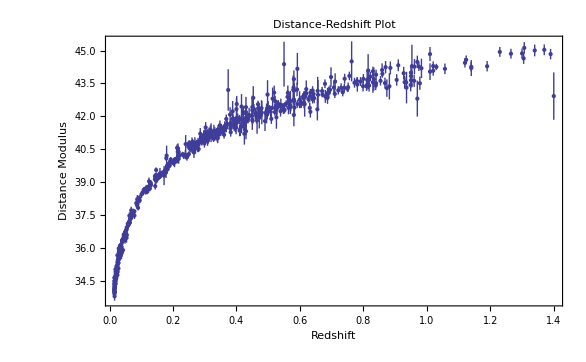

```mathematica
Show[plunion,Frame->True,FrameLabel->{"Redshift","Distance Modulus"},PlotLabel->Style["Distance-Redshift Plot",16,Orange]]
```

### Transition redshift, deceleration parameter, theoretically.

#### Theoretical Function and Values of distance/mag at different redshift.

Distance at redshift z

```mathematica
dz[Ωm0_?NumberQ,Ωd0_?NumberQ,Ωk0_?NumberQ,z_?NumberQ]:=(1+z)NIntegrate[1/hubble[Ωm0,Ωd0,Ωk0,tmp],{tmp,0,z}];
```

Magnitude calculated from distance. Theoretically of cause.

```mathematica
mag[Ωm0_?NumberQ,Ωd0_?NumberQ,Ωk0_?NumberQ,z_?NumberQ]:=5Log[10,c*dz[Ωm0,Ωd0,Ωk0,z]]+25;
```

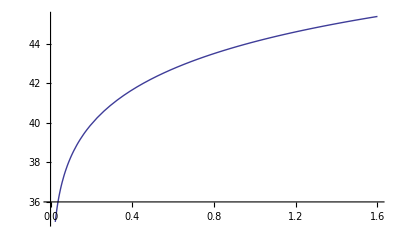

```mathematica
plmagth=Plot[mag[Ωm0w,Ωd0w,0,z],{z,0,1.6}]
```

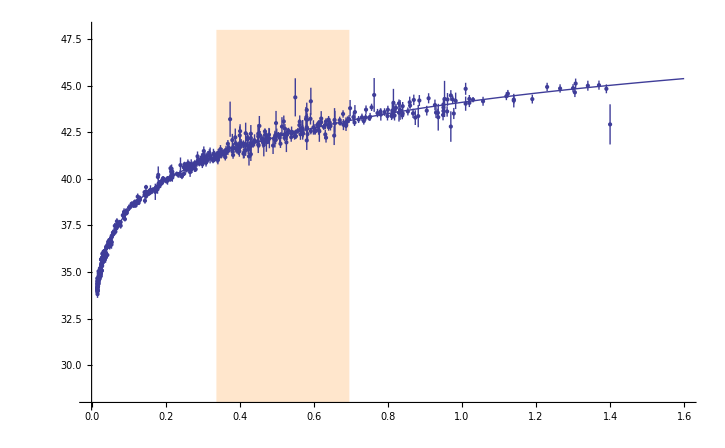

```mathematica
Show[{plunion,plmagth},PlotRange->{{0,1.6},{28,48}},AxesOrigin->{0,28},Prolog->{LightOrange,Rectangle[{0.426-0.089,28},{0.426+0.27,48}]}]
```

#### Deceleration parameter

Deceleration parameter can be ploted with respect to redshift z.
Using flat FRW model. That is Ωk0=0.

```mathematica
pldec[Ωm0v_,color_]:=Plot[q[Ωm0v,1-Ωm0v,0,z],{z,-1,5},PlotRange->{{-1.05,5},{-1.05,0.55}},PlotStyle->color,AxesOrigin->{-1,0}]
```

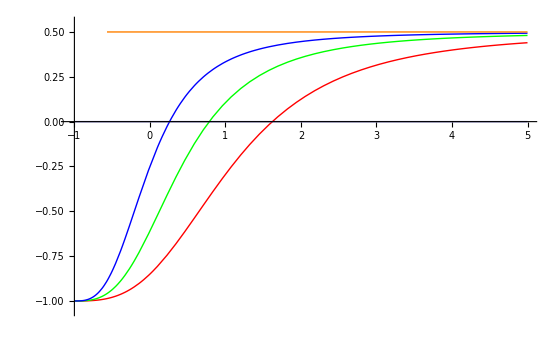

```mathematica
Show[{pldec[0.1,Red],pldec[0.26,Green],pldec[0.5,Blue],pldec[1,Orange],Plot[0,{z,-1,5},PlotStyle->Thick]}]
```

```mathematica
Manipulate[pldec[Ωm0v,{Orange,Thick}],{{Ωm0v,0.26,"Matter Fraction"},0,1}]
```

Plot deceleration parameter with respect to r. This is not related to Ωk0, i.e., the curvature of the spacetime won’t affect this result.

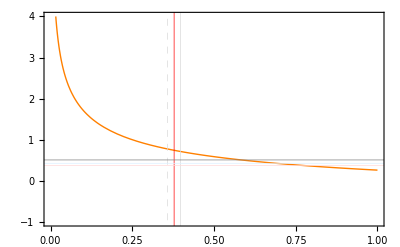

```mathematica
pldecr=Plot[ztrr[r],{r,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.358,Dashed},{0.378,Directive[Red]},0.398},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}}]
```

In a flat universe, Ωk0=0. Then Ωd0=1-Ωm0.

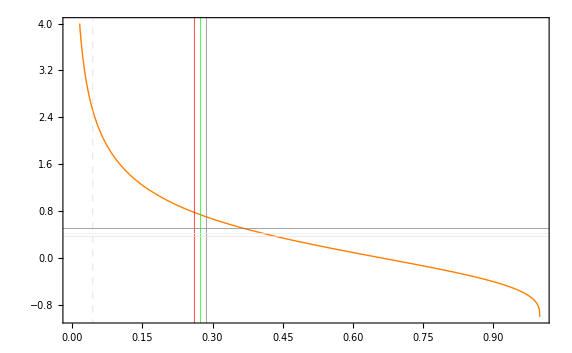

```mathematica
pldecr=Plot[ztr[Ωm0,1-Ωm0],{Ωm0,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.044,Dashed},{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}}]
```

### chi square fitting

#### Only using the error

chi square calculation.

```mathematica
chi2union[Ωm0_?NumberQ,zt_?NumberQ]:=ParallelSum[(du[[i,2]]-mag[Ωm0,1/2 Ωm0(1+zt)^3,1-Ωm0-1/2 Ωm0(1+zt)^3,du[[i,1]]])^2/du[[i,3]]^2,{i,1,len}]
```

```mathematica
Timing[chi2union[0,0.028488]]
```

NIntegrate::nlim: tmp = z is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

{0.093,1032.25}

#### Perform a grid method

It is unlucky that find minimum doesn’t work. SO I have to use grid method or Monte Carlo method. First try grid method.

```mathematica
chi2table=Table[{datatable[i,j]=Table[{chi2union[Ωm0,zt],Ωm0,zt},{Ωm0,i,i+0.19,0.01},{zt,j,j+0.19,0.01}],Export[StringJoin["OUTPUT\\dataf_",ToString[i],"_",ToString[j],".dat"],datatable[i,j]]},{i,0,0.6,0.1},{j,0.4,1.3,0.1}];
```

NIntegrate::nlim: tmp = z is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0075982789029276740118412636348921296303160488605499267578125}. NIntegrate obtained 0.0334979  - 0.00170299\ ⅈ
 and 0.000222597 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00661474008666}. NIntegrate obtained 0.0335252  - 0.00403123\ ⅈ
 and 0.000360841 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00862}. NIntegrate obtained 0.0332897  - 0.014245\ ⅈ
 and 0.000477735 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00875}. NIntegrate obtained 0.0331704  - 0.025884\ ⅈ
 and 0.000617755 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00708120806166}. NIntegrate obtained 0.0331982  - 0.00934307\ ⅈ
 and 0.00102615 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.90938253816427}. NIntegrate obtained 0.0280825  - 0.00936703\ ⅈ
 and 0.00164225 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.909134150748168}. NIntegrate obtained 0.0280316  - 0.00586681\ ⅈ
 and 0.000832608 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.911129}. NIntegrate obtained 0.0281225  - 0.00844438\ ⅈ
 and 0.000332613 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.909065534256065}. NIntegrate obtained 0.028048  - 0.00806396\ ⅈ
 and 0.00098897 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.908627641938754}. NIntegrate obtained 0.0281238  - 0.00459764\ ⅈ
 and 0.000358888 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.911351}. NIntegrate obtained 0.028105  - 0.0104015\ ⅈ
 and 0.000343707 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.908904062826119}. NIntegrate obtained 0.0281924  - 0.00630663\ ⅈ
 and 0.000285926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.908941602020671}. NIntegrate obtained 0.0280872  - 0.00751321\ ⅈ
 and 0.000410346 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.908655452397004}. NIntegrate obtained 0.0285281  - 0.00626604\ ⅈ
 and 0.000415527 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.910414}. NIntegrate obtained 0.0281275  - 0.0107497\ ⅈ
 and 0.000372371 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.910646}. NIntegrate obtained 0.0286484  - 0.0156563\ ⅈ
 and 0.000663556 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.909744}. NIntegrate obtained 0.0281003  - 0.0238349\ ⅈ
 and 0.000398022 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.908655452397004}. NIntegrate obtained 0.0285281  - 0.00626604\ ⅈ
 and 0.000415527 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.910407}. NIntegrate obtained 0.0280578  - 0.0126249\ ⅈ
 and 0.000419268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.30203317638847}. NIntegrate obtained 0.0567655  - 0.0230797\ ⅈ
 and 0.00179304 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.3031}. NIntegrate obtained 0.0568303  - 0.025499\ ⅈ
 and 0.00146935 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.30428}. NIntegrate obtained 0.0569739  - 0.0272283\ ⅈ
 and 0.000984272 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07698899315083}. NIntegrate obtained 0.0351503  - 0.00960273\ ⅈ
 and 0.000201442 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07832}. NIntegrate obtained 0.0360522  - 0.0216897\ ⅈ
 and 0.00127555 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07777}. NIntegrate obtained 0.0348898  - 0.0229498\ ⅈ
 and 0.000493769 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15056}. NIntegrate obtained 0.0420701  - 0.0230711\ ⅈ
 and 0.00180397 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15107}. NIntegrate obtained 0.0403473  - 0.0249359\ ⅈ
 and 0.0005615 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1507}. NIntegrate obtained 0.0417616  - 0.0129245\ ⅈ
 and 0.00145911 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01099875071961}. NIntegrate obtained 0.0320435  - 0.00741079\ ⅈ
 and 0.000218808 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01178308450382}. NIntegrate obtained 0.0319255  - 0.00302691\ ⅈ
 and 0.000318826 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01307}. NIntegrate obtained 0.0329742  - 0.0124181\ ⅈ
 and 0.00115794 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0141}. NIntegrate obtained 0.0317861  - 0.0225849\ ⅈ
 and 0.000547793 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.92778504086852}. NIntegrate obtained 0.0279903  - 0.00649747\ ⅈ
 and 0.000365291 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.92845977166233}. NIntegrate obtained 0.0279448  - 0.00328659\ ⅈ
 and 0.000827198 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.928405469249552}. NIntegrate obtained 0.0279685  - 0.00561244\ ⅈ
 and 0.000367939 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.928340363915731}. NIntegrate obtained 0.0280424  - 0.00688345\ ⅈ
 and 0.000277091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.92837002038882883415103763891096377847134135663509368896484375}. NIntegrate obtained 0.0282206  - 0.000989873\ ⅈ
 and 0.000121518 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.928047493409618}. NIntegrate obtained 0.0279789  - 0.00564843\ ⅈ
 and 0.000348753 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.929105}. NIntegrate obtained 0.0279547  - 0.0090376\ ⅈ
 and 0.000384276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.928554273750482}. NIntegrate obtained 0.0279598  - 0.00465442\ ⅈ
 and 0.000459597 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.928168021335286}. NIntegrate obtained 0.0278971  - 0.00580229\ ⅈ
 and 0.0015487 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.930336}. NIntegrate obtained 0.0287484  - 0.00916603\ ⅈ
 and 0.00078858 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.930685}. NIntegrate obtained 0.028132  - 0.014476\ ⅈ
 and 0.000359515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.931151}. NIntegrate obtained 0.0290172  - 0.0216118\ ⅈ
 and 0.00106191 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.928168021335286}. NIntegrate obtained 0.0278971  - 0.00580229\ ⅈ
 and 0.0015487 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.928987}. NIntegrate obtained 0.0280992  - 0.0111882\ ⅈ
 and 0.000331162 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.86768}. NIntegrate obtained 0.0254589  - 0.00927156\ ⅈ
 and 0.000312866 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.866517}. NIntegrate obtained 0.0255537  - 0.00752581\ ⅈ
 and 0.000240221 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.867196}. NIntegrate obtained 0.0255235  - 0.00954516\ ⅈ
 and 0.000324185 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.865933121463832}. NIntegrate obtained 0.0269976  - 0.00365768\ ⅈ
 and 0.00153908 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.86811}. NIntegrate obtained 0.0256023  - 0.00872705\ ⅈ
 and 0.000254155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.866411}. NIntegrate obtained 0.025587  - 0.00721201\ ⅈ
 and 0.000191402 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.867137}. NIntegrate obtained 0.0254392  - 0.00887094\ ⅈ
 and 0.000334301 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.8659359466215259463865716593744537021848373115062713623046875}. NIntegrate obtained 0.0256057  - 0.00107314\ ⅈ
 and 0.000146197 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.867953}. NIntegrate obtained 0.0254303  - 0.0110475\ ⅈ
 and 0.000324523 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.865613878336093}. NIntegrate obtained 0.0256619  - 0.00548951\ ⅈ
 and 0.000275269 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.866586}. NIntegrate obtained 0.0258433  - 0.0111914\ ⅈ
 and 0.000416381 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.868342}. NIntegrate obtained 0.0253917  - 0.0156995\ ⅈ
 and 0.000540983 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.866932}. NIntegrate obtained 0.0258946  - 0.0211862\ ⅈ
 and 0.000556275 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.866489}. NIntegrate obtained 0.0254802  - 0.00838104\ ⅈ
 and 0.000266682 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.867054}. NIntegrate obtained 0.0257768  - 0.012492\ ⅈ
 and 0.000438882 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08080512530937}. NIntegrate obtained 0.036595  - 0.00980277\ ⅈ
 and 0.00040031 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08367}. NIntegrate obtained 0.0385555  - 0.0237255\ ⅈ
 and 0.00240437 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0832}. NIntegrate obtained 0.0383169  - 0.0246266\ ⅈ
 and 0.00206176 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.968804439446782024447646364251340855844318866729736328125}. NIntegrate obtained 0.0306683  - 0.000938296\ ⅈ
 and 0.000472615 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.967728744983891}. NIntegrate obtained 0.0302974  - 0.00308864\ ⅈ
 and 0.000209573 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.968759283783077}. NIntegrate obtained 0.0301059  - 0.00444802\ ⅈ
 and 0.000597677 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.968626394455032}. NIntegrate obtained 0.0300341  - 0.00724492\ ⅈ
 and 0.000615171 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.968207741507204}. NIntegrate obtained 0.0300992  - 0.00762399\ ⅈ
 and 0.000326476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.970764}. NIntegrate obtained 0.0302616  - 0.0140045\ ⅈ
 and 0.000365755 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.971287}. NIntegrate obtained 0.0300318  - 0.0229311\ ⅈ
 and 0.000436148 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.970277}. NIntegrate obtained 0.0300029  - 0.010166\ ⅈ
 and 0.000464894 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.894204}. NIntegrate obtained 0.0267296  - 0.00868251\ ⅈ
 and 0.000610217 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.89436}. NIntegrate obtained 0.0266931  - 0.00802103\ ⅈ
 and 0.000472712 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.893115651178807}. NIntegrate obtained 0.0268512  - 0.0056331\ ⅈ
 and 0.000231401 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.894092184055365}. NIntegrate obtained 0.0268222  - 0.00621926\ ⅈ
 and 0.000341109 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.895848}. NIntegrate obtained 0.0268067  - 0.00875259\ ⅈ
 and 0.000280858 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.895292}. NIntegrate obtained 0.0275926  - 0.0075197\ ⅈ
 and 0.000884699 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.89557}. NIntegrate obtained 0.02706  - 0.010121\ ⅈ
 and 0.000423453 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.893123862527871}. NIntegrate obtained 0.0268273  - 0.00308084\ ⅈ
 and 0.000255045 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.893520591855965}. NIntegrate obtained 0.0267486  - 0.00721011\ ⅈ
 and 0.000339999 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.894476}. NIntegrate obtained 0.0268987  - 0.0106526\ ⅈ
 and 0.000461937 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.89506}. NIntegrate obtained 0.0268009  - 0.0152134\ ⅈ
 and 0.000364113 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.896365}. NIntegrate obtained 0.0269496  - 0.0218796\ ⅈ
 and 0.00037983 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.893482176233755}. NIntegrate obtained 0.0271095  - 0.00695894\ ⅈ
 and 0.000369349 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.895956}. NIntegrate obtained 0.0267338  - 0.0124738\ ⅈ
 and 0.000354708 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.837368}. NIntegrate obtained 0.0244744  - 0.0102786\ ⅈ
 and 0.000320684 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.83617414743807}. NIntegrate obtained 0.0246197  - 0.00410331\ ⅈ
 and 0.000179626 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.836538602415588}. NIntegrate obtained 0.0248154  - 0.00413492\ ⅈ
 and 0.000324739 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.837267}. NIntegrate obtained 0.0243686  - 0.00923028\ ⅈ
 and 0.000568735 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.835929828636632}. NIntegrate obtained 0.0244999  - 0.00182606\ ⅈ
 and 0.000326108 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.83811}. NIntegrate obtained 0.0244948  - 0.00988674\ ⅈ
 and 0.000326364 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.836633}. NIntegrate obtained 0.0246345  - 0.0105587\ ⅈ
 and 0.00021668 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.835879170526451}. NIntegrate obtained 0.0244356  - 0.00516179\ ⅈ
 and 0.000393669 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.838363}. NIntegrate obtained 0.0244825  - 0.0118516\ ⅈ
 and 0.000325436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.837818}. NIntegrate obtained 0.0245062  - 0.00727819\ ⅈ
 and 0.00028588 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.836703}. NIntegrate obtained 0.0244785  - 0.012236\ ⅈ
 and 0.000318916 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.83717}. NIntegrate obtained 0.0244169  - 0.0158812\ ⅈ
 and 0.000394172 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.835601000824986}. NIntegrate obtained 0.0245909  - 0.00358462\ ⅈ
 and 0.000225857 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.836802}. NIntegrate obtained 0.0253018  - 0.00928472\ ⅈ
 and 0.00083409 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.838152}. NIntegrate obtained 0.0252201  - 0.0131042\ ⅈ
 and 0.000780633 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790004}. NIntegrate obtained 0.0227951  - 0.0112736\ ⅈ
 and 0.000326828 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.789308366034158}. NIntegrate obtained 0.0228086  - 0.00535317\ ⅈ
 and 0.000159529 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.791119}. NIntegrate obtained 0.0228338  - 0.00713005\ ⅈ
 and 0.000170598 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.7902}. NIntegrate obtained 0.0228675  - 0.00684665\ ⅈ
 and 0.000291461 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.789735}. NIntegrate obtained 0.0227481  - 0.0102115\ ⅈ
 and 0.000340908 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.789173259490117}. NIntegrate obtained 0.0227269  - 0.00621216\ ⅈ
 and 0.000401347 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.791235}. NIntegrate obtained 0.0227315  - 0.0118292\ ⅈ
 and 0.000920519 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790789}. NIntegrate obtained 0.0227755  - 0.0115489\ ⅈ
 and 0.000282133 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790002}. NIntegrate obtained 0.0229704  - 0.00725319\ ⅈ
 and 0.000331556 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.788875356464003}. NIntegrate obtained 0.0231942  - 0.00367454\ ⅈ
 and 0.000474001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.788985225926804}. NIntegrate obtained 0.0228081  - 0.00431642\ ⅈ
 and 0.000230235 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.789144648862119}. NIntegrate obtained 0.0228355  - 0.00421656\ ⅈ
 and 0.00021579 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790883}. NIntegrate obtained 0.0228522  - 0.0127532\ ⅈ
 and 0.000300889 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790412}. NIntegrate obtained 0.0227965  - 0.0159336\ ⅈ
 and 0.00032325 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790415}. NIntegrate obtained 0.0226476  - 0.0109288\ ⅈ
 and 0.000453643 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790669}. NIntegrate obtained 0.0228838  - 0.0137583\ ⅈ
 and 0.000527629 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.750219}. NIntegrate obtained 0.0214125  - 0.0118943\ ⅈ
 and 0.000288455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.750554}. NIntegrate obtained 0.0214302  - 0.00708713\ ⅈ
 and 0.000249015 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.749934}. NIntegrate obtained 0.0215304  - 0.00824191\ ⅈ
 and 0.000365063 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.749517}. NIntegrate obtained 0.0213722  - 0.0110317\ ⅈ
 and 0.000225712 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.750676}. NIntegrate obtained 0.0212849  - 0.0123213\ ⅈ
 and 0.000353974 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.749064739698354}. NIntegrate obtained 0.0213205  - 0.00458715\ ⅈ
 and 0.000321213 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.74874415440181}. NIntegrate obtained 0.0213135  - 0.00309599\ ⅈ
 and 0.000329349 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.750807}. NIntegrate obtained 0.0214736  - 0.00832581\ ⅈ
 and 0.00028387 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.749753}. NIntegrate obtained 0.0218076  - 0.00743508\ ⅈ
 and 0.000481864 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.75101}. NIntegrate obtained 0.0213414  - 0.00939668\ ⅈ
 and 0.000774424 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.750796}. NIntegrate obtained 0.0213111  - 0.0065639\ ⅈ
 and 0.000411261 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.749004205683727}. NIntegrate obtained 0.021385  - 0.0020177\ ⅈ
 and 0.000201827 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.750644}. NIntegrate obtained 0.0212878  - 0.0067643\ ⅈ
 and 0.000389864 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.751039}. NIntegrate obtained 0.0213977  - 0.0132654\ ⅈ
 and 0.000287066 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.750334}. NIntegrate obtained 0.021355  - 0.0160825\ ⅈ
 and 0.000320872 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.749007142642951}. NIntegrate obtained 0.0215121  - 0.00436083\ ⅈ
 and 0.000233954 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.749595}. NIntegrate obtained 0.0216752  - 0.0112745\ ⅈ
 and 0.000368942 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.751445}. NIntegrate obtained 0.0214292  - 0.0143443\ ⅈ
 and 0.000148611 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04201}. NIntegrate obtained 0.0341936  - 0.0127272\ ⅈ
 and 0.000668146 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04086}. NIntegrate obtained 0.035048  - 0.0243628\ ⅈ
 and 0.000650067 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04248}. NIntegrate obtained 0.0346771  - 0.0250694\ ⅈ
 and 0.000910397 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04023099734154}. NIntegrate obtained 0.0344068  - 0.0048119\ ⅈ
 and 0.000379479 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.938076359554235}. NIntegrate obtained 0.0289935  - 0.00597522\ ⅈ
 and 0.000448238 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.939211942852552}. NIntegrate obtained 0.0289835  - 0.00664636\ ⅈ
 and 0.000409715 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.93931728429975}. NIntegrate obtained 0.0290932  - 0.00467013\ ⅈ
 and 0.000225512 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.940941}. NIntegrate obtained 0.0290101  - 0.00866512\ ⅈ
 and 0.000331759 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.938915230003379}. NIntegrate obtained 0.0289798  - 0.0048099\ ⅈ
 and 0.000449294 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.939033311850421}. NIntegrate obtained 0.0292094  - 0.00300302\ ⅈ
 and 0.000307991 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.938987838596607}. NIntegrate obtained 0.0290561  - 0.00675319\ ⅈ
 and 0.000319329 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.938795425238114}. NIntegrate obtained 0.0290014  - 0.00333751\ ⅈ
 and 0.000317395 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.940297}. NIntegrate obtained 0.0296428  - 0.00900607\ ⅈ
 and 0.000754431 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.939592}. NIntegrate obtained 0.0300117  - 0.0147415\ ⅈ
 and 0.00103211 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.941854}. NIntegrate obtained 0.0294651  - 0.0228183\ ⅈ
 and 0.000599935 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.938795425238114}. NIntegrate obtained 0.0290014  - 0.00333751\ ⅈ
 and 0.000317395 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.941374}. NIntegrate obtained 0.0296727  - 0.0111992\ ⅈ
 and 0.000655243 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.869575}. NIntegrate obtained 0.0260028  - 0.00934736\ ⅈ
 and 0.000281113 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.870173}. NIntegrate obtained 0.0257951  - 0.00837201\ ⅈ
 and 0.00092925 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.869985}. NIntegrate obtained 0.0258641  - 0.00904479\ ⅈ
 and 0.000429198 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.870044}. NIntegrate obtained 0.0260273  - 0.00715021\ ⅈ
 and 0.00034112 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.871016}. NIntegrate obtained 0.0260629  - 0.00971552\ ⅈ
 and 0.000255816 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.868464713821234}. NIntegrate obtained 0.0277473  - 0.00343859\ ⅈ
 and 0.00179355 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.870891}. NIntegrate obtained 0.0398074  - 0.00874304\ ⅈ
 and 0.0138646 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.869926}. NIntegrate obtained 0.0264731  - 0.0109398\ ⅈ
 and 0.00061659 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.869107165932065}. NIntegrate obtained 0.0262835  - 0.00540452\ ⅈ
 and 0.000361581 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.869284}. NIntegrate obtained 0.0260415  - 0.00835163\ ⅈ
 and 0.000194775 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.87057}. NIntegrate obtained 0.0258389  - 0.0118074\ ⅈ
 and 0.000454404 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.870568}. NIntegrate obtained 0.0261058  - 0.0155982\ ⅈ
 and 0.000418329 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.869608}. NIntegrate obtained 0.0258217  - 0.0225095\ ⅈ
 and 0.000516027 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.8702}. NIntegrate obtained 0.0258097  - 0.00883558\ ⅈ
 and 0.000637072 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.871183}. NIntegrate obtained 0.0261869  - 0.0128662\ ⅈ
 and 0.00032398 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.814633}. NIntegrate obtained 0.0238494  - 0.0110389\ ⅈ
 and 0.000242798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.814492330476412}. NIntegrate obtained 0.0237773  - 0.00385492\ ⅈ
 and 0.000568107 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.814396142667325}. NIntegrate obtained 0.0243219  - 0.00562225\ ⅈ
 and 0.000504437 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.815329}. NIntegrate obtained 0.0237293  - 0.00975716\ ⅈ
 and 0.000397053 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.814371207771059}. NIntegrate obtained 0.0239711  - 0.00574325\ ⅈ
 and 0.000232093 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.815622}. NIntegrate obtained 0.023711  - 0.0113922\ ⅈ
 and 0.000402612 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.81352370272165}. NIntegrate obtained 0.023825  - 0.00446191\ ⅈ
 and 0.00023926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.81561}. NIntegrate obtained 0.023723  - 0.0107016\ ⅈ
 and 0.000377901 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.814611164621105}. NIntegrate obtained 0.0239272  - 0.00634891\ ⅈ
 and 0.00019599 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.8144602758818622104640405634512489996268413960933685302734375}. NIntegrate obtained 0.0240221  - 0.00123838\ ⅈ
 and 0.000199833 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.814691}. NIntegrate obtained 0.0242778  - 0.0122053\ ⅈ
 and 0.000478066 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.81456982434116585061779913790047658039839006960391998291015625}. NIntegrate obtained 0.0238449  - 0.0018884\ ⅈ
 and 0.000942856 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.814789}. NIntegrate obtained 0.0239384  - 0.0125546\ ⅈ
 and 0.000254412 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.814904}. NIntegrate obtained 0.0237018  - 0.0164413\ ⅈ
 and 0.000498968 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.816391}. NIntegrate obtained 0.0238091  - 0.0103928\ ⅈ
 and 0.000308196 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.815443}. NIntegrate obtained 0.023745  - 0.0138356\ ⅈ
 and 0.000355192 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.771059}. NIntegrate obtained 0.0221572  - 0.0117939\ ⅈ
 and 0.00025821 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.770007}. NIntegrate obtained 0.0222348  - 0.00630694\ ⅈ
 and 0.000257331 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.770067}. NIntegrate obtained 0.0223799  - 0.00764439\ ⅈ
 and 0.000331461 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.769626}. NIntegrate obtained 0.0221477  - 0.0108227\ ⅈ
 and 0.000264633 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.769778}. NIntegrate obtained 0.0220878  - 0.0122434\ ⅈ
 and 0.000373114 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.768704401353489}. NIntegrate obtained 0.0224962  - 0.00249211\ ⅈ
 and 0.000340705 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.770963}. NIntegrate obtained 0.022458  - 0.00769528\ ⅈ
 and 0.000356408 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.771081}. NIntegrate obtained 0.0221442  - 0.00776455\ ⅈ
 and 0.000954187 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.769658}. NIntegrate obtained 0.0222465  - 0.00814267\ ⅈ
 and 0.000215727 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.768888558443773}. NIntegrate obtained 0.0222553  - 0.00522589\ ⅈ
 and 0.000196171 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.769237432609403}. NIntegrate obtained 0.0221238  - 0.00600386\ ⅈ
 and 0.000441093 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.769150817894647}. NIntegrate obtained 0.0221915  - 0.00560844\ ⅈ
 and 0.000205632 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.770961}. NIntegrate obtained 0.0222805  - 0.0131052\ ⅈ
 and 0.000431423 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.770373}. NIntegrate obtained 0.0220416  - 0.0164537\ ⅈ
 and 0.000429259 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.769147611175573}. NIntegrate obtained 0.0222318  - 0.00275465\ ⅈ
 and 0.00014797 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.770005}. NIntegrate obtained 0.0221017  - 0.0112568\ ⅈ
 and 0.000333348 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.770025}. NIntegrate obtained 0.0220471  - 0.0144964\ ⅈ
 and 0.000462503 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731274}. NIntegrate obtained 0.0207487  - 0.0125489\ ⅈ
 and 0.000531272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.7311}. NIntegrate obtained 0.0207911  - 0.00817062\ ⅈ
 and 0.000443844 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.730762697509303}. NIntegrate obtained 0.0209165  - 0.0043676\ ⅈ
 and 0.000192194 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731479}. NIntegrate obtained 0.0208034  - 0.00896565\ ⅈ
 and 0.000260846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731235}. NIntegrate obtained 0.0216852  - 0.0112185\ ⅈ
 and 0.00095841 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731238}. NIntegrate obtained 0.0207895  - 0.00559884\ ⅈ
 and 0.000429985 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.73233}. NIntegrate obtained 0.0207405  - 0.00929912\ ⅈ
 and 0.000442653 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731575}. NIntegrate obtained 0.0208487  - 0.0124704\ ⅈ
 and 0.00047686 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731706}. NIntegrate obtained 0.0208245  - 0.00822118\ ⅈ
 and 0.000286327 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.732362}. NIntegrate obtained 0.0207652  - 0.00941315\ ⅈ
 and 0.000320151 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731788}. NIntegrate obtained 0.0212794  - 0.0068531\ ⅈ
 and 0.000520499 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.730076904284778}. NIntegrate obtained 0.0208926  - 0.00390019\ ⅈ
 and 0.000156144 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731519}. NIntegrate obtained 0.0209439  - 0.0071521\ ⅈ
 and 0.000261342 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731117}. NIntegrate obtained 0.0207725  - 0.0139313\ ⅈ
 and 0.000464608 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.732521}. NIntegrate obtained 0.0207442  - 0.0163924\ ⅈ
 and 0.000344794 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.732175}. NIntegrate obtained 0.0212811  - 0.00537352\ ⅈ
 and 0.000531404 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.73104}. NIntegrate obtained 0.0208578  - 0.0118707\ ⅈ
 and 0.000229878 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.732864}. NIntegrate obtained 0.0207796  - 0.0146121\ ⅈ
 and 0.000304198 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.699067}. NIntegrate obtained 0.0196236  - 0.0131498\ ⅈ
 and 0.000673935 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.698679}. NIntegrate obtained 0.0196402  - 0.00893748\ ⅈ
 and 0.000318626 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.697418}. NIntegrate obtained 0.0197417  - 0.00621657\ ⅈ
 and 0.000225693 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.697722}. NIntegrate obtained 0.0199863  - 0.00674793\ ⅈ
 and 0.000333268 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.697924}. NIntegrate obtained 0.0198128  - 0.00957795\ ⅈ
 and 0.000356557 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.698737}. NIntegrate obtained 0.0196537  - 0.00982968\ ⅈ
 and 0.000311233 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.698329}. NIntegrate obtained 0.0195753  - 0.0122955\ ⅈ
 and 0.000722807 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.698893}. NIntegrate obtained 0.0197235  - 0.0091066\ ⅈ
 and 0.000194725 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.699102}. NIntegrate obtained 0.019655  - 0.0130213\ ⅈ
 and 0.000301248 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.698455}. NIntegrate obtained 0.0200886  - 0.00977757\ ⅈ
 and 0.000461777 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.698525}. NIntegrate obtained 0.0197488  - 0.00803795\ ⅈ
 and 0.000241076 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.698402}. NIntegrate obtained 0.0196671  - 0.00585143\ ⅈ
 and 0.000263677 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.69805}. NIntegrate obtained 0.0196749  - 0.00830029\ ⅈ
 and 0.000259443 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.699242}. NIntegrate obtained 0.0197865  - 0.0137563\ ⅈ
 and 0.000222437 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.699123}. NIntegrate obtained 0.0195739  - 0.0168258\ ⅈ
 and 0.000655196 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.698617}. NIntegrate obtained 0.0196654  - 0.00702855\ ⅈ
 and 0.000257396 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.697641}. NIntegrate obtained 0.0196198  - 0.012489\ ⅈ
 and 0.000480547 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.697769}. NIntegrate obtained 0.0197658  - 0.0145366\ ⅈ
 and 0.000245296 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.668754}. NIntegrate obtained 0.0194675  - 0.0126884\ ⅈ
 and 0.000879635 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.667878}. NIntegrate obtained 0.018887  - 0.00927745\ ⅈ
 and 0.000249017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.667613}. NIntegrate obtained 0.018946  - 0.0070877\ ⅈ
 and 0.000341281 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.667725}. NIntegrate obtained 0.0189061  - 0.0101107\ ⅈ
 and 0.000237017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.669079}. NIntegrate obtained 0.0187944  - 0.0120641\ ⅈ
 and 0.000220466 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.668777}. NIntegrate obtained 0.0187033  - 0.00786875\ ⅈ
 and 0.000240603 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.668539}. NIntegrate obtained 0.0186161  - 0.0133899\ ⅈ
 and 0.000486953 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.668502}. NIntegrate obtained 0.0187372  - 0.0102037\ ⅈ
 and 0.000247032 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.667721}. NIntegrate obtained 0.0189048  - 0.00958366\ ⅈ
 and 0.000229297 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.66794}. NIntegrate obtained 0.0195062  - 0.0102735\ ⅈ
 and 0.00079035 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.668429}. NIntegrate obtained 0.0187088  - 0.00883233\ ⅈ
 and 0.000250398 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.668871}. NIntegrate obtained 0.0187011  - 0.0070932\ ⅈ
 and 0.000312512 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.667281155517085}. NIntegrate obtained 0.018764  - 0.00319819\ ⅈ
 and 0.00018037 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.667769}. NIntegrate obtained 0.0186712  - 0.0092318\ ⅈ
 and 0.000377742 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.669359}. NIntegrate obtained 0.0187248  - 0.0139976\ ⅈ
 and 0.00022588 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.667951}. NIntegrate obtained 0.018784  - 0.0161774\ ⅈ
 and 0.000248937 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.667281155517085}. NIntegrate obtained 0.018764  - 0.00319819\ ⅈ
 and 0.00018037 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.667294921354169}. NIntegrate obtained 0.018791  - 0.00251761\ ⅈ
 and 0.000174874 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.017574499486124986989687979388463645591400563716888427734375}. NIntegrate obtained 0.0336473  - 0.0018555\ ⅈ
 and 0.000101643 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01975}. NIntegrate obtained 0.0337288  - 0.0135166\ ⅈ
 and 0.000326612 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01945}. NIntegrate obtained 0.0335035  - 0.0248281\ ⅈ
 and 0.000588722 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01717169169058}. NIntegrate obtained 0.0335726  - 0.00750351\ ⅈ
 and 0.000257537 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.919632431184291}. NIntegrate obtained 0.0283385  - 0.00732357\ ⅈ
 and 0.000359447 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.919838001633696}. NIntegrate obtained 0.0289864  - 0.00378281\ ⅈ
 and 0.000631907 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.919439304860985}. NIntegrate obtained 0.0284094  - 0.00637249\ ⅈ
 and 0.000291142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.919031311022575}. NIntegrate obtained 0.0284252  - 0.00318837\ ⅈ
 and 0.000232407 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.919816387743803}. NIntegrate obtained 0.0283478  - 0.00792216\ ⅈ
 and 0.000364479 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.919176726056338}. NIntegrate obtained 0.0285935  - 0.00634639\ ⅈ
 and 0.000294979 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.921215}. NIntegrate obtained 0.0283272  - 0.00971984\ ⅈ
 and 0.000386158 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.919088087955768}. NIntegrate obtained 0.0285957  - 0.00528359\ ⅈ
 and 0.000307486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.920056568554246}. NIntegrate obtained 0.0285054  - 0.00546177\ ⅈ
 and 0.000233627 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.920375}. NIntegrate obtained 0.0282401  - 0.0123627\ ⅈ
 and 0.00224958 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.921779}. NIntegrate obtained 0.0286773  - 0.015301\ ⅈ
 and 0.000473435 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.920447}. NIntegrate obtained 0.0301246  - 0.0230642\ ⅈ
 and 0.00183419 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.920056568554246}. NIntegrate obtained 0.0285054  - 0.00546177\ ⅈ
 and 0.000233627 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.92073}. NIntegrate obtained 0.0284026  - 0.0119981\ ⅈ
 and 0.000392639 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.852524}. NIntegrate obtained 0.0255395  - 0.00998418\ ⅈ
 and 0.000343322 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.852041821280431}. NIntegrate obtained 0.0256329  - 0.00242277\ ⅈ
 and 0.000246844 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.852080068224296}. NIntegrate obtained 0.0254206  - 0.00273211\ ⅈ
 and 0.000455992 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.85311}. NIntegrate obtained 0.0285168  - 0.00936426\ ⅈ
 and 0.00315691 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.853696}. NIntegrate obtained 0.0255376  - 0.00805499\ ⅈ
 and 0.000279005 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.85372}. NIntegrate obtained 0.0255864  - 0.0083441\ ⅈ
 and 0.000298667 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.853825}. NIntegrate obtained 0.0258241  - 0.0102498\ ⅈ
 and 0.000512716 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.85178234078738}. NIntegrate obtained 0.0253756  - 0.00383303\ ⅈ
 and 0.000379926 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.854144}. NIntegrate obtained 0.0255555  - 0.0117825\ ⅈ
 and 0.000125659 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.852092872107111}. NIntegrate obtained 0.0254408  - 0.00689583\ ⅈ
 and 0.000309633 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.85264}. NIntegrate obtained 0.0252778  - 0.0131345\ ⅈ
 and 0.00114858 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.852756}. NIntegrate obtained 0.0253393  - 0.0162489\ ⅈ
 and 0.000671963 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.851969237805049707350224519331050032633356750011444091796875}. NIntegrate obtained 0.0256146  - 0.00111338\ ⅈ
 and 0.000200083 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.853501}. NIntegrate obtained 0.0255051  - 0.00906965\ ⅈ
 and 0.000305132 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.852603}. NIntegrate obtained 0.0257466  - 0.0132629\ ⅈ
 and 0.000421469 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.799477}. NIntegrate obtained 0.0232908  - 0.0114771\ ⅈ
 and 0.000331597 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.798725169444824}. NIntegrate obtained 0.0233532  - 0.00502093\ ⅈ
 and 0.000334378 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.800266}. NIntegrate obtained 0.0252355  - 0.00643758\ ⅈ
 and 0.00187744 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.800704}. NIntegrate obtained 0.0236796  - 0.0100279\ ⅈ
 and 0.000367782 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.80034}. NIntegrate obtained 0.0234165  - 0.0115684\ ⅈ
 and 0.000294073 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.799518}. NIntegrate obtained 0.0235315  - 0.00656879\ ⅈ
 and 0.000316916 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.798818105383967}. NIntegrate obtained 0.0233571  - 0.00594013\ ⅈ
 and 0.000497068 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.80061}. NIntegrate obtained 0.0239966  - 0.0108447\ ⅈ
 and 0.000674953 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.800174}. NIntegrate obtained 0.0233882  - 0.00709612\ ⅈ
 and 0.000270973 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.798692333755941}. NIntegrate obtained 0.0235214  - 0.0028723\ ⅈ
 and 0.00018993 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.798224498348346}. NIntegrate obtained 0.0236703  - 0.00345896\ ⅈ
 and 0.000404593 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.798419691654787}. NIntegrate obtained 0.0232646  - 0.00430711\ ⅈ
 and 0.000926314 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.800844}. NIntegrate obtained 0.0235527  - 0.0129012\ ⅈ
 and 0.000289357 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.799318}. NIntegrate obtained 0.0233137  - 0.0164147\ ⅈ
 and 0.000305526 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.799692}. NIntegrate obtained 0.0232521  - 0.0108784\ ⅈ
 and 0.000419958 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.800991}. NIntegrate obtained 0.0234346  - 0.0141125\ ⅈ
 and 0.000287724 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.755903}. NIntegrate obtained 0.0225717  - 0.0118835\ ⅈ
 and 0.000893968 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.755417}. NIntegrate obtained 0.0217319  - 0.00708649\ ⅈ
 and 0.000264226 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.756645}. NIntegrate obtained 0.0218514  - 0.00839411\ ⅈ
 and 0.000143487 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.755001}. NIntegrate obtained 0.0218089  - 0.0111194\ ⅈ
 and 0.000177104 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.756407}. NIntegrate obtained 0.0221261  - 0.0121544\ ⅈ
 and 0.000462916 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.754986740718516}. NIntegrate obtained 0.0218466  - 0.00234675\ ⅈ
 and 0.000100098 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.754329443765261}. NIntegrate obtained 0.0217145  - 0.00417847\ ⅈ
 and 0.000288307 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.755846}. NIntegrate obtained 0.021651  - 0.00862895\ ⅈ
 and 0.000485995 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.756315}. NIntegrate obtained 0.0217689  - 0.00751715\ ⅈ
 and 0.000237314 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.756096}. NIntegrate obtained 0.0216652  - 0.00890065\ ⅈ
 and 0.000397635 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.755548}. NIntegrate obtained 0.0216275  - 0.00691832\ ⅈ
 and 0.00095245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.75467498431608018099291113056636959299794398248195648193359375}. NIntegrate obtained 0.0222741  - 0.000706\ ⅈ
 and 0.000446924 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.755425}. NIntegrate obtained 0.021761  - 0.00633984\ ⅈ
 and 0.0002502 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.755023}. NIntegrate obtained 0.0218768  - 0.0134645\ ⅈ
 and 0.000229836 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.757014}. NIntegrate obtained 0.0217955  - 0.0164157\ ⅈ
 and 0.000234064 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.7542196590561}. NIntegrate obtained 0.0217783  - 0.00412678\ ⅈ
 and 0.000209191 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.755161}. NIntegrate obtained 0.0219794  - 0.0113968\ ⅈ
 and 0.000293995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.755573}. NIntegrate obtained 0.0217741  - 0.0143978\ ⅈ
 and 0.000283853 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.718012}. NIntegrate obtained 0.0212385  - 0.0123525\ ⅈ
 and 0.000875568 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.718132}. NIntegrate obtained 0.0208929  - 0.00811902\ ⅈ
 and 0.000520874 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.717215226720185}. NIntegrate obtained 0.0207626  - 0.00518651\ ⅈ
 and 0.00028817 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.718057}. NIntegrate obtained 0.0204595  - 0.00929529\ ⅈ
 and 0.000258061 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.718439}. NIntegrate obtained 0.0205973  - 0.0115217\ ⅈ
 and 0.000325666 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.717527}. NIntegrate obtained 0.0211997  - 0.00602375\ ⅈ
 and 0.000747954 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.718893}. NIntegrate obtained 0.0205135  - 0.00933611\ ⅈ
 and 0.000194765 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.718204}. NIntegrate obtained 0.0205558  - 0.0126438\ ⅈ
 and 0.00031349 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.718581}. NIntegrate obtained 0.0208049  - 0.008506\ ⅈ
 and 0.000419895 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.718799}. NIntegrate obtained 0.0206835  - 0.00950115\ ⅈ
 and 0.000308882 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.717532}. NIntegrate obtained 0.0211018  - 0.00741938\ ⅈ
 and 0.000660882 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.716744451520952}. NIntegrate obtained 0.0204901  - 0.00482264\ ⅈ
 and 0.000177091 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.718769}. NIntegrate obtained 0.0204156  - 0.00791804\ ⅈ
 and 0.000310681 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.719164}. NIntegrate obtained 0.0204703  - 0.0137966\ ⅈ
 and 0.00026704 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.719162}. NIntegrate obtained 0.0204373  - 0.016436\ ⅈ
 and 0.000297495 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.718447}. NIntegrate obtained 0.0205412  - 0.00612313\ ⅈ
 and 0.000242239 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.718052}. NIntegrate obtained 0.0203416  - 0.0122636\ ⅈ
 and 0.000508572 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.718413}. NIntegrate obtained 0.0203186  - 0.0149399\ ⅈ
 and 0.000474083 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685805}. NIntegrate obtained 0.0194033  - 0.0127768\ ⅈ
 and 0.000252855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.68571}. NIntegrate obtained 0.0192569  - 0.00957395\ ⅈ
 and 0.000565106 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685496}. NIntegrate obtained 0.0193631  - 0.00663292\ ⅈ
 and 0.000223009 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.684502}. NIntegrate obtained 0.0194862  - 0.00993902\ ⅈ
 and 0.00025373 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685532}. NIntegrate obtained 0.0194524  - 0.0119282\ ⅈ
 and 0.000286531 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685731}. NIntegrate obtained 0.0192682  - 0.0131685\ ⅈ
 and 0.000322276 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685535}. NIntegrate obtained 0.0193938  - 0.00729585\ ⅈ
 and 0.000287583 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685299}. NIntegrate obtained 0.0192222  - 0.0107402\ ⅈ
 and 0.000851634 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685768}. NIntegrate obtained 0.0193143  - 0.00949022\ ⅈ
 and 0.000264833 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.684893}. NIntegrate obtained 0.0192887  - 0.0103521\ ⅈ
 and 0.000290128 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685853}. NIntegrate obtained 0.0192924  - 0.00880594\ ⅈ
 and 0.00049909 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685113}. NIntegrate obtained 0.0194408  - 0.0062537\ ⅈ
 and 0.000265409 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.68429993272937}. NIntegrate obtained 0.019435  - 0.0011263\ ⅈ
 and 0.000145054 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.6853}. NIntegrate obtained 0.0192798  - 0.0087693\ ⅈ
 and 0.000309761 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685297}. NIntegrate obtained 0.0193501  - 0.013932\ ⅈ
 and 0.000275193 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685764}. NIntegrate obtained 0.0194452  - 0.0162769\ ⅈ
 and 0.000306206 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.68429993272937}. NIntegrate obtained 0.019435  - 0.0011263\ ⅈ
 and 0.000145054 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.684888}. NIntegrate obtained 0.0193587  - 0.00736994\ ⅈ
 and 0.000344191 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.655493}. NIntegrate obtained 0.0183319  - 0.013233\ ⅈ
 and 0.000323524 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.65653}. NIntegrate obtained 0.0183629  - 0.0097424\ ⅈ
 and 0.000249154 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.65520500381948008059886101595026275390409864485263824462890625}. NIntegrate obtained 0.018492  - 0.000935126\ ⅈ
 and 0.0000843082 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.656589}. NIntegrate obtained 0.0183653  - 0.00832463\ ⅈ
 and 0.000287781 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.656744}. NIntegrate obtained 0.018384  - 0.010555\ ⅈ
 and 0.000245445 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.655981}. NIntegrate obtained 0.0184823  - 0.0103491\ ⅈ
 and 0.00027077 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.656282}. NIntegrate obtained 0.0184336  - 0.0122389\ ⅈ
 and 0.000251441 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.656237}. NIntegrate obtained 0.0186256  - 0.00978884\ ⅈ
 and 0.000339242 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.657079}. NIntegrate obtained 0.0184182  - 0.0132951\ ⅈ
 and 0.000184851 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.656072}. NIntegrate obtained 0.0193653  - 0.0104816\ ⅈ
 and 0.00110967 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.655757}. NIntegrate obtained 0.0186061  - 0.00897401\ ⅈ
 and 0.000301664 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.655582}. NIntegrate obtained 0.0183095  - 0.0078391\ ⅈ
 and 0.000636008 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.654555146583123}. NIntegrate obtained 0.0184493  - 0.00407178\ ⅈ
 and 0.000149432 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.654555146583123}. NIntegrate obtained 0.0184493  - 0.00407178\ ⅈ
 and 0.000149432 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.656612}. NIntegrate obtained 0.0187214  - 0.00912369\ ⅈ
 and 0.000360372 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.655414}. NIntegrate obtained 0.0185116  - 0.0140068\ ⅈ
 and 0.000217854 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.656818}. NIntegrate obtained 0.018441  - 0.016254\ ⅈ
 and 0.000265267 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.654832582842504}. NIntegrate obtained 0.0185182  - 0.00357496\ ⅈ
 and 0.00010319 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.628969}. NIntegrate obtained 0.0179087  - 0.0131427\ ⅈ
 and 0.000336105 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.628971}. NIntegrate obtained 0.017583  - 0.0106444\ ⅈ
 and 0.000737108 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.628406981289297}. NIntegrate obtained 0.0176777  - 0.00365008\ ⅈ
 and 0.000170775 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.6281686023446}. NIntegrate obtained 0.0175785  - 0.00378178\ ⅈ
 and 0.000282859 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.628949060946117}. NIntegrate obtained 0.0176177  - 0.00237019\ ⅈ
 and 0.000150422 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.629137}. NIntegrate obtained 0.0177917  - 0.0106703\ ⅈ
 and 0.000273962 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.629168}. NIntegrate obtained 0.0175177  - 0.00888838\ ⅈ
 and 0.000302079 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.630689}. NIntegrate obtained 0.0178878  - 0.0123788\ ⅈ
 and 0.000417655 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.629869}. NIntegrate obtained 0.0175199  - 0.0108557\ ⅈ
 and 0.000271937 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.630643}. NIntegrate obtained 0.0176213  - 0.0111453\ ⅈ
 and 0.000174847 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.630413}. NIntegrate obtained 0.0176117  - 0.00955442\ ⅈ
 and 0.000174454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.629004}. NIntegrate obtained 0.0176909  - 0.00793759\ ⅈ
 and 0.00015937 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.628520025549101}. NIntegrate obtained 0.0175876  - 0.00113538\ ⅈ
 and 0.000254666 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.628784186465397}. NIntegrate obtained 0.0176699  - 0.00276463\ ⅈ
 and 0.000139516 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.628621929851365}. NIntegrate obtained 0.0178712  - 0.00127932\ ⅈ
 and 0.000301331 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.629292}. NIntegrate obtained 0.0175076  - 0.00557311\ ⅈ
 and 0.000326456 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.629292}. NIntegrate obtained 0.0175076  - 0.00557311\ ⅈ
 and 0.000326456 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.629519}. NIntegrate obtained 0.018092  - 0.00952924\ ⅈ
 and 0.000569234 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.629515}. NIntegrate obtained 0.0175479  - 0.0141346\ ⅈ
 and 0.000254974 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.630099}. NIntegrate obtained 0.0174312  - 0.0166112\ ⅈ
 and 0.000531538 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.629521}. NIntegrate obtained 0.0175822  - 0.00500557\ ⅈ
 and 0.000208849 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.604861077811789}. NIntegrate obtained 0.0168712  - 0.00260473\ ⅈ
 and 0.000185541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.604380738252909}. NIntegrate obtained 0.0168225  - 0.00226324\ ⅈ
 and 0.000214881 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.606235}. NIntegrate obtained 0.0169457  - 0.0131353\ ⅈ
 and 0.000410191 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.606377}. NIntegrate obtained 0.0172257  - 0.00479203\ ⅈ
 and 0.000369853 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.606276}. NIntegrate obtained 0.0169061  - 0.0102778\ ⅈ
 and 0.000224338 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.605649}. NIntegrate obtained 0.0169767  - 0.0108989\ ⅈ
 and 0.000260594 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.605213}. NIntegrate obtained 0.0168238  - 0.0112824\ ⅈ
 and 0.000199933 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.606653}. NIntegrate obtained 0.0168941  - 0.00991183\ ⅈ
 and 0.00026115 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.604628172553077}. NIntegrate obtained 0.0168857  - 0.00402355\ ⅈ
 and 0.000145545 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.605379}. NIntegrate obtained 0.016905  - 0.00839997\ ⅈ
 and 0.000190792 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.606316}. NIntegrate obtained 0.0167835  - 0.00924226\ ⅈ
 and 0.000256816 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.606354}. NIntegrate obtained 0.0170231  - 0.0109099\ ⅈ
 and 0.000294077 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.604781894995501}. NIntegrate obtained 0.0168798  - 0.00174473\ ⅈ
 and 0.000158818 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.604339793090918}. NIntegrate obtained 0.016965  - 0.00344743\ ⅈ
 and 0.000118636 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.604692512490675}. NIntegrate obtained 0.0169508  - 0.00426762\ ⅈ
 and 0.000224423 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.60514}. NIntegrate obtained 0.016911  - 0.00620865\ ⅈ
 and 0.000137488 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.605614}. NIntegrate obtained 0.0167655  - 0.00612098\ ⅈ
 and 0.00031885 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.605612}. NIntegrate obtained 0.0169443  - 0.00992473\ ⅈ
 and 0.000275747 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.605609}. NIntegrate obtained 0.0167441  - 0.0143184\ ⅈ
 and 0.000366115 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.605607}. NIntegrate obtained 0.0177752  - 0.0159609\ ⅈ
 and 0.00104476 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0075982789029276740118412636348921296303160488605499267578125}. NIntegrate obtained 0.0334979  - 0.00170299\ ⅈ
 and 0.000222597 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00661474008666}. NIntegrate obtained 0.0335252  - 0.00403123\ ⅈ
 and 0.000360841 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00862}. NIntegrate obtained 0.0332897  - 0.014245\ ⅈ
 and 0.000477735 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00875}. NIntegrate obtained 0.0331704  - 0.025884\ ⅈ
 and 0.000617755 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00708120806166}. NIntegrate obtained 0.0331982  - 0.00934307\ ⅈ
 and 0.00102615 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.90938253816427}. NIntegrate obtained 0.0280825  - 0.00936703\ ⅈ
 and 0.00164225 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.909134150748168}. NIntegrate obtained 0.0280316  - 0.00586681\ ⅈ
 and 0.000832608 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.911129}. NIntegrate obtained 0.0281225  - 0.00844438\ ⅈ
 and 0.000332613 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.909065534256065}. NIntegrate obtained 0.028048  - 0.00806396\ ⅈ
 and 0.00098897 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.908627641938754}. NIntegrate obtained 0.0281238  - 0.00459764\ ⅈ
 and 0.000358888 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.908941602020671}. NIntegrate obtained 0.0280872  - 0.00751321\ ⅈ
 and 0.000410346 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.911351}. NIntegrate obtained 0.028105  - 0.0104015\ ⅈ
 and 0.000343707 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.908904062826119}. NIntegrate obtained 0.0281924  - 0.00630663\ ⅈ
 and 0.000285926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.908655452397004}. NIntegrate obtained 0.0285281  - 0.00626604\ ⅈ
 and 0.000415527 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.910414}. NIntegrate obtained 0.0281275  - 0.0107497\ ⅈ
 and 0.000372371 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.910646}. NIntegrate obtained 0.0286484  - 0.0156563\ ⅈ
 and 0.000663556 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.909744}. NIntegrate obtained 0.0281003  - 0.0238349\ ⅈ
 and 0.000398022 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.908655452397004}. NIntegrate obtained 0.0285281  - 0.00626604\ ⅈ
 and 0.000415527 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.910407}. NIntegrate obtained 0.0280578  - 0.0126249\ ⅈ
 and 0.000419268 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.843051}. NIntegrate obtained 0.0251884  - 0.0104748\ ⅈ
 and 0.000321636 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.841724645983858}. NIntegrate obtained 0.0253182  - 0.00375732\ ⅈ
 and 0.00018476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.841471733851859}. NIntegrate obtained 0.0251094  - 0.00436947\ ⅈ
 and 0.000605362 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.842751}. NIntegrate obtained 0.0251763  - 0.00893766\ ⅈ
 and 0.000319976 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.84186}. NIntegrate obtained 0.0252114  - 0.0100912\ ⅈ
 and 0.000371978 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.842364}. NIntegrate obtained 0.0255101  - 0.0106449\ ⅈ
 and 0.000456146 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.842798}. NIntegrate obtained 0.0253093  - 0.00853168\ ⅈ
 and 0.000354242 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.840641159479038}. NIntegrate obtained 0.0253241  - 0.00460751\ ⅈ
 and 0.000212038 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.842309}. NIntegrate obtained 0.0252262  - 0.0120266\ ⅈ
 and 0.000311802 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.843121}. NIntegrate obtained 0.0250986  - 0.00752756\ ⅈ
 and 0.000400431 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.842679}. NIntegrate obtained 0.0256178  - 0.0122464\ ⅈ
 and 0.000562382 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.843849}. NIntegrate obtained 0.0251394  - 0.0168882\ ⅈ
 and 0.000626546 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.841628106155389}. NIntegrate obtained 0.025231  - 0.00323176\ ⅈ
 and 0.000177141 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.842368}. NIntegrate obtained 0.0257576  - 0.00940105\ ⅈ
 and 0.000658644 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.84228}. NIntegrate obtained 0.0251199  - 0.0138388\ ⅈ
 and 0.000360885 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790004}. NIntegrate obtained 0.0229502  - 0.0125011\ ⅈ
 and 0.00105353 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.787855319069588}. NIntegrate obtained 0.0231918  - 0.00550915\ ⅈ
 and 0.000171765 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.78944}. NIntegrate obtained 0.0230188  - 0.00738497\ ⅈ
 and 0.000364155 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.7902}. NIntegrate obtained 0.023231  - 0.00708232\ ⅈ
 and 0.000262548 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.788333385117198}. NIntegrate obtained 0.0231913  - 0.00607372\ ⅈ
 and 0.000243612 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.789735}. NIntegrate obtained 0.0229828  - 0.0107715\ ⅈ
 and 0.000489221 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.78936}. NIntegrate obtained 0.0231947  - 0.0112415\ ⅈ
 and 0.000296238 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.788879}. NIntegrate obtained 0.0230462  - 0.0123397\ ⅈ
 and 0.000506112 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790002}. NIntegrate obtained 0.0231846  - 0.00754593\ ⅈ
 and 0.000277484 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.787722004547825}. NIntegrate obtained 0.0231156  - 0.00411144\ ⅈ
 and 0.000229143 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.787869907441725}. NIntegrate obtained 0.0231284  - 0.00453959\ ⅈ
 and 0.000228549 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.788019515735951}. NIntegrate obtained 0.023179  - 0.00437928\ ⅈ
 and 0.000223238 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.78889}. NIntegrate obtained 0.023054  - 0.0135124\ ⅈ
 and 0.000409492 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790412}. NIntegrate obtained 0.0232661  - 0.0164208\ ⅈ
 and 0.000356706 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790415}. NIntegrate obtained 0.0230123  - 0.0117857\ ⅈ
 and 0.00087384 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790669}. NIntegrate obtained 0.0231253  - 0.0143558\ ⅈ
 and 0.000413311 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.74643}. NIntegrate obtained 0.0215724  - 0.0122565\ ⅈ
 and 0.00028496 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.74569}. NIntegrate obtained 0.021406  - 0.0077209\ ⅈ
 and 0.000403716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.744369358661927}. NIntegrate obtained 0.0217969  - 0.00326038\ ⅈ
 and 0.000417055 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.745076820046138}. NIntegrate obtained 0.0216348  - 0.00475521\ ⅈ
 and 0.000213466 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.746578}. NIntegrate obtained 0.0214772  - 0.00881684\ ⅈ
 and 0.000281153 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.745768}. NIntegrate obtained 0.0214824  - 0.00874266\ ⅈ
 and 0.00028357 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.746471}. NIntegrate obtained 0.0216904  - 0.00780897\ ⅈ
 and 0.000283592 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.74586}. NIntegrate obtained 0.021533  - 0.011277\ ⅈ
 and 0.000285197 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.746856}. NIntegrate obtained 0.0216566  - 0.0124891\ ⅈ
 and 0.000279772 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.745924}. NIntegrate obtained 0.0213608  - 0.0100762\ ⅈ
 and 0.00116372 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.746044}. NIntegrate obtained 0.0217646  - 0.00642156\ ⅈ
 and 0.000366415 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.745047831678542}. NIntegrate obtained 0.0216032  - 0.00264259\ ⅈ
 and 0.000123099 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.745862}. NIntegrate obtained 0.0225776  - 0.00662413\ ⅈ
 and 0.00112474 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.747054}. NIntegrate obtained 0.0215723  - 0.0137919\ ⅈ
 and 0.000159189 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.745881}. NIntegrate obtained 0.0213273  - 0.0174501\ ⅈ
 and 0.000989418 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.745067152929697}. NIntegrate obtained 0.0215831  - 0.00486826\ ⅈ
 and 0.00012929 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.745884}. NIntegrate obtained 0.0215566  - 0.0116787\ ⅈ
 and 0.000288505 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.745251}. NIntegrate obtained 0.0215993  - 0.0145836\ ⅈ
 and 0.000236195 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.70854}. NIntegrate obtained 0.0201953  - 0.0127229\ ⅈ
 and 0.00028055 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708405}. NIntegrate obtained 0.020171  - 0.00864425\ ⅈ
 and 0.000267019 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.707849}. NIntegrate obtained 0.0202312  - 0.0057743\ ⅈ
 and 0.000187535 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.707991}. NIntegrate obtained 0.0201655  - 0.00969503\ ⅈ
 and 0.000259312 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.709298}. NIntegrate obtained 0.0203748  - 0.0117506\ ⅈ
 and 0.000355102 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708386}. NIntegrate obtained 0.0202113  - 0.00656894\ ⅈ
 and 0.000258822 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708815}. NIntegrate obtained 0.0244602  - 0.00943148\ ⅈ
 and 0.00428757 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708653}. NIntegrate obtained 0.0205258  - 0.0127679\ ⅈ
 and 0.000439555 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708737}. NIntegrate obtained 0.0203954  - 0.00882791\ ⅈ
 and 0.000329849 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708627}. NIntegrate obtained 0.0201035  - 0.0101179\ ⅈ
 and 0.000407633 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708028}. NIntegrate obtained 0.0202726  - 0.00784585\ ⅈ
 and 0.000293383 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708738}. NIntegrate obtained 0.0201518  - 0.00547032\ ⅈ
 and 0.000322105 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.709206}. NIntegrate obtained 0.0202516  - 0.00808707\ ⅈ
 and 0.000214264 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.709203}. NIntegrate obtained 0.0203604  - 0.0138272\ ⅈ
 and 0.000309039 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708029}. NIntegrate obtained 0.020091  - 0.016963\ ⅈ
 and 0.000553414 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.707769}. NIntegrate obtained 0.0202604  - 0.00666469\ ⅈ
 and 0.000241593 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708774}. NIntegrate obtained 0.0201785  - 0.012234\ ⅈ
 and 0.00038016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708091}. NIntegrate obtained 0.0202205  - 0.0147744\ ⅈ
 and 0.000244679 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676333}. NIntegrate obtained 0.0198269  - 0.0128072\ ⅈ
 and 0.000780431 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.675983}. NIntegrate obtained 0.0190192  - 0.00955734\ ⅈ
 and 0.000435849 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676555}. NIntegrate obtained 0.019858  - 0.00690023\ ⅈ
 and 0.000775926 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676114}. NIntegrate obtained 0.0191749  - 0.0101223\ ⅈ
 and 0.000253746 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676394}. NIntegrate obtained 0.0191446  - 0.00763971\ ⅈ
 and 0.000207518 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.675221}. NIntegrate obtained 0.0190695  - 0.0105399\ ⅈ
 and 0.000409068 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676392}. NIntegrate obtained 0.0190744  - 0.0122394\ ⅈ
 and 0.00026459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.675924}. NIntegrate obtained 0.0194448  - 0.00948488\ ⅈ
 and 0.000420605 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.67618}. NIntegrate obtained 0.0190583  - 0.0132291\ ⅈ
 and 0.00029834 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676416}. NIntegrate obtained 0.0194885  - 0.0102944\ ⅈ
 and 0.000441559 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676349}. NIntegrate obtained 0.0200183  - 0.00857024\ ⅈ
 and 0.000923226 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676254}. NIntegrate obtained 0.019491  - 0.00656559\ ⅈ
 and 0.000425664 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.675137507609347}. NIntegrate obtained 0.0192134  - 0.00253108\ ⅈ
 and 0.000150867 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.675737}. NIntegrate obtained 0.0190137  - 0.00917659\ ⅈ
 and 0.000418237 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.675336}. NIntegrate obtained 0.0192983  - 0.014007\ ⅈ
 and 0.000266351 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676857}. NIntegrate obtained 0.0189763  - 0.0171169\ ⅈ
 and 0.000724365 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.674911684526961}. NIntegrate obtained 0.0191293  - 0.00175849\ ⅈ
 and 0.000206632 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.647915}. NIntegrate obtained 0.0181786  - 0.0131943\ ⅈ
 and 0.000198501 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.646804}. NIntegrate obtained 0.0180762  - 0.0100981\ ⅈ
 and 0.000389155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.645655520377498}. NIntegrate obtained 0.0181623  - 0.00239383\ ⅈ
 and 0.000201283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.645514593444276}. NIntegrate obtained 0.018549  - 0.00199967\ ⅈ
 and 0.000368256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.647592}. NIntegrate obtained 0.0182351  - 0.0105606\ ⅈ
 and 0.000410904 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.647142}. NIntegrate obtained 0.0180657  - 0.012668\ ⅈ
 and 0.000401819 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.647449}. NIntegrate obtained 0.0182043  - 0.00835968\ ⅈ
 and 0.000215363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.646666}. NIntegrate obtained 0.018166  - 0.0106362\ ⅈ
 and 0.000348391 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.646393}. NIntegrate obtained 0.0180832  - 0.0109848\ ⅈ
 and 0.000940673 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.647596}. NIntegrate obtained 0.0182128  - 0.0108069\ ⅈ
 and 0.000287843 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.646253}. NIntegrate obtained 0.0184384  - 0.00925216\ ⅈ
 and 0.000341029 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.646723}. NIntegrate obtained 0.0180559  - 0.00966077\ ⅈ
 and 0.00216148 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.646128689550095}. NIntegrate obtained 0.0181806  - 0.00476146\ ⅈ
 and 0.000222155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.646128689550095}. NIntegrate obtained 0.0181806  - 0.00476146\ ⅈ
 and 0.000222155 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.645471827671469}. NIntegrate obtained 0.0182193  - 0.00420652\ ⅈ
 and 0.000141547 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.64705}. NIntegrate obtained 0.018116  - 0.00954249\ ⅈ
 and 0.00027113 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.647445}. NIntegrate obtained 0.018809  - 0.0139934\ ⅈ
 and 0.000716881 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.647912}. NIntegrate obtained 0.0180402  - 0.0169775\ ⅈ
 and 0.000672428 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.621391}. NIntegrate obtained 0.0172137  - 0.0140605\ ⅈ
 and 0.000887467 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.620866}. NIntegrate obtained 0.017359  - 0.0101864\ ⅈ
 and 0.000390241 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.619975815979491}. NIntegrate obtained 0.0173829  - 0.00429745\ ⅈ
 and 0.00012644 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.619827583026019}. NIntegrate obtained 0.017446  - 0.00302801\ ⅈ
 and 0.000182596 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.62155}. NIntegrate obtained 0.0173397  - 0.00896683\ ⅈ
 and 0.000193 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.621471}. NIntegrate obtained 0.0172455  - 0.0116351\ ⅈ
 and 0.000768399 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.619517949348116}. NIntegrate obtained 0.0174077  - 0.00412749\ ⅈ
 and 0.000117081 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.620748}. NIntegrate obtained 0.017673  - 0.0107674\ ⅈ
 and 0.000400309 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.621548}. NIntegrate obtained 0.0176544  - 0.0124461\ ⅈ
 and 0.000383586 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.620471}. NIntegrate obtained 0.0173852  - 0.0110887\ ⅈ
 and 0.000203082 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.620909}. NIntegrate obtained 0.0175071  - 0.00961947\ ⅈ
 and 0.000295019 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.621621}. NIntegrate obtained 0.0174259  - 0.00819539\ ⅈ
 and 0.000172221 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.620104464776562}. NIntegrate obtained 0.0173634  - 0.00234053\ ⅈ
 and 0.000164405 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.621241}. NIntegrate obtained 0.017307  - 0.00584266\ ⅈ
 and 0.00024134 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.621241}. NIntegrate obtained 0.017307  - 0.00584266\ ⅈ
 and 0.00024134 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.619418919365947}. NIntegrate obtained 0.0174461  - 0.00343663\ ⅈ
 and 0.000133744 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.620224}. NIntegrate obtained 0.017526  - 0.00536384\ ⅈ
 and 0.000184466 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.619362334335148}. NIntegrate obtained 0.0174251  - 0.00245762\ ⅈ
 and 0.000137689 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.62155}. NIntegrate obtained 0.0176127  - 0.00975097\ ⅈ
 and 0.000345369 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.621547}. NIntegrate obtained 0.0173101  - 0.0142423\ ⅈ
 and 0.00025291 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.621193}. NIntegrate obtained 0.0174857  - 0.0161728\ ⅈ
 and 0.000321069 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.596225325072593}. NIntegrate obtained 0.0166452  - 0.00336336\ ⅈ
 and 0.000128666 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.596762}. NIntegrate obtained 0.0168229  - 0.0132391\ ⅈ
 and 0.000272935 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.598171}. NIntegrate obtained 0.0172072  - 0.0104483\ ⅈ
 and 0.000691852 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.596478508964233}. NIntegrate obtained 0.0165947  - 0.00337869\ ⅈ
 and 0.000515905 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.597421}. NIntegrate obtained 0.016565  - 0.00532285\ ⅈ
 and 0.000250014 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.59749}. NIntegrate obtained 0.0167646  - 0.00438234\ ⅈ
 and 0.000228305 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.59726}. NIntegrate obtained 0.016592  - 0.0111425\ ⅈ
 and 0.000233173 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.597175}. NIntegrate obtained 0.0165681  - 0.0093469\ ⅈ
 and 0.000259441 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.597955}. NIntegrate obtained 0.0166469  - 0.0111265\ ⅈ
 and 0.000195999 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.596737}. NIntegrate obtained 0.0167812  - 0.0112315\ ⅈ
 and 0.000393055 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.59715}. NIntegrate obtained 0.0165087  - 0.0104574\ ⅈ
 and 0.00053018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.597996}. NIntegrate obtained 0.0166418  - 0.00870531\ ⅈ
 and 0.000176881 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.596175326728215}. NIntegrate obtained 0.0166882  - 0.00266489\ ⅈ
 and 0.0000950578 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.596125588876549}. NIntegrate obtained 0.0168293  - 0.00390492\ ⅈ
 and 0.000230141 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.597089}. NIntegrate obtained 0.0165581  - 0.00660853\ ⅈ
 and 0.000272634 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.597119}. NIntegrate obtained 0.0166663  - 0.00467841\ ⅈ
 and 0.000198434 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.597089}. NIntegrate obtained 0.0165581  - 0.00660853\ ⅈ
 and 0.000272634 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.595888043598508}. NIntegrate obtained 0.0168313  - 0.00163064\ ⅈ
 and 0.000205584 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.597644}. NIntegrate obtained 0.0165637  - 0.0102452\ ⅈ
 and 0.000251693 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.59764}. NIntegrate obtained 0.0165439  - 0.0142986\ ⅈ
 and 0.000280952 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.596701}. NIntegrate obtained 0.0165853  - 0.0162762\ ⅈ
 and 0.000283132 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.575186}. NIntegrate obtained 0.0160027  - 0.00441979\ ⅈ
 and 0.000161964 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.575922}. NIntegrate obtained 0.0158196  - 0.0141077\ ⅈ
 and 0.000866396 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.575475}. NIntegrate obtained 0.0160379  - 0.0106156\ ⅈ
 and 0.000223214 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.575352}. NIntegrate obtained 0.0160552  - 0.00411664\ ⅈ
 and 0.000207363 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.575673}. NIntegrate obtained 0.0159336  - 0.00598358\ ⅈ
 and 0.000251216 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.57545}. NIntegrate obtained 0.015954  - 0.0112837\ ⅈ
 and 0.000209217 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.57499}. NIntegrate obtained 0.0159945  - 0.00541209\ ⅈ
 and 0.000164446 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.575847}. NIntegrate obtained 0.0159877  - 0.0095276\ ⅈ
 and 0.000227267 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.576119}. NIntegrate obtained 0.015917  - 0.0113584\ ⅈ
 and 0.000227031 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.576393}. NIntegrate obtained 0.0160293  - 0.0114159\ ⅈ
 and 0.00019913 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.574974}. NIntegrate obtained 0.0160798  - 0.0102942\ ⅈ
 and 0.0000967415 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.575848}. NIntegrate obtained 0.016051  - 0.00890401\ ⅈ
 and 0.000250302 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.574877109334433}. NIntegrate obtained 0.0162379  - 0.00255404\ ⅈ
 and 0.00028071 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.574952166803475}. NIntegrate obtained 0.0160279  - 0.00186657\ ⅈ
 and 0.0000811204 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.574969089057085}. NIntegrate obtained 0.0160185  - 0.00406988\ ⅈ
 and 0.000110123 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.57562}. NIntegrate obtained 0.0162705  - 0.00692046\ ⅈ
 and 0.00037336 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.57562}. NIntegrate obtained 0.0162705  - 0.00692046\ ⅈ
 and 0.00037336 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.574522202896103}. NIntegrate obtained 0.0159145  - 0.00391966\ ⅈ
 and 0.000473961 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.575331}. NIntegrate obtained 0.0167498  - 0.0102505\ ⅈ
 and 0.00080704 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.575726}. NIntegrate obtained 0.0158467  - 0.0144253\ ⅈ
 and 0.00041719 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.576662}. NIntegrate obtained 0.0165574  - 0.0158991\ ⅈ
 and 0.000979402 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.555811}. NIntegrate obtained 0.0154489  - 0.00515769\ ⅈ
 and 0.000199426 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.554853625191735}. NIntegrate obtained 0.0153702  - 0.00257958\ ⅈ
 and 0.000152602 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.556977}. NIntegrate obtained 0.0154217  - 0.0134279\ ⅈ
 and 0.0000914156 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.554853625191735}. NIntegrate obtained 0.0153702  - 0.00257958\ ⅈ
 and 0.000152602 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.556133}. NIntegrate obtained 0.0156365  - 0.00492731\ ⅈ
 and 0.000301718 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.555205}. NIntegrate obtained 0.0154352  - 0.00647135\ ⅈ
 and 0.00015187 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.55624}. NIntegrate obtained 0.0153998  - 0.00598899\ ⅈ
 and 0.000159432 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.556043}. NIntegrate obtained 0.0157026  - 0.0096608\ ⅈ
 and 0.000407928 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.555963}. NIntegrate obtained 0.015264  - 0.0116429\ ⅈ
 and 0.000343466 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.556049}. NIntegrate obtained 0.015358  - 0.01156\ ⅈ
 and 0.000219966 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.555966}. NIntegrate obtained 0.0153309  - 0.0104789\ ⅈ
 and 0.000227482 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.555176}. NIntegrate obtained 0.0153396  - 0.00936958\ ⅈ
 and 0.000262719 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.554648845957457}. NIntegrate obtained 0.015776  - 0.00381001\ ⅈ
 and 0.000410346 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.554763976350563}. NIntegrate obtained 0.0154513  - 0.00343218\ ⅈ
 and 0.0000623077 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.555811}. NIntegrate obtained 0.0154798  - 0.00480853\ ⅈ
 and 0.000231465 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.555493}. NIntegrate obtained 0.0154001  - 0.00744162\ ⅈ
 and 0.000187686 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.555493}. NIntegrate obtained 0.0154001  - 0.00744162\ ⅈ
 and 0.000187686 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.555881}. NIntegrate obtained 0.015317  - 0.00458783\ ⅈ
 and 0.000222681 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.556206}. NIntegrate obtained 0.0153592  - 0.0105511\ ⅈ
 and 0.000201711 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.555804}. NIntegrate obtained 0.0152137  - 0.0159138\ ⅈ
 and 0.0018342 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.556623}. NIntegrate obtained 0.0153121  - 0.0159719\ ⅈ
 and 0.000339158 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.16662}. NIntegrate obtained 0.0380366  - 0.0196496\ ⅈ
 and 0.000708395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.16465}. NIntegrate obtained 0.038098  - 0.0209635\ ⅈ
 and 0.000908035 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.16336958427204}. NIntegrate obtained 0.0381984  - 0.010647\ ⅈ
 and 0.000416637 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05092}. NIntegrate obtained 0.0324906  - 0.0100283\ ⅈ
 and 0.000499518 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05156}. NIntegrate obtained 0.0319657  - 0.0207832\ ⅈ
 and 0.000961714 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05062}. NIntegrate obtained 0.0321599  - 0.0208288\ ⅈ
 and 0.000554631 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04968472555874}. NIntegrate obtained 0.0323563  - 0.00273511\ ⅈ
 and 0.000158749 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.971231467924733}. NIntegrate obtained 0.0289133  - 0.00250713\ ⅈ
 and 0.000160044 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.971406213693754}. NIntegrate obtained 0.0289289  - 0.00311983\ ⅈ
 and 0.000285345 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.971270287618257}. NIntegrate obtained 0.0288534  - 0.00606136\ ⅈ
 and 0.00021075 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.971209159687706}. NIntegrate obtained 0.0290455  - 0.00670011\ ⅈ
 and 0.000210944 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.97299}. NIntegrate obtained 0.0287917  - 0.0127666\ ⅈ
 and 0.000374685 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.973963}. NIntegrate obtained 0.0288714  - 0.0201559\ ⅈ
 and 0.000352593 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.972341}. NIntegrate obtained 0.0288328  - 0.008959\ ⅈ
 and 0.000337035 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15859}. NIntegrate obtained 0.0386269  - 0.0199815\ ⅈ
 and 0.000591149 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15922}. NIntegrate obtained 0.038307  - 0.021617\ ⅈ
 and 0.00074586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15682429133423}. NIntegrate obtained 0.0384022  - 0.0119599\ ⅈ
 and 0.000869771 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03979}. NIntegrate obtained 0.0334996  - 0.0106467\ ⅈ
 and 0.0015053 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04086}. NIntegrate obtained 0.0320279  - 0.0206646\ ⅈ
 and 0.000516654 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03976}. NIntegrate obtained 0.0320302  - 0.0213563\ ⅈ
 and 0.000786732 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03874868346882}. NIntegrate obtained 0.0320875  - 0.00455112\ ⅈ
 and 0.000307978 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.958559539453653}. NIntegrate obtained 0.0287023  - 0.00301102\ ⅈ
 and 0.0002506 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.958331436288956}. NIntegrate obtained 0.0288233  - 0.00402275\ ⅈ
 and 0.00029772 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.959517149952014322157600734186644331202842295169830322265625}. NIntegrate obtained 0.0290956  - 0.000521447\ ⅈ
 and 0.000416511 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.95931568773512304582583298806497396071790717542171478271484375}. NIntegrate obtained 0.0285661  - 0.00188071\ ⅈ
 and 0.000839863 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.958997483046756}. NIntegrate obtained 0.028679  - 0.00457323\ ⅈ
 and 0.000367484 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.95871550874733}. NIntegrate obtained 0.028548  - 0.00702559\ ⅈ
 and 0.000308023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.959317705008874}. NIntegrate obtained 0.0288818  - 0.007441\ ⅈ
 and 0.000363059 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.959631}. NIntegrate obtained 0.0288051  - 0.0132189\ ⅈ
 and 0.000294355 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.960584}. NIntegrate obtained 0.0283962  - 0.0209477\ ⅈ
 and 0.000571637 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.959954}. NIntegrate obtained 0.0287359  - 0.00953031\ ⅈ
 and 0.000351757 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.899887}. NIntegrate obtained 0.0262263  - 0.00761697\ ⅈ
 and 0.00027542 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.899985}. NIntegrate obtained 0.0261083  - 0.00734556\ ⅈ
 and 0.00041295 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.898110477493179}. NIntegrate obtained 0.0262105  - 0.00506054\ ⅈ
 and 0.000249098 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.897657727930604}. NIntegrate obtained 0.0262596  - 0.00546248\ ⅈ
 and 0.000262361 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.899668}. NIntegrate obtained 0.0262071  - 0.00803624\ ⅈ
 and 0.000302335 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.899046}. NIntegrate obtained 0.0260647  - 0.00734409\ ⅈ
 and 0.000427217 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.899516}. NIntegrate obtained 0.0264341  - 0.00943929\ ⅈ
 and 0.000430299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.898228050730735}. NIntegrate obtained 0.0262109  - 0.00238427\ ⅈ
 and 0.000178551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.897591654857042}. NIntegrate obtained 0.0262331  - 0.00640845\ ⅈ
 and 0.000227495 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.898461}. NIntegrate obtained 0.0261986  - 0.0100703\ ⅈ
 and 0.000271945 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.899514}. NIntegrate obtained 0.0260671  - 0.0144538\ ⅈ
 and 0.000400903 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.899041}. NIntegrate obtained 0.0260878  - 0.020558\ ⅈ
 and 0.000440498 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.897494943633473}. NIntegrate obtained 0.0263173  - 0.00642985\ ⅈ
 and 0.00024466 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.900085}. NIntegrate obtained 0.0264612  - 0.0113688\ ⅈ
 and 0.000399743 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.848735}. NIntegrate obtained 0.024916  - 0.00929066\ ⅈ
 and 0.000905832 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.847727511504355}. NIntegrate obtained 0.0243112  - 0.0028658\ ⅈ
 and 0.000260427 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.848235}. NIntegrate obtained 0.0244353  - 0.00798931\ ⅈ
 and 0.000353294 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.848094}. NIntegrate obtained 0.0243517  - 0.0100054\ ⅈ
 and 0.000344451 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.847541184184584}. NIntegrate obtained 0.0243859  - 0.00301204\ ⅈ
 and 0.00015956 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.84936}. NIntegrate obtained 0.0242852  - 0.00915586\ ⅈ
 and 0.000317634 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.848247}. NIntegrate obtained 0.0244845  - 0.0076827\ ⅈ
 and 0.000253644 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.848052465809504}. NIntegrate obtained 0.024343  - 0.00392741\ ⅈ
 and 0.000354377 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.848226}. NIntegrate obtained 0.0243751  - 0.0109929\ ⅈ
 and 0.000237184 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.848423}. NIntegrate obtained 0.0245042  - 0.00632612\ ⅈ
 and 0.000453767 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.848656}. NIntegrate obtained 0.0243511  - 0.0112968\ ⅈ
 and 0.000292024 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.848303}. NIntegrate obtained 0.0245809  - 0.0147909\ ⅈ
 and 0.000438233 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.848089645815667}. NIntegrate obtained 0.024433  - 0.00213904\ ⅈ
 and 0.000121175 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.84979}. NIntegrate obtained 0.0244137  - 0.0086432\ ⅈ
 and 0.000228279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.848474}. NIntegrate obtained 0.0244837  - 0.0124197\ ⅈ
 and 0.000308331 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.807055}. NIntegrate obtained 0.0228167  - 0.010712\ ⅈ
 and 0.000273804 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.805003516163111}. NIntegrate obtained 0.0228355  - 0.00409541\ ⅈ
 and 0.000242033 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.805319175549596}. NIntegrate obtained 0.0230036  - 0.00595342\ ⅈ
 and 0.000210399 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.806189}. NIntegrate obtained 0.0229996  - 0.00927558\ ⅈ
 and 0.000326948 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.806071}. NIntegrate obtained 0.0227207  - 0.0111956\ ⅈ
 and 0.000513654 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.806237}. NIntegrate obtained 0.0227548  - 0.00624473\ ⅈ
 and 0.000455107 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.806955}. NIntegrate obtained 0.0231465  - 0.00637089\ ⅈ
 and 0.000336913 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.804931435516714}. NIntegrate obtained 0.0230566  - 0.00188231\ ⅈ
 and 0.000184004 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.804509391753362}. NIntegrate obtained 0.0230139  - 0.00471339\ ⅈ
 and 0.000224038 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.806235}. NIntegrate obtained 0.0231052  - 0.0100853\ ⅈ
 and 0.000391981 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.805164124975355}. NIntegrate obtained 0.0232628  - 0.0026596\ ⅈ
 and 0.000387316 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.805291792069329}. NIntegrate obtained 0.0229393  - 0.00260775\ ⅈ
 and 0.000166955 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.80682}. NIntegrate obtained 0.0230373  - 0.0119846\ ⅈ
 and 0.00033803 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.805998}. NIntegrate obtained 0.0228553  - 0.0152144\ ⅈ
 and 0.000295802 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.807114}. NIntegrate obtained 0.0233815  - 0.00978792\ ⅈ
 and 0.000574751 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.807185}. NIntegrate obtained 0.0227745  - 0.0134556\ ⅈ
 and 0.000439754 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18535}. NIntegrate obtained 0.0410547  - 0.0230404\ ⅈ
 and 0.00227707 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18637}. NIntegrate obtained 0.0441862  - 0.0217924\ ⅈ
 and 0.00303877 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.184476583671}. NIntegrate obtained 0.0415672  - 0.00965752\ ⅈ
 and 0.0003499 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04869}. NIntegrate obtained 0.032802  - 0.0114207\ ⅈ
 and 0.000655187 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04888}. NIntegrate obtained 0.0336197  - 0.0210119\ ⅈ
 and 0.000909974 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04791}. NIntegrate obtained 0.0350882  - 0.0216613\ ⅈ
 and 0.00270284 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04589906283024}. NIntegrate obtained 0.0333248  - 0.00332059\ ⅈ
 and 0.000561482 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.96102391470002}. NIntegrate obtained 0.0290101  - 0.00292594\ ⅈ
 and 0.000182997 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.959727107477025}. NIntegrate obtained 0.0294461  - 0.00393305\ ⅈ
 and 0.00056387 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.960409647339565}. NIntegrate obtained 0.0288605  - 0.00467018\ ⅈ
 and 0.000419788 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.960483674330723}. NIntegrate obtained 0.0289655  - 0.0070373\ ⅈ
 and 0.000186026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.960369866905252}. NIntegrate obtained 0.0288019  - 0.00920883\ ⅈ
 and 0.00168914 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.961857}. NIntegrate obtained 0.0287136  - 0.014017\ ⅈ
 and 0.000771149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.96326}. NIntegrate obtained 0.0289836  - 0.0209963\ ⅈ
 and 0.000365137 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.962019}. NIntegrate obtained 0.029383  - 0.00951939\ ⅈ
 and 0.000626174 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.897993}. NIntegrate obtained 0.0266212  - 0.00764304\ ⅈ
 and 0.000458966 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.89645332223946}. NIntegrate obtained 0.0262497  - 0.00588272\ ⅈ
 and 0.000337081 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.897758}. NIntegrate obtained 0.0268822  - 0.00803521\ ⅈ
 and 0.00068209 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.89811}. NIntegrate obtained 0.0262445  - 0.00734081\ ⅈ
 and 0.000347078 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.896840898311878}. NIntegrate obtained 0.0266348  - 0.00519929\ ⅈ
 and 0.000304515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.897169}. NIntegrate obtained 0.0263817  - 0.00725619\ ⅈ
 and 0.00028829 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.897543}. NIntegrate obtained 0.02612  - 0.0112797\ ⅈ
 and 0.00161561 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.896625404952081}. NIntegrate obtained 0.0262788  - 0.00270583\ ⅈ
 and 0.000283792 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.896550212113859}. NIntegrate obtained 0.0263716  - 0.00657286\ ⅈ
 and 0.000227875 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.898461}. NIntegrate obtained 0.0263045  - 0.0102331\ ⅈ
 and 0.000329399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.897287}. NIntegrate obtained 0.0265971  - 0.0143915\ ⅈ
 and 0.000424436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.899041}. NIntegrate obtained 0.0263294  - 0.0207979\ ⅈ
 and 0.000339337 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.896464269681151}. NIntegrate obtained 0.0263213  - 0.00684197\ ⅈ
 and 0.000239648 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.898021}. NIntegrate obtained 0.0263507  - 0.0116326\ ⅈ
 and 0.000338561 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.844946}. NIntegrate obtained 0.024511  - 0.0096729\ ⅈ
 and 0.00026138 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.844167567738616}. NIntegrate obtained 0.0242981  - 0.00341875\ ⅈ
 and 0.000373066 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.846407}. NIntegrate obtained 0.0244148  - 0.00821014\ ⅈ
 and 0.00025813 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.846184}. NIntegrate obtained 0.0242908  - 0.0101276\ ⅈ
 and 0.000343448 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.843931812300861}. NIntegrate obtained 0.0245166  - 0.00321971\ ⅈ
 and 0.000242062 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.84561}. NIntegrate obtained 0.0242495  - 0.00954436\ ⅈ
 and 0.000465279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.846431}. NIntegrate obtained 0.024522  - 0.00786438\ ⅈ
 and 0.00029157 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.844320356856664}. NIntegrate obtained 0.0242899  - 0.00436037\ ⅈ
 and 0.000403794 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.846254}. NIntegrate obtained 0.024331  - 0.0112137\ ⅈ
 and 0.000306864 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.846656}. NIntegrate obtained 0.0244688  - 0.00674091\ ⅈ
 and 0.00012065 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.846664}. NIntegrate obtained 0.0242967  - 0.0117911\ ⅈ
 and 0.000428068 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.846076}. NIntegrate obtained 0.0242484  - 0.0152892\ ⅈ
 and 0.000466307 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.843927677003526}. NIntegrate obtained 0.0246345  - 0.0024597\ ⅈ
 and 0.000277253 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.846079}. NIntegrate obtained 0.0242046  - 0.0110366\ ⅈ
 and 0.00226633 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.846409}. NIntegrate obtained 0.0245561  - 0.0125862\ ⅈ
 and 0.000355632 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.801372}. NIntegrate obtained 0.0227608  - 0.0109238\ ⅈ
 and 0.000315435 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.801944}. NIntegrate obtained 0.0226805  - 0.00733549\ ⅈ
 and 0.0012168 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.802532}. NIntegrate obtained 0.0227257  - 0.00991317\ ⅈ
 and 0.00043709 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.800406393117052}. NIntegrate obtained 0.0227408  - 0.0049125\ ⅈ
 and 0.000624581 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.80225}. NIntegrate obtained 0.023006  - 0.0108881\ ⅈ
 and 0.000348392 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.801869}. NIntegrate obtained 0.0229531  - 0.00660292\ ⅈ
 and 0.00030494 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.801198}. NIntegrate obtained 0.0228011  - 0.00645496\ ⅈ
 and 0.000280526 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.800357406088512}. NIntegrate obtained 0.0228771  - 0.00251201\ ⅈ
 and 0.000214242 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.800569308229118}. NIntegrate obtained 0.0227684  - 0.00340811\ ⅈ
 and 0.000324686 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.800329436870194}. NIntegrate obtained 0.0234352  - 0.00497796\ ⅈ
 and 0.00059819 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.802485}. NIntegrate obtained 0.023028  - 0.0103017\ ⅈ
 and 0.000337233 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.800753905625003}. NIntegrate obtained 0.0228102  - 0.0031911\ ⅈ
 and 0.000240654 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.802836}. NIntegrate obtained 0.0235531  - 0.0121351\ ⅈ
 and 0.000770613 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.801545}. NIntegrate obtained 0.0230294  - 0.0153013\ ⅈ
 and 0.00036435 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.801548}. NIntegrate obtained 0.0227027  - 0.0105081\ ⅈ
 and 0.000590588 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.803056}. NIntegrate obtained 0.0233166  - 0.0132183\ ⅈ
 and 0.000631515 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.763481}. NIntegrate obtained 0.0215201  - 0.011512\ ⅈ
 and 0.000254866 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.763522}. NIntegrate obtained 0.0217866  - 0.00632241\ ⅈ
 and 0.000316493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.763356}. NIntegrate obtained 0.0217371  - 0.00765608\ ⅈ
 and 0.000259386 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.763195293493547}. NIntegrate obtained 0.0217793  - 0.00317055\ ⅈ
 and 0.000231508 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.764142}. NIntegrate obtained 0.0214366  - 0.0106908\ ⅈ
 and 0.000421815 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.764244}. NIntegrate obtained 0.0221392  - 0.00760011\ ⅈ
 and 0.000657794 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.764047}. NIntegrate obtained 0.0216577  - 0.0115752\ ⅈ
 and 0.000329328 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.764518}. NIntegrate obtained 0.0215337  - 0.00695857\ ⅈ
 and 0.000238497 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.764572}. NIntegrate obtained 0.0215504  - 0.00811539\ ⅈ
 and 0.000263803 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.762751626237448}. NIntegrate obtained 0.021681  - 0.0053798\ ⅈ
 and 0.00021663 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.764329}. NIntegrate obtained 0.0216102  - 0.00571297\ ⅈ
 and 0.000253814 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.763394}. NIntegrate obtained 0.0214675  - 0.00609981\ ⅈ
 and 0.000492955 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.764984}. NIntegrate obtained 0.0215236  - 0.0128934\ ⅈ
 and 0.000360015 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.763693}. NIntegrate obtained 0.0249435  - 0.0154159\ ⅈ
 and 0.00338592 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.763051815434588}. NIntegrate obtained 0.0217845  - 0.00319582\ ⅈ
 and 0.000415697 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.764438}. NIntegrate obtained 0.0214741  - 0.0109922\ ⅈ
 and 0.000312319 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.763831}. NIntegrate obtained 0.0216567  - 0.0136195\ ⅈ
 and 0.000303817 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731274}. NIntegrate obtained 0.0204164  - 0.0119933\ ⅈ
 and 0.000474859 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.7311}. NIntegrate obtained 0.0205291  - 0.00759683\ ⅈ
 and 0.000250029 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.728837966275901}. NIntegrate obtained 0.0205885  - 0.0043617\ ⅈ
 and 0.000136613 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729801}. NIntegrate obtained 0.0206291  - 0.00866069\ ⅈ
 and 0.000201645 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731238}. NIntegrate obtained 0.0205471  - 0.00539305\ ⅈ
 and 0.000171457 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731235}. NIntegrate obtained 0.0204477  - 0.0110578\ ⅈ
 and 0.000243107 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.730651}. NIntegrate obtained 0.0203929  - 0.00882926\ ⅈ
 and 0.000294277 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731575}. NIntegrate obtained 0.0204367  - 0.0123764\ ⅈ
 and 0.000461725 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.730065}. NIntegrate obtained 0.0205938  - 0.00793659\ ⅈ
 and 0.000263348 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.730666}. NIntegrate obtained 0.0204019  - 0.00907497\ ⅈ
 and 0.00028469 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.730204}. NIntegrate obtained 0.0204732  - 0.00685474\ ⅈ
 and 0.000232333 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729044859272881}. NIntegrate obtained 0.020524  - 0.00383946\ ⅈ
 and 0.000197833 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729925}. NIntegrate obtained 0.0208127  - 0.00697642\ ⅈ
 and 0.000383858 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731117}. NIntegrate obtained 0.0204166  - 0.0131782\ ⅈ
 and 0.000275964 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.730295}. NIntegrate obtained 0.0203332  - 0.0159852\ ⅈ
 and 0.000439265 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.73065}. NIntegrate obtained 0.0205647  - 0.00534792\ ⅈ
 and 0.000270972 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.73104}. NIntegrate obtained 0.0204488  - 0.0114086\ ⅈ
 and 0.000263244 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.7308}. NIntegrate obtained 0.0203103  - 0.0144174\ ⅈ
 and 0.00059389 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.700961}. NIntegrate obtained 0.0196128  - 0.0121646\ ⅈ
 and 0.000288204 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.7003}. NIntegrate obtained 0.0195051  - 0.00846277\ ⅈ
 and 0.000267408 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.700398}. NIntegrate obtained 0.0194109  - 0.00616885\ ⅈ
 and 0.000423614 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.700769}. NIntegrate obtained 0.0197137  - 0.00649369\ ⅈ
 and 0.000311342 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.700416}. NIntegrate obtained 0.0198808  - 0.00924846\ ⅈ
 and 0.000490515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.700534}. NIntegrate obtained 0.0195102  - 0.00877001\ ⅈ
 and 0.000242645 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.70128}. NIntegrate obtained 0.0197355  - 0.00926246\ ⅈ
 and 0.000319475 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.700157}. NIntegrate obtained 0.0195432  - 0.0114191\ ⅈ
 and 0.000434438 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.701012}. NIntegrate obtained 0.0197745  - 0.0122988\ ⅈ
 and 0.000387213 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.700151}. NIntegrate obtained 0.0195833  - 0.00957904\ ⅈ
 and 0.000222754 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.700108}. NIntegrate obtained 0.0195326  - 0.00780095\ ⅈ
 and 0.000207969 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.699879}. NIntegrate obtained 0.0196093  - 0.00551846\ ⅈ
 and 0.000158681 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.701237}. NIntegrate obtained 0.0194328  - 0.00908867\ ⅈ
 and 0.00115096 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.701234}. NIntegrate obtained 0.0195033  - 0.0133635\ ⅈ
 and 0.00029904 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.701349}. NIntegrate obtained 0.0194304  - 0.0158471\ ⅈ
 and 0.000306804 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.700142}. NIntegrate obtained 0.0196592  - 0.00656974\ ⅈ
 and 0.000244079 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.701352}. NIntegrate obtained 0.0194984  - 0.0118124\ ⅈ
 and 0.000246439 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.701898}. NIntegrate obtained 0.0195959  - 0.0142066\ ⅈ
 and 0.000103236 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.30203317638847}. NIntegrate obtained 0.0567655  - 0.0230797\ ⅈ
 and 0.00179304 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.3031}. NIntegrate obtained 0.0568303  - 0.025499\ ⅈ
 and 0.00146935 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.30428}. NIntegrate obtained 0.0569739  - 0.0272283\ ⅈ
 and 0.000984272 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07698899315083}. NIntegrate obtained 0.0351503  - 0.00960273\ ⅈ
 and 0.000201442 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07832}. NIntegrate obtained 0.0360522  - 0.0216897\ ⅈ
 and 0.00127555 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07777}. NIntegrate obtained 0.0348898  - 0.0229498\ ⅈ
 and 0.000493769 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.97700867141472064951283893474709429938229732215404510498046875}. NIntegrate obtained 0.0301635  - 0.000859559\ ⅈ
 and 0.00018455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.976201195961914}. NIntegrate obtained 0.0302316  - 0.00231808\ ⅈ
 and 0.000336554 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.976759920772966}. NIntegrate obtained 0.0300256  - 0.00576478\ ⅈ
 and 0.000309487 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.976904261414796}. NIntegrate obtained 0.0299114  - 0.00675535\ ⅈ
 and 0.000270767 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.977443}. NIntegrate obtained 0.0298011  - 0.013566\ ⅈ
 and 0.00041625 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.979315}. NIntegrate obtained 0.0298803  - 0.0216335\ ⅈ
 and 0.000373691 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.978534}. NIntegrate obtained 0.0298232  - 0.00931002\ ⅈ
 and 0.000389202 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.907465}. NIntegrate obtained 0.0268473  - 0.00748698\ ⅈ
 and 0.000353611 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.906417417462745}. NIntegrate obtained 0.0270016  - 0.00690806\ ⅈ
 and 0.000106895 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.905195332518313}. NIntegrate obtained 0.0268459  - 0.00628851\ ⅈ
 and 0.00134915 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.905952702381112}. NIntegrate obtained 0.0269376  - 0.00453995\ ⅈ
 and 0.000199715 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.907309}. NIntegrate obtained 0.0271646  - 0.00775418\ ⅈ
 and 0.000446619 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.905825901956808}. NIntegrate obtained 0.0268719  - 0.00699823\ ⅈ
 and 0.000270824 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.907406}. NIntegrate obtained 0.0266948  - 0.0106292\ ⅈ
 and 0.00118203 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.905337680064382}. NIntegrate obtained 0.0269028  - 0.00618899\ ⅈ
 and 0.000350017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.906291671297327}. NIntegrate obtained 0.0268285  - 0.0085783\ ⅈ
 and 0.00245998 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.906429}. NIntegrate obtained 0.0268925  - 0.0103456\ ⅈ
 and 0.000359097 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.90842}. NIntegrate obtained 0.0268426  - 0.0147661\ ⅈ
 and 0.000312699 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.907069}. NIntegrate obtained 0.0267009  - 0.0216604\ ⅈ
 and 0.000591627 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.906291671297327}. NIntegrate obtained 0.0268285  - 0.0085783\ ⅈ
 and 0.00245998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.908343}. NIntegrate obtained 0.0270736  - 0.011555\ ⅈ
 and 0.00030691 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.852524}. NIntegrate obtained 0.0256502  - 0.00950711\ ⅈ
 and 0.0010728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.849856911268188}. NIntegrate obtained 0.0249426  - 0.00251561\ ⅈ
 and 0.000264526 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.849978519367241}. NIntegrate obtained 0.024777  - 0.00245292\ ⅈ
 and 0.000219053 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.851235}. NIntegrate obtained 0.0246873  - 0.00926712\ ⅈ
 and 0.000312484 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.85188}. NIntegrate obtained 0.0264077  - 0.00759101\ ⅈ
 and 0.00172619 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.851892}. NIntegrate obtained 0.0245674  - 0.0120638\ ⅈ
 and 0.00404717 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.851914}. NIntegrate obtained 0.0252123  - 0.00975938\ ⅈ
 and 0.000610831 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.850543646931303}. NIntegrate obtained 0.0248291  - 0.00354548\ ⅈ
 and 0.00022567 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.852172}. NIntegrate obtained 0.0249147  - 0.0110437\ ⅈ
 and 0.0003593 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.850694338377153}. NIntegrate obtained 0.0247956  - 0.00654634\ ⅈ
 and 0.000156997 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.85264}. NIntegrate obtained 0.0247285  - 0.0117152\ ⅈ
 and 0.000272095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.852756}. NIntegrate obtained 0.0247474  - 0.0152801\ ⅈ
 and 0.000440458 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.850643584499101}. NIntegrate obtained 0.0250623  - 0.00143817\ ⅈ
 and 0.000316273 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.851645}. NIntegrate obtained 0.0265209  - 0.00853842\ ⅈ
 and 0.00185915 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.852603}. NIntegrate obtained 0.0247388  - 0.0128234\ ⅈ
 and 0.000271973 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.805161}. NIntegrate obtained 0.0236269  - 0.0106071\ ⅈ
 and 0.000640529 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.803838896736868}. NIntegrate obtained 0.0230596  - 0.00419963\ ⅈ
 and 0.000241485 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.805299}. NIntegrate obtained 0.0233625  - 0.00596182\ ⅈ
 and 0.000486849 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.806189}. NIntegrate obtained 0.0231325  - 0.00957865\ ⅈ
 and 0.000277139 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.806071}. NIntegrate obtained 0.023076  - 0.0110605\ ⅈ
 and 0.000254585 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.804557}. NIntegrate obtained 0.023241  - 0.00614213\ ⅈ
 and 0.000236409 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.804509391753362}. NIntegrate obtained 0.0232505  - 0.00491519\ ⅈ
 and 0.000190857 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.806235}. NIntegrate obtained 0.0231438  - 0.010431\ ⅈ
 and 0.000222797 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.80526}. NIntegrate obtained 0.0231598  - 0.00652646\ ⅈ
 and 0.000292347 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.804466746600587}. NIntegrate obtained 0.0232751  - 0.00200877\ ⅈ
 and 0.000217305 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.804038528692563}. NIntegrate obtained 0.0231148  - 0.00285891\ ⅈ
 and 0.000226543 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.804178611970489}. NIntegrate obtained 0.023076  - 0.00288941\ ⅈ
 and 0.000204335 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.804828}. NIntegrate obtained 0.0230611  - 0.0123848\ ⅈ
 and 0.000268463 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.805998}. NIntegrate obtained 0.0229611  - 0.0157308\ ⅈ
 and 0.00037027 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.805259}. NIntegrate obtained 0.0230145  - 0.0101587\ ⅈ
 and 0.000309017 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.80512}. NIntegrate obtained 0.0231129  - 0.013364\ ⅈ
 and 0.000325777 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.765376}. NIntegrate obtained 0.0216039  - 0.0117407\ ⅈ
 and 0.000375607 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.765143}. NIntegrate obtained 0.0216711  - 0.00650715\ ⅈ
 and 0.000278918 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.765034}. NIntegrate obtained 0.0217594  - 0.00773369\ ⅈ
 and 0.000251157 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.76597}. NIntegrate obtained 0.0217832  - 0.0104176\ ⅈ
 and 0.000291017 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.76431341544518}. NIntegrate obtained 0.0218357  - 0.00296637\ ⅈ
 and 0.000244447 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.765957}. NIntegrate obtained 0.0216667  - 0.011778\ ⅈ
 and 0.000317102 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.765924}. NIntegrate obtained 0.0219332  - 0.00764367\ ⅈ
 and 0.000356197 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.766159}. NIntegrate obtained 0.0243745  - 0.00672261\ ⅈ
 and 0.00265832 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.766268}. NIntegrate obtained 0.0216738  - 0.00817737\ ⅈ
 and 0.000266575 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.764437883961469}. NIntegrate obtained 0.0217892  - 0.00535463\ ⅈ
 and 0.00019703 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.765925}. NIntegrate obtained 0.0215753  - 0.00667246\ ⅈ
 and 0.00107971 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.764987}. NIntegrate obtained 0.0216743  - 0.00583732\ ⅈ
 and 0.00051471 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.764984}. NIntegrate obtained 0.0223409  - 0.0127945\ ⅈ
 and 0.00081168 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.76592}. NIntegrate obtained 0.0218677  - 0.015617\ ⅈ
 and 0.00036392 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.764173748998026}. NIntegrate obtained 0.0219326  - 0.00304228\ ⅈ
 and 0.000298657 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.766294}. NIntegrate obtained 0.0220607  - 0.010776\ ⅈ
 and 0.000446977 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.765896}. NIntegrate obtained 0.0221634  - 0.0136399\ ⅈ
 and 0.000574184 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731274}. NIntegrate obtained 0.0205124  - 0.0120436\ ⅈ
 and 0.000472605 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.7311}. NIntegrate obtained 0.0204914  - 0.00778454\ ⅈ
 and 0.000318587 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729793800188331}. NIntegrate obtained 0.0205213  - 0.00449906\ ⅈ
 and 0.000255791 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731479}. NIntegrate obtained 0.0208016  - 0.00861584\ ⅈ
 and 0.000340672 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731238}. NIntegrate obtained 0.0204739  - 0.00559973\ ⅈ
 and 0.000386031 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731235}. NIntegrate obtained 0.020514  - 0.0111441\ ⅈ
 and 0.000296624 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.730651}. NIntegrate obtained 0.0204707  - 0.00898013\ ⅈ
 and 0.000339911 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731706}. NIntegrate obtained 0.0205364  - 0.00816552\ ⅈ
 and 0.000244492 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731575}. NIntegrate obtained 0.0205701  - 0.0121865\ ⅈ
 and 0.000420866 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.730666}. NIntegrate obtained 0.020485  - 0.00918989\ ⅈ
 and 0.000302408 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731788}. NIntegrate obtained 0.0207042  - 0.00688484\ ⅈ
 and 0.000174713 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.730076904284778}. NIntegrate obtained 0.0206354  - 0.00383416\ ⅈ
 and 0.000194303 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731519}. NIntegrate obtained 0.0205368  - 0.00716531\ ⅈ
 and 0.000230017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731117}. NIntegrate obtained 0.0206403  - 0.0131475\ ⅈ
 and 0.000297114 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.730295}. NIntegrate obtained 0.0207144  - 0.0158021\ ⅈ
 and 0.000313761 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.73065}. NIntegrate obtained 0.0205364  - 0.00548353\ ⅈ
 and 0.000254598 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.73104}. NIntegrate obtained 0.0206032  - 0.0114243\ ⅈ
 and 0.000280545 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.7308}. NIntegrate obtained 0.020519  - 0.014115\ ⅈ
 and 0.000284791 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.700961}. NIntegrate obtained 0.0195931  - 0.0123287\ ⅈ
 and 0.000230517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.7003}. NIntegrate obtained 0.0195478  - 0.00853344\ ⅈ
 and 0.000261323 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.700398}. NIntegrate obtained 0.0195062  - 0.00603279\ ⅈ
 and 0.000272282 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.699602}. NIntegrate obtained 0.0194676  - 0.0103742\ ⅈ
 and 0.00102825 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.700769}. NIntegrate obtained 0.0195516  - 0.00676111\ ⅈ
 and 0.000208453 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.700416}. NIntegrate obtained 0.0197599  - 0.00934188\ ⅈ
 and 0.000400253 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.700157}. NIntegrate obtained 0.0195421  - 0.0115375\ ⅈ
 and 0.000445231 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.700534}. NIntegrate obtained 0.0195499  - 0.00886433\ ⅈ
 and 0.000236364 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.701012}. NIntegrate obtained 0.019695  - 0.0124525\ ⅈ
 and 0.000259617 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.700151}. NIntegrate obtained 0.0196416  - 0.00962602\ ⅈ
 and 0.000261815 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.700108}. NIntegrate obtained 0.0196615  - 0.00778376\ ⅈ
 and 0.000260879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.699879}. NIntegrate obtained 0.0197415  - 0.00546694\ ⅈ
 and 0.000279713 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.699644}. NIntegrate obtained 0.0195465  - 0.00809886\ ⅈ
 and 0.000220664 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.701234}. NIntegrate obtained 0.0196276  - 0.0134518\ ⅈ
 and 0.000235865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.701349}. NIntegrate obtained 0.0194577  - 0.0165611\ ⅈ
 and 0.000752332 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.700142}. NIntegrate obtained 0.0200946  - 0.00655288\ ⅈ
 and 0.000591657 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.699497}. NIntegrate obtained 0.0195243  - 0.0120606\ ⅈ
 and 0.000301607 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.699833}. NIntegrate obtained 0.0198958  - 0.0141107\ ⅈ
 and 0.000411764 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.672544}. NIntegrate obtained 0.0189504  - 0.0124482\ ⅈ
 and 0.000381193 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.672741}. NIntegrate obtained 0.0186328  - 0.00922903\ ⅈ
 and 0.000276454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.672084}. NIntegrate obtained 0.0187176  - 0.00688078\ ⅈ
 and 0.000232002 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.671824}. NIntegrate obtained 0.0191385  - 0.00742367\ ⅈ
 and 0.000462439 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.671862}. NIntegrate obtained 0.0186069  - 0.0103771\ ⅈ
 and 0.000569739 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.672758}. NIntegrate obtained 0.018604  - 0.0101391\ ⅈ
 and 0.000368216 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.672643}. NIntegrate obtained 0.0188754  - 0.00929423\ ⅈ
 and 0.00030275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.672735}. NIntegrate obtained 0.0188086  - 0.0117388\ ⅈ
 and 0.000293869 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.67236}. NIntegrate obtained 0.0185671  - 0.0131083\ ⅈ
 and 0.000560491 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.673026}. NIntegrate obtained 0.0186792  - 0.0102097\ ⅈ
 and 0.000223903 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.673181}. NIntegrate obtained 0.0187111  - 0.00862985\ ⅈ
 and 0.000235528 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.671824}. NIntegrate obtained 0.0194778  - 0.00652052\ ⅈ
 and 0.000788223 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.671212032270886}. NIntegrate obtained 0.0186717  - 0.00286585\ ⅈ
 and 0.000264581 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.67255}. NIntegrate obtained 0.0186997  - 0.00868873\ ⅈ
 and 0.000233599 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.673344}. NIntegrate obtained 0.0188606  - 0.0135339\ ⅈ
 and 0.000281124 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.671076493391108}. NIntegrate obtained 0.0191217  - 0.00193217\ ⅈ
 and 0.000441664 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.672404}. NIntegrate obtained 0.0190551  - 0.0157126\ ⅈ
 and 0.000469889 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.647915}. NIntegrate obtained 0.0178137  - 0.0131064\ ⅈ
 and 0.000432304 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.646804}. NIntegrate obtained 0.0186348  - 0.00943247\ ⅈ
 and 0.000741163 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.645655520377498}. NIntegrate obtained 0.0178874  - 0.00249207\ ⅈ
 and 0.000302821 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.646404563487023}. NIntegrate obtained 0.0180806  - 0.00197312\ ⅈ
 and 0.000173401 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.647592}. NIntegrate obtained 0.0178817  - 0.010351\ ⅈ
 and 0.000412826 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.647142}. NIntegrate obtained 0.0178201  - 0.0122473\ ⅈ
 and 0.000346259 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.647449}. NIntegrate obtained 0.0178393  - 0.00833373\ ⅈ
 and 0.00031621 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.646666}. NIntegrate obtained 0.0178401  - 0.0105473\ ⅈ
 and 0.000552553 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.648034}. NIntegrate obtained 0.0179571  - 0.00987939\ ⅈ
 and 0.000162844 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.647596}. NIntegrate obtained 0.0178717  - 0.0105918\ ⅈ
 and 0.000329066 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.647837}. NIntegrate obtained 0.0178551  - 0.0094101\ ⅈ
 and 0.00044507 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.646723}. NIntegrate obtained 0.0180239  - 0.00730467\ ⅈ
 and 0.000211229 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.64705}. NIntegrate obtained 0.0178305  - 0.00938445\ ⅈ
 and 0.000326646 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.646128689550095}. NIntegrate obtained 0.0179128  - 0.00454228\ ⅈ
 and 0.000188098 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.647445}. NIntegrate obtained 0.0177712  - 0.0143307\ ⅈ
 and 0.000712761 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.647912}. NIntegrate obtained 0.0178007  - 0.0160623\ ⅈ
 and 0.000374635 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.646128689550095}. NIntegrate obtained 0.0179128  - 0.00454228\ ⅈ
 and 0.000188098 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.646264642295005}. NIntegrate obtained 0.0183009  - 0.00396103\ ⅈ
 and 0.000381745 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.62518}. NIntegrate obtained 0.0172045  - 0.0130504\ ⅈ
 and 0.000225896 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.624108}. NIntegrate obtained 0.0173534  - 0.00981366\ ⅈ
 and 0.000409331 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.622885059059875}. NIntegrate obtained 0.0174916  - 0.00387786\ ⅈ
 and 0.000283667 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.62299354407493}. NIntegrate obtained 0.0172721  - 0.00279428\ ⅈ
 and 0.000110183 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.624597}. NIntegrate obtained 0.0172037  - 0.00865898\ ⅈ
 and 0.000198304 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.623276851646001}. NIntegrate obtained 0.0173927  - 0.00380593\ ⅈ
 and 0.000156955 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.62483}. NIntegrate obtained 0.0187938  - 0.0104896\ ⅈ
 and 0.00159393 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.624104}. NIntegrate obtained 0.0172763  - 0.0105323\ ⅈ
 and 0.000239652 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.623376}. NIntegrate obtained 0.0172227  - 0.0124152\ ⅈ
 and 0.000233244 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.623862}. NIntegrate obtained 0.0172427  - 0.0107672\ ⅈ
 and 0.000252665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.624077}. NIntegrate obtained 0.0173131  - 0.0093609\ ⅈ
 and 0.000249795 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.624574}. NIntegrate obtained 0.0172319  - 0.00792744\ ⅈ
 and 0.000185583 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.622719510779101}. NIntegrate obtained 0.0174683  - 0.00177692\ ⅈ
 and 0.000265883 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.623925}. NIntegrate obtained 0.0172169  - 0.00546873\ ⅈ
 and 0.000216977 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.623925}. NIntegrate obtained 0.0172169  - 0.00546873\ ⅈ
 and 0.000216977 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.622883073100108}. NIntegrate obtained 0.0172834  - 0.00312802\ ⅈ
 and 0.000171632 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.624208}. NIntegrate obtained 0.0183443  - 0.00500678\ ⅈ
 and 0.00115121 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.622954126174763}. NIntegrate obtained 0.0174352  - 0.00208389\ ⅈ
 and 0.000169056 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.624737}. NIntegrate obtained 0.0174891  - 0.00946514\ ⅈ
 and 0.000337605 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.623539}. NIntegrate obtained 0.017307  - 0.0137585\ ⅈ
 and 0.000205142 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.62342}. NIntegrate obtained 0.0173213  - 0.0157796\ ⅈ
 and 0.000268203 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15056}. NIntegrate obtained 0.0420701  - 0.0230711\ ⅈ
 and 0.00180397 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15107}. NIntegrate obtained 0.0403473  - 0.0249359\ ⅈ
 and 0.0005615 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1507}. NIntegrate obtained 0.0417616  - 0.0129245\ ⅈ
 and 0.00145911 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01178308450382}. NIntegrate obtained 0.0319255  - 0.00302691\ ⅈ
 and 0.000318826 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01307}. NIntegrate obtained 0.0329742  - 0.0124181\ ⅈ
 and 0.00115794 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0141}. NIntegrate obtained 0.0317861  - 0.0225849\ ⅈ
 and 0.000547793 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01099875071961}. NIntegrate obtained 0.0320435  - 0.00741079\ ⅈ
 and 0.000218808 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.92778504086852}. NIntegrate obtained 0.0279903  - 0.00649747\ ⅈ
 and 0.000365291 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.92845977166233}. NIntegrate obtained 0.0279448  - 0.00328659\ ⅈ
 and 0.000827198 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.928405469249552}. NIntegrate obtained 0.0279685  - 0.00561244\ ⅈ
 and 0.000367939 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.928340363915731}. NIntegrate obtained 0.0280424  - 0.00688345\ ⅈ
 and 0.000277091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.92837002038882883415103763891096377847134135663509368896484375}. NIntegrate obtained 0.0282206  - 0.000989873\ ⅈ
 and 0.000121518 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.928047493409618}. NIntegrate obtained 0.0279789  - 0.00564843\ ⅈ
 and 0.000348753 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.929105}. NIntegrate obtained 0.0279547  - 0.0090376\ ⅈ
 and 0.000384276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.928554273750482}. NIntegrate obtained 0.0279598  - 0.00465442\ ⅈ
 and 0.000459597 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.928168021335286}. NIntegrate obtained 0.0278971  - 0.00580229\ ⅈ
 and 0.0015487 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.930336}. NIntegrate obtained 0.0287484  - 0.00916603\ ⅈ
 and 0.00078858 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.930685}. NIntegrate obtained 0.028132  - 0.014476\ ⅈ
 and 0.000359515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.931151}. NIntegrate obtained 0.0290172  - 0.0216118\ ⅈ
 and 0.00106191 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.928168021335286}. NIntegrate obtained 0.0278971  - 0.00580229\ ⅈ
 and 0.0015487 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.928987}. NIntegrate obtained 0.0280992  - 0.0111882\ ⅈ
 and 0.000331162 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.86768}. NIntegrate obtained 0.0254589  - 0.00927156\ ⅈ
 and 0.000312866 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.866517}. NIntegrate obtained 0.0255537  - 0.00752581\ ⅈ
 and 0.000240221 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.86811}. NIntegrate obtained 0.0256023  - 0.00872705\ ⅈ
 and 0.000254155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.867196}. NIntegrate obtained 0.0255235  - 0.00954516\ ⅈ
 and 0.000324185 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.866411}. NIntegrate obtained 0.025587  - 0.00721201\ ⅈ
 and 0.000191402 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.867137}. NIntegrate obtained 0.0254392  - 0.00887094\ ⅈ
 and 0.000334301 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.865933121463832}. NIntegrate obtained 0.0269976  - 0.00365768\ ⅈ
 and 0.00153908 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.8659359466215259463865716593744537021848373115062713623046875}. NIntegrate obtained 0.0256057  - 0.00107314\ ⅈ
 and 0.000146197 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.867953}. NIntegrate obtained 0.0254303  - 0.0110475\ ⅈ
 and 0.000324523 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.865613878336093}. NIntegrate obtained 0.0256619  - 0.00548951\ ⅈ
 and 0.000275269 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.866586}. NIntegrate obtained 0.0258433  - 0.0111914\ ⅈ
 and 0.000416381 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.868342}. NIntegrate obtained 0.0253917  - 0.0156995\ ⅈ
 and 0.000540983 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.866932}. NIntegrate obtained 0.0258946  - 0.0211862\ ⅈ
 and 0.000556275 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.866489}. NIntegrate obtained 0.0254802  - 0.00838104\ ⅈ
 and 0.000266682 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.867054}. NIntegrate obtained 0.0257768  - 0.012492\ ⅈ
 and 0.000438882 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.816528}. NIntegrate obtained 0.0237813  - 0.0105224\ ⅈ
 and 0.000343632 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.815668313414495}. NIntegrate obtained 0.0276374  - 0.00298095\ ⅈ
 and 0.00398009 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.815382794073224}. NIntegrate obtained 0.023697  - 0.00550764\ ⅈ
 and 0.000226719 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.817157}. NIntegrate obtained 0.0235324  - 0.00947607\ ⅈ
 and 0.000375182 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.817532}. NIntegrate obtained 0.0237401  - 0.0108426\ ⅈ
 and 0.000286566 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.815344217338649}. NIntegrate obtained 0.0235794  - 0.00572662\ ⅈ
 and 0.00025318 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.815889622466305}. NIntegrate obtained 0.0236116  - 0.00437737\ ⅈ
 and 0.00032591 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.817485}. NIntegrate obtained 0.0236823  - 0.0102312\ ⅈ
 and 0.000263043 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.815914569846816}. NIntegrate obtained 0.0236654  - 0.00630304\ ⅈ
 and 0.000193693 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.815568071674917281256578238668453195714391767978668212890625}. NIntegrate obtained 0.0236653  - 0.000873228\ ⅈ
 and 0.000125813 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.816664}. NIntegrate obtained 0.0234652  - 0.0123137\ ⅈ
 and 0.000490254 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.81588758729423729882800509632945207272314291913062334060668945313}. NIntegrate obtained 0.0237357  - 0.000193492\ ⅈ
 and 0.0000580419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.816781}. NIntegrate obtained 0.0236348  - 0.0122576\ ⅈ
 and 0.000308981 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.817131}. NIntegrate obtained 0.02352  - 0.0157646\ ⅈ
 and 0.000355968 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.816391}. NIntegrate obtained 0.0235074  - 0.0101036\ ⅈ
 and 0.000379468 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.817507}. NIntegrate obtained 0.0234481  - 0.0145486\ ⅈ
 and 0.00119667 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.774848}. NIntegrate obtained 0.0226119  - 0.0113115\ ⅈ
 and 0.000598562 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.77487}. NIntegrate obtained 0.0220707  - 0.00620808\ ⅈ
 and 0.000253717 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.772782116975274}. NIntegrate obtained 0.0221964  - 0.00197392\ ⅈ
 and 0.000198216 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.774323}. NIntegrate obtained 0.0220341  - 0.00764253\ ⅈ
 and 0.000306313 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.773422}. NIntegrate obtained 0.0223769  - 0.00750994\ ⅈ
 and 0.000220372 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.77511}. NIntegrate obtained 0.0221993  - 0.0103785\ ⅈ
 and 0.000222192 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.774362}. NIntegrate obtained 0.0221468  - 0.00654732\ ⅈ
 and 0.00026998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.773598}. NIntegrate obtained 0.0222608  - 0.0116476\ ⅈ
 and 0.000261378 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.774744}. NIntegrate obtained 0.0220082  - 0.00817408\ ⅈ
 and 0.000409815 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.77269901583539}. NIntegrate obtained 0.022066  - 0.00509198\ ⅈ
 and 0.000262676 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.772742236057116}. NIntegrate obtained 0.0220484  - 0.00567152\ ⅈ
 and 0.000407932 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.772797699215152}. NIntegrate obtained 0.0226639  - 0.00204617\ ⅈ
 and 0.000573427 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.773716}. NIntegrate obtained 0.0220938  - 0.0108893\ ⅈ
 and 0.000284095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.774153}. NIntegrate obtained 0.0219176  - 0.0167495\ ⅈ
 and 0.00297291 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.772705704117656}. NIntegrate obtained 0.0223495  - 0.00518129\ ⅈ
 and 0.000272033 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.774945}. NIntegrate obtained 0.0219528  - 0.0143574\ ⅈ
 and 0.00156032 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.774826}. NIntegrate obtained 0.0235368  - 0.0156579\ ⅈ
 and 0.00151361 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.736958}. NIntegrate obtained 0.0208739  - 0.01201\ ⅈ
 and 0.000275669 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.737585}. NIntegrate obtained 0.0209301  - 0.00745545\ ⅈ
 and 0.00026604 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.735795274636519}. NIntegrate obtained 0.0209082  - 0.00395088\ ⅈ
 and 0.000193194 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.73819}. NIntegrate obtained 0.0209392  - 0.00861363\ ⅈ
 and 0.00020185 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.73672}. NIntegrate obtained 0.0207881  - 0.011783\ ⅈ
 and 0.000777392 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.73646415168848}. NIntegrate obtained 0.0209114  - 0.0051376\ ⅈ
 and 0.000132726 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.737369}. NIntegrate obtained 0.0209003  - 0.00862163\ ⅈ
 and 0.000262147 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.737305}. NIntegrate obtained 0.0215546  - 0.0120506\ ⅈ
 and 0.000940445 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.738268}. NIntegrate obtained 0.0209234  - 0.00803044\ ⅈ
 and 0.000137825 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.737447}. NIntegrate obtained 0.0211922  - 0.00880399\ ⅈ
 and 0.000439594 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.738124}. NIntegrate obtained 0.0210517  - 0.00663807\ ⅈ
 and 0.000258235 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.736451874193678}. NIntegrate obtained 0.0213331  - 0.00330695\ ⅈ
 and 0.000464285 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.737894}. NIntegrate obtained 0.0207817  - 0.00713116\ ⅈ
 and 0.000319544 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.737094}. NIntegrate obtained 0.0207008  - 0.0146251\ ⅈ
 and 0.00140589 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.736974}. NIntegrate obtained 0.0208025  - 0.0160472\ ⅈ
 and 0.000276127 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.736160280362401}. NIntegrate obtained 0.0208553  - 0.00522423\ ⅈ
 and 0.000199884 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.738462}. NIntegrate obtained 0.021015  - 0.0114648\ ⅈ
 and 0.000202192 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.736993}. NIntegrate obtained 0.0208845  - 0.014132\ ⅈ
 and 0.000247641 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.704751}. NIntegrate obtained 0.0197869  - 0.0123813\ ⅈ
 and 0.000256488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.705163}. NIntegrate obtained 0.0198784  - 0.00837752\ ⅈ
 and 0.000259789 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.704869}. NIntegrate obtained 0.0198605  - 0.00568072\ ⅈ
 and 0.000245377 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.704635}. NIntegrate obtained 0.019712  - 0.00956608\ ⅈ
 and 0.0003146 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.705339}. NIntegrate obtained 0.0199936  - 0.00642498\ ⅈ
 and 0.000297916 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.705642}. NIntegrate obtained 0.0196936  - 0.0118137\ ⅈ
 and 0.000586036 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.705455}. NIntegrate obtained 0.0200028  - 0.00931018\ ⅈ
 and 0.000316872 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.704832}. NIntegrate obtained 0.0199856  - 0.0124536\ ⅈ
 and 0.000340715 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.705456}. NIntegrate obtained 0.0203517  - 0.00863943\ ⅈ
 and 0.000604152 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.705237}. NIntegrate obtained 0.0199806  - 0.00955061\ ⅈ
 and 0.000370358 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.70486}. NIntegrate obtained 0.0197629  - 0.00781261\ ⅈ
 and 0.000263672 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.704309}. NIntegrate obtained 0.0198012  - 0.0054438\ ⅈ
 and 0.000188957 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.704425}. NIntegrate obtained 0.0197241  - 0.00818464\ ⅈ
 and 0.000326469 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.705219}. NIntegrate obtained 0.0196405  - 0.0140789\ ⅈ
 and 0.000677115 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.705803}. NIntegrate obtained 0.0198451  - 0.0159324\ ⅈ
 and 0.000292208 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.704718}. NIntegrate obtained 0.0200308  - 0.00645668\ ⅈ
 and 0.000329912 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.705063}. NIntegrate obtained 0.019953  - 0.0117818\ ⅈ
 and 0.000361844 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.706027}. NIntegrate obtained 0.0196983  - 0.0147868\ ⅈ
 and 0.000522363 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676333}. NIntegrate obtained 0.018951  - 0.0125585\ ⅈ
 and 0.000274544 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.675983}. NIntegrate obtained 0.0191013  - 0.00897517\ ⅈ
 and 0.000399898 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676555}. NIntegrate obtained 0.0188421  - 0.00694917\ ⅈ
 and 0.000225814 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676114}. NIntegrate obtained 0.0187919  - 0.0100571\ ⅈ
 and 0.000296261 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676394}. NIntegrate obtained 0.0187688  - 0.00812497\ ⅈ
 and 0.000717763 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676392}. NIntegrate obtained 0.0187294  - 0.0126485\ ⅈ
 and 0.000863483 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.675221}. NIntegrate obtained 0.0190181  - 0.00997813\ ⅈ
 and 0.000141849 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.67618}. NIntegrate obtained 0.0187193  - 0.0134991\ ⅈ
 and 0.000801229 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.675924}. NIntegrate obtained 0.0188899  - 0.0093647\ ⅈ
 and 0.000240168 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676416}. NIntegrate obtained 0.0188893  - 0.010152\ ⅈ
 and 0.000232932 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676349}. NIntegrate obtained 0.0189153  - 0.00847325\ ⅈ
 and 0.000224428 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676254}. NIntegrate obtained 0.0188779  - 0.00653767\ ⅈ
 and 0.000215584 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.675137507609347}. NIntegrate obtained 0.0188715  - 0.0025552\ ⅈ
 and 0.000185383 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.675737}. NIntegrate obtained 0.0190375  - 0.00856971\ ⅈ
 and 0.000290286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.675336}. NIntegrate obtained 0.0188355  - 0.0138227\ ⅈ
 and 0.000239218 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676857}. NIntegrate obtained 0.019043  - 0.015869\ ⅈ
 and 0.000336108 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.675137507609347}. NIntegrate obtained 0.0188715  - 0.0025552\ ⅈ
 and 0.000185383 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.674911684526961}. NIntegrate obtained 0.0189332  - 0.00157147\ ⅈ
 and 0.000109853 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.649809}. NIntegrate obtained 0.0180268  - 0.0128275\ ⅈ
 and 0.000252268 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.650046}. NIntegrate obtained 0.0188949  - 0.00941839\ ⅈ
 and 0.000919885 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.64837831787935}. NIntegrate obtained 0.0180186  - 0.00211929\ ⅈ
 and 0.000250616 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.648938828998467}. NIntegrate obtained 0.0180332  - 0.00209211\ ⅈ
 and 0.000435025 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.650496}. NIntegrate obtained 0.0180813  - 0.00819411\ ⅈ
 and 0.000157598 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.650026}. NIntegrate obtained 0.0181856  - 0.010254\ ⅈ
 and 0.000373335 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.649674}. NIntegrate obtained 0.0179934  - 0.00992375\ ⅈ
 and 0.000265782 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.64927}. NIntegrate obtained 0.018014  - 0.0104113\ ⅈ
 and 0.00030533 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.650798}. NIntegrate obtained 0.0180977  - 0.0121469\ ⅈ
 and 0.000151298 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.649291}. NIntegrate obtained 0.0180426  - 0.010575\ ⅈ
 and 0.000406266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.649421}. NIntegrate obtained 0.0179784  - 0.00921084\ ⅈ
 and 0.000286762 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.649676}. NIntegrate obtained 0.0181217  - 0.0072732\ ⅈ
 and 0.000235358 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.649027577451423}. NIntegrate obtained 0.0182777  - 0.0043596\ ⅈ
 and 0.000178507 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.650237}. NIntegrate obtained 0.0190393  - 0.00904632\ ⅈ
 and 0.00100992 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.649437}. NIntegrate obtained 0.0183362  - 0.0136825\ ⅈ
 and 0.000370758 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.650139}. NIntegrate obtained 0.0178849  - 0.0166618\ ⅈ
 and 0.00082333 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.648714038402297}. NIntegrate obtained 0.0182591  - 0.00383464\ ⅈ
 and 0.000255768 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.62518}. NIntegrate obtained 0.0173969  - 0.0129524\ ⅈ
 and 0.000165515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.625729}. NIntegrate obtained 0.0172002  - 0.0104586\ ⅈ
 and 0.000753328 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.624864257578683}. NIntegrate obtained 0.0172656  - 0.00447334\ ⅈ
 and 0.000771465 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.625782}. NIntegrate obtained 0.0172305  - 0.0108027\ ⅈ
 and 0.000320719 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.625204}. NIntegrate obtained 0.0175613  - 0.0122314\ ⅈ
 and 0.000275032 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.62478987528246}. NIntegrate obtained 0.0173928  - 0.00390403\ ⅈ
 and 0.000085519 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.625557}. NIntegrate obtained 0.0172307  - 0.011046\ ⅈ
 and 0.000338151 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.624372725483137}. NIntegrate obtained 0.0173191  - 0.00268809\ ⅈ
 and 0.000272412 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.625661}. NIntegrate obtained 0.0175184  - 0.00934844\ ⅈ
 and 0.000299661 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.626051}. NIntegrate obtained 0.0175954  - 0.00779495\ ⅈ
 and 0.000355497 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.626121}. NIntegrate obtained 0.0172127  - 0.00911083\ ⅈ
 and 0.000567531 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.62651}. NIntegrate obtained 0.0173184  - 0.0106639\ ⅈ
 and 0.000208247 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.624373045076518}. NIntegrate obtained 0.0173628  - 0.00173101\ ⅈ
 and 0.00014436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.625267}. NIntegrate obtained 0.0174446  - 0.00537043\ ⅈ
 and 0.000186719 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.625267}. NIntegrate obtained 0.0174446  - 0.00537043\ ⅈ
 and 0.000186719 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.62466998601841}. NIntegrate obtained 0.0174631  - 0.00297222\ ⅈ
 and 0.000209872 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.625536}. NIntegrate obtained 0.0173673  - 0.00506138\ ⅈ
 and 0.000195768 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.624693265171428}. NIntegrate obtained 0.0174296  - 0.00183518\ ⅈ
 and 0.000186038 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.626331}. NIntegrate obtained 0.017583  - 0.00946821\ ⅈ
 and 0.00035861 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.625531}. NIntegrate obtained 0.0174724  - 0.0137792\ ⅈ
 and 0.000271927 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.625646}. NIntegrate obtained 0.0171653  - 0.017143\ ⅈ
 and 0.00130936 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.603085969183331}. NIntegrate obtained 0.0167317  - 0.00270558\ ⅈ
 and 0.00014586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.60434}. NIntegrate obtained 0.0167662  - 0.0129387\ ⅈ
 and 0.000316036 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.604655}. NIntegrate obtained 0.016611  - 0.0103967\ ⅈ
 and 0.000274814 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.602585014528786}. NIntegrate obtained 0.0168767  - 0.00405365\ ⅈ
 and 0.000191564 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.603269}. NIntegrate obtained 0.0168625  - 0.0089639\ ⅈ
 and 0.000250639 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.604674}. NIntegrate obtained 0.0171748  - 0.0107584\ ⅈ
 and 0.000549497 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.602631731408699}. NIntegrate obtained 0.0167693  - 0.00222187\ ⅈ
 and 0.00017805 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.603818}. NIntegrate obtained 0.0168582  - 0.00473392\ ⅈ
 and 0.000282687 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.603971}. NIntegrate obtained 0.0167532  - 0.0107717\ ⅈ
 and 0.000251186 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.603518}. NIntegrate obtained 0.0167103  - 0.0110077\ ⅈ
 and 0.000203539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.603485}. NIntegrate obtained 0.0166845  - 0.00975758\ ⅈ
 and 0.000249942 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.603902}. NIntegrate obtained 0.0168279  - 0.00826047\ ⅈ
 and 0.000277193 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.603133958977867}. NIntegrate obtained 0.0166677  - 0.00213062\ ⅈ
 and 0.000191772 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.602748042883478}. NIntegrate obtained 0.0166369  - 0.00363753\ ⅈ
 and 0.000206378 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.603798}. NIntegrate obtained 0.0166972  - 0.00613602\ ⅈ
 and 0.000243662 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.603798}. NIntegrate obtained 0.0166972  - 0.00613602\ ⅈ
 and 0.000243662 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.603418}. NIntegrate obtained 0.0166653  - 0.00436183\ ⅈ
 and 0.000185305 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.604286}. NIntegrate obtained 0.016643  - 0.00595888\ ⅈ
 and 0.000189221 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.604019}. NIntegrate obtained 0.0165415  - 0.0104096\ ⅈ
 and 0.000637333 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.603617}. NIntegrate obtained 0.0168469  - 0.0138048\ ⅈ
 and 0.000291606 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.603381}. NIntegrate obtained 0.0166788  - 0.0158392\ ⅈ
 and 0.000220155 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.582796121319154}. NIntegrate obtained 0.0161076  - 0.00402957\ ⅈ
 and 0.000106284 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.583501}. NIntegrate obtained 0.0160357  - 0.0130969\ ⅈ
 and 0.000224386 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.583581}. NIntegrate obtained 0.0159622  - 0.0106506\ ⅈ
 and 0.000345636 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.582370107882792}. NIntegrate obtained 0.0164826  - 0.00366042\ ⅈ
 and 0.000401857 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.583349}. NIntegrate obtained 0.0160939  - 0.00556704\ ⅈ
 and 0.000190331 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.583838}. NIntegrate obtained 0.0159577  - 0.0112544\ ⅈ
 and 0.000349142 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.58374}. NIntegrate obtained 0.0162851  - 0.00486606\ ⅈ
 and 0.000295144 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.583464}. NIntegrate obtained 0.0162082  - 0.00920597\ ⅈ
 and 0.000410796 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.584518}. NIntegrate obtained 0.0161105  - 0.0110355\ ⅈ
 and 0.000167748 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.583174}. NIntegrate obtained 0.0159624  - 0.0121407\ ⅈ
 and 0.00100879 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.584478}. NIntegrate obtained 0.016018  - 0.0104081\ ⅈ
 and 0.000549484 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.58323}. NIntegrate obtained 0.0161012  - 0.00868402\ ⅈ
 and 0.000184012 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.582441411794759}. NIntegrate obtained 0.0161937  - 0.00176884\ ⅈ
 and 0.000182315 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.583671}. NIntegrate obtained 0.0159853  - 0.00690633\ ⅈ
 and 0.00028512 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.583671}. NIntegrate obtained 0.0159853  - 0.00690633\ ⅈ
 and 0.00028512 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.58296703690836020806445008299312426913729723310098052024841308594}. NIntegrate obtained 0.0161372  - 0.000113626\ ⅈ
 and 0.0000373351 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.582323245084287}. NIntegrate obtained 0.0162077  - 0.00286728\ ⅈ
 and 0.000180768 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.582725495812623}. NIntegrate obtained 0.0161427  - 0.00352988\ ⅈ
 and 0.00010397 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.5833}. NIntegrate obtained 0.0162729  - 0.0100255\ ⅈ
 and 0.000284065 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.583695}. NIntegrate obtained 0.0159189  - 0.014437\ ⅈ
 and 0.000616006 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.583342}. NIntegrate obtained 0.016058  - 0.0157473\ ⅈ
 and 0.000333701 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.564287}. NIntegrate obtained 0.0155837  - 0.00479378\ ⅈ
 and 0.000149573 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.564013685726807}. NIntegrate obtained 0.0157051  - 0.00145196\ ⅈ
 and 0.000215306 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.564555}. NIntegrate obtained 0.0156512  - 0.0130305\ ⅈ
 and 0.000251415 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.564013685726807}. NIntegrate obtained 0.0157051  - 0.00145196\ ⅈ
 and 0.000215306 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.564541}. NIntegrate obtained 0.0155516  - 0.00456116\ ⅈ
 and 0.000175077 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.565439}. NIntegrate obtained 0.0156281  - 0.00615572\ ⅈ
 and 0.000139522 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.56499}. NIntegrate obtained 0.0154239  - 0.00596389\ ⅈ
 and 0.000419352 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.565183}. NIntegrate obtained 0.0154235  - 0.00973197\ ⅈ
 and 0.000302889 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.564362}. NIntegrate obtained 0.0157698  - 0.0110954\ ⅈ
 and 0.000381607 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.564526}. NIntegrate obtained 0.0156895  - 0.0112396\ ⅈ
 and 0.000264494 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.56547}. NIntegrate obtained 0.0154972  - 0.0102271\ ⅈ
 and 0.000188209 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.565512}. NIntegrate obtained 0.0154936  - 0.0090554\ ⅈ
 and 0.00028241 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.563808818670232}. NIntegrate obtained 0.0156652  - 0.00326155\ ⅈ
 and 0.000209451 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.563812904763009}. NIntegrate obtained 0.015477  - 0.00288648\ ⅈ
 and 0.000199916 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.564178}. NIntegrate obtained 0.0155868  - 0.00449522\ ⅈ
 and 0.0000688924 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.564886}. NIntegrate obtained 0.0154385  - 0.00731958\ ⅈ
 and 0.000262346 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.564886}. NIntegrate obtained 0.0154385  - 0.00731958\ ⅈ
 and 0.000262346 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.565303}. NIntegrate obtained 0.0154953  - 0.0043312\ ⅈ
 and 0.000374585 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.564175}. NIntegrate obtained 0.0155828  - 0.0103545\ ⅈ
 and 0.000084824 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.565765}. NIntegrate obtained 0.0154385  - 0.0140249\ ⅈ
 and 0.00024947 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.565529}. NIntegrate obtained 0.0156879  - 0.0155424\ ⅈ
 and 0.000596545 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08080512530937}. NIntegrate obtained 0.036595  - 0.00980277\ ⅈ
 and 0.00040031 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08367}. NIntegrate obtained 0.0385555  - 0.0237255\ ⅈ
 and 0.00240437 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0832}. NIntegrate obtained 0.0383169  - 0.0246266\ ⅈ
 and 0.00206176 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.968804439446782024447646364251340855844318866729736328125}. NIntegrate obtained 0.0306683  - 0.000938296\ ⅈ
 and 0.000472615 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.967728744983891}. NIntegrate obtained 0.0302974  - 0.00308864\ ⅈ
 and 0.000209573 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.968759283783077}. NIntegrate obtained 0.0301059  - 0.00444802\ ⅈ
 and 0.000597677 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.968626394455032}. NIntegrate obtained 0.0300341  - 0.00724492\ ⅈ
 and 0.000615171 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.968207741507204}. NIntegrate obtained 0.0300992  - 0.00762399\ ⅈ
 and 0.000326476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.970764}. NIntegrate obtained 0.0302616  - 0.0140045\ ⅈ
 and 0.000365755 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.971287}. NIntegrate obtained 0.0300318  - 0.0229311\ ⅈ
 and 0.000436148 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.970277}. NIntegrate obtained 0.0300029  - 0.010166\ ⅈ
 and 0.000464894 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.894204}. NIntegrate obtained 0.0267296  - 0.00868251\ ⅈ
 and 0.000610217 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.89436}. NIntegrate obtained 0.0266931  - 0.00802103\ ⅈ
 and 0.000472712 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.894092184055365}. NIntegrate obtained 0.0268222  - 0.00621926\ ⅈ
 and 0.000341109 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.893115651178807}. NIntegrate obtained 0.0268512  - 0.0056331\ ⅈ
 and 0.000231401 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.895848}. NIntegrate obtained 0.0268067  - 0.00875259\ ⅈ
 and 0.000280858 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.895292}. NIntegrate obtained 0.0275926  - 0.0075197\ ⅈ
 and 0.000884699 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.89557}. NIntegrate obtained 0.02706  - 0.010121\ ⅈ
 and 0.000423453 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.893123862527871}. NIntegrate obtained 0.0268273  - 0.00308084\ ⅈ
 and 0.000255045 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.893520591855965}. NIntegrate obtained 0.0267486  - 0.00721011\ ⅈ
 and 0.000339999 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.894476}. NIntegrate obtained 0.0268987  - 0.0106526\ ⅈ
 and 0.000461937 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.89506}. NIntegrate obtained 0.0268009  - 0.0152134\ ⅈ
 and 0.000364113 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.896365}. NIntegrate obtained 0.0269496  - 0.0218796\ ⅈ
 and 0.00037983 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.893482176233755}. NIntegrate obtained 0.0271095  - 0.00695894\ ⅈ
 and 0.000369349 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.895956}. NIntegrate obtained 0.0267338  - 0.0124738\ ⅈ
 and 0.000354708 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.837368}. NIntegrate obtained 0.0244744  - 0.0102786\ ⅈ
 and 0.000320684 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.83617414743807}. NIntegrate obtained 0.0246197  - 0.00410331\ ⅈ
 and 0.000179626 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.836538602415588}. NIntegrate obtained 0.0248154  - 0.00413492\ ⅈ
 and 0.000324739 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.835929828636632}. NIntegrate obtained 0.0244999  - 0.00182606\ ⅈ
 and 0.000326108 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.837267}. NIntegrate obtained 0.0243686  - 0.00923028\ ⅈ
 and 0.000568735 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.83811}. NIntegrate obtained 0.0244948  - 0.00988674\ ⅈ
 and 0.000326364 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.836633}. NIntegrate obtained 0.0246345  - 0.0105587\ ⅈ
 and 0.00021668 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.835879170526451}. NIntegrate obtained 0.0244356  - 0.00516179\ ⅈ
 and 0.000393669 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.838363}. NIntegrate obtained 0.0244825  - 0.0118516\ ⅈ
 and 0.000325436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.837818}. NIntegrate obtained 0.0245062  - 0.00727819\ ⅈ
 and 0.00028588 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.836703}. NIntegrate obtained 0.0244785  - 0.012236\ ⅈ
 and 0.000318916 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.83717}. NIntegrate obtained 0.0244169  - 0.0158812\ ⅈ
 and 0.000394172 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.835601000824986}. NIntegrate obtained 0.0245909  - 0.00358462\ ⅈ
 and 0.000225857 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.836802}. NIntegrate obtained 0.0253018  - 0.00928472\ ⅈ
 and 0.00083409 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.838152}. NIntegrate obtained 0.0252201  - 0.0131042\ ⅈ
 and 0.000780633 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790004}. NIntegrate obtained 0.0227951  - 0.0112736\ ⅈ
 and 0.000326828 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.789308366034158}. NIntegrate obtained 0.0228086  - 0.00535317\ ⅈ
 and 0.000159529 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.7902}. NIntegrate obtained 0.0228675  - 0.00684665\ ⅈ
 and 0.000291461 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.789735}. NIntegrate obtained 0.0227481  - 0.0102115\ ⅈ
 and 0.000340908 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.791119}. NIntegrate obtained 0.0228338  - 0.00713005\ ⅈ
 and 0.000170598 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790789}. NIntegrate obtained 0.0227755  - 0.0115489\ ⅈ
 and 0.000282133 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.789173259490117}. NIntegrate obtained 0.0227269  - 0.00621216\ ⅈ
 and 0.000401347 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.791235}. NIntegrate obtained 0.0227315  - 0.0118292\ ⅈ
 and 0.000920519 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790002}. NIntegrate obtained 0.0229704  - 0.00725319\ ⅈ
 and 0.000331556 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.788875356464003}. NIntegrate obtained 0.0231942  - 0.00367454\ ⅈ
 and 0.000474001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.788985225926804}. NIntegrate obtained 0.0228081  - 0.00431642\ ⅈ
 and 0.000230235 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.789144648862119}. NIntegrate obtained 0.0228355  - 0.00421656\ ⅈ
 and 0.00021579 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790883}. NIntegrate obtained 0.0228522  - 0.0127532\ ⅈ
 and 0.000300889 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790412}. NIntegrate obtained 0.0227965  - 0.0159336\ ⅈ
 and 0.00032325 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790415}. NIntegrate obtained 0.0226476  - 0.0109288\ ⅈ
 and 0.000453643 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790669}. NIntegrate obtained 0.0228838  - 0.0137583\ ⅈ
 and 0.000527629 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.750219}. NIntegrate obtained 0.0214125  - 0.0118943\ ⅈ
 and 0.000288455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.750554}. NIntegrate obtained 0.0214302  - 0.00708713\ ⅈ
 and 0.000249015 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.74874415440181}. NIntegrate obtained 0.0213135  - 0.00309599\ ⅈ
 and 0.000329349 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.749934}. NIntegrate obtained 0.0215304  - 0.00824191\ ⅈ
 and 0.000365063 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.749517}. NIntegrate obtained 0.0213722  - 0.0110317\ ⅈ
 and 0.000225712 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.749064739698354}. NIntegrate obtained 0.0213205  - 0.00458715\ ⅈ
 and 0.000321213 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.750807}. NIntegrate obtained 0.0214736  - 0.00832581\ ⅈ
 and 0.00028387 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.749753}. NIntegrate obtained 0.0218076  - 0.00743508\ ⅈ
 and 0.000481864 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.750676}. NIntegrate obtained 0.0212849  - 0.0123213\ ⅈ
 and 0.000353974 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.75101}. NIntegrate obtained 0.0213414  - 0.00939668\ ⅈ
 and 0.000774424 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.750796}. NIntegrate obtained 0.0213111  - 0.0065639\ ⅈ
 and 0.000411261 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.749004205683727}. NIntegrate obtained 0.021385  - 0.0020177\ ⅈ
 and 0.000201827 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.750644}. NIntegrate obtained 0.0212878  - 0.0067643\ ⅈ
 and 0.000389864 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.751039}. NIntegrate obtained 0.0213977  - 0.0132654\ ⅈ
 and 0.000287066 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.750334}. NIntegrate obtained 0.021355  - 0.0160825\ ⅈ
 and 0.000320872 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.749007142642951}. NIntegrate obtained 0.0215121  - 0.00436083\ ⅈ
 and 0.000233954 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.749595}. NIntegrate obtained 0.0216752  - 0.0112745\ ⅈ
 and 0.000368942 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.751445}. NIntegrate obtained 0.0214292  - 0.0143443\ ⅈ
 and 0.000148611 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.716118}. NIntegrate obtained 0.020293  - 0.0123102\ ⅈ
 and 0.000264008 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.714889}. NIntegrate obtained 0.0208357  - 0.00809696\ ⅈ
 and 0.00066149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.715301}. NIntegrate obtained 0.0201059  - 0.00556628\ ⅈ
 and 0.000456256 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.714701}. NIntegrate obtained 0.0204192  - 0.00915658\ ⅈ
 and 0.000277359 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.716004}. NIntegrate obtained 0.0202335  - 0.00625487\ ⅈ
 and 0.000163506 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.714782}. NIntegrate obtained 0.0201321  - 0.0116795\ ⅈ
 and 0.000328394 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.715534}. NIntegrate obtained 0.0203444  - 0.0091669\ ⅈ
 and 0.000292723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.716293}. NIntegrate obtained 0.0202768  - 0.0125475\ ⅈ
 and 0.000220616 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.715299}. NIntegrate obtained 0.0204333  - 0.00846705\ ⅈ
 and 0.000348511 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.715408}. NIntegrate obtained 0.0200942  - 0.00979204\ ⅈ
 and 0.000406268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.715948}. NIntegrate obtained 0.020174  - 0.00765427\ ⅈ
 and 0.000255092 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.714217028828322}. NIntegrate obtained 0.0203522  - 0.00483657\ ⅈ
 and 0.000214775 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.715581}. NIntegrate obtained 0.0201019  - 0.0079436\ ⅈ
 and 0.000564432 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.715179}. NIntegrate obtained 0.0204086  - 0.0134386\ ⅈ
 and 0.000344424 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.714709}. NIntegrate obtained 0.0202592  - 0.0161104\ ⅈ
 and 0.000340296 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.715396}. NIntegrate obtained 0.0202219  - 0.00619961\ ⅈ
 and 0.000241733 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.716196}. NIntegrate obtained 0.0201665  - 0.0119781\ ⅈ
 and 0.000475419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.716349}. NIntegrate obtained 0.020113  - 0.014798\ ⅈ
 and 0.000477322 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.683911}. NIntegrate obtained 0.0191197  - 0.0128691\ ⅈ
 and 0.000326382 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.684089}. NIntegrate obtained 0.0191571  - 0.00905108\ ⅈ
 and 0.000247885 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.684006}. NIntegrate obtained 0.0190989  - 0.00703983\ ⅈ
 and 0.000537055 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.684011}. NIntegrate obtained 0.0190931  - 0.00779076\ ⅈ
 and 0.000712465 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.684502}. NIntegrate obtained 0.0190704  - 0.0103825\ ⅈ
 and 0.000641409 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685299}. NIntegrate obtained 0.0192997  - 0.00988316\ ⅈ
 and 0.000155039 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.684128}. NIntegrate obtained 0.0192119  - 0.00927657\ ⅈ
 and 0.000269918 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.683704}. NIntegrate obtained 0.0193258  - 0.011846\ ⅈ
 and 0.000198353 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.683821}. NIntegrate obtained 0.0192917  - 0.0127991\ ⅈ
 and 0.000214797 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.684893}. NIntegrate obtained 0.0193314  - 0.0100118\ ⅈ
 and 0.000267562 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.684269}. NIntegrate obtained 0.0191211  - 0.00852005\ ⅈ
 and 0.000330635 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685113}. NIntegrate obtained 0.0195192  - 0.0062528\ ⅈ
 and 0.00031692 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.682985498379581}. NIntegrate obtained 0.0193945  - 0.00131337\ ⅈ
 and 0.000133944 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.683706}. NIntegrate obtained 0.0193751  - 0.00850213\ ⅈ
 and 0.000201668 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685297}. NIntegrate obtained 0.0192213  - 0.0137363\ ⅈ
 and 0.000230387 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685764}. NIntegrate obtained 0.0200499  - 0.0160108\ ⅈ
 and 0.000916337 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.684888}. NIntegrate obtained 0.0191777  - 0.00735049\ ⅈ
 and 0.000344609 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.657387}. NIntegrate obtained 0.0187443  - 0.0127085\ ⅈ
 and 0.000493204 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.65653}. NIntegrate obtained 0.0191641  - 0.00935651\ ⅈ
 and 0.000884823 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.655848498274688752884831188794123590923845767974853515625}. NIntegrate obtained 0.0183491  - 0.000763534\ ⅈ
 and 0.000133703 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.655981}. NIntegrate obtained 0.0183567  - 0.0103566\ ⅈ
 and 0.000167633 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.656282}. NIntegrate obtained 0.018371  - 0.0120856\ ⅈ
 and 0.000218292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.657079}. NIntegrate obtained 0.0183994  - 0.0129428\ ⅈ
 and 0.000271064 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.656589}. NIntegrate obtained 0.0183047  - 0.00802686\ ⅈ
 and 0.00023259 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.656744}. NIntegrate obtained 0.0185306  - 0.0101921\ ⅈ
 and 0.000346069 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.656237}. NIntegrate obtained 0.0183463  - 0.00977647\ ⅈ
 and 0.000264658 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.656072}. NIntegrate obtained 0.0183272  - 0.0105678\ ⅈ
 and 0.000264567 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.657341}. NIntegrate obtained 0.019634  - 0.00884368\ ⅈ
 and 0.00133449 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.657059}. NIntegrate obtained 0.01855  - 0.00707097\ ⅈ
 and 0.00031738 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.655391977032909}. NIntegrate obtained 0.0184214  - 0.00392377\ ⅈ
 and 0.00019869 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.655754635324814}. NIntegrate obtained 0.0188243  - 0.00338026\ ⅈ
 and 0.000503225 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.656612}. NIntegrate obtained 0.0182925  - 0.00914708\ ⅈ
 and 0.000241151 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.657406}. NIntegrate obtained 0.0184308  - 0.0137802\ ⅈ
 and 0.000272562 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.656818}. NIntegrate obtained 0.0182078  - 0.0162495\ ⅈ
 and 0.000354494 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.630864}. NIntegrate obtained 0.0177037  - 0.0130105\ ⅈ
 and 0.00013349 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.632214}. NIntegrate obtained 0.0176006  - 0.00986881\ ⅈ
 and 0.000229155 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.630757855532118}. NIntegrate obtained 0.0176692  - 0.00337493\ ⅈ
 and 0.000134951 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.630086674412828}. NIntegrate obtained 0.0175916  - 0.00356015\ ⅈ
 and 0.000137321 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.632493}. NIntegrate obtained 0.0175762  - 0.0106581\ ⅈ
 and 0.000233679 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.632517}. NIntegrate obtained 0.0175316  - 0.0123688\ ⅈ
 and 0.000196234 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.632338}. NIntegrate obtained 0.0182107  - 0.0107018\ ⅈ
 and 0.000708592 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.630728323114109}. NIntegrate obtained 0.0175561  - 0.00216891\ ⅈ
 and 0.000151095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.631997}. NIntegrate obtained 0.0175995  - 0.00936386\ ⅈ
 and 0.000221221 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.631957}. NIntegrate obtained 0.0177285  - 0.00772651\ ⅈ
 and 0.0002735 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.632214}. NIntegrate obtained 0.0174954  - 0.00876136\ ⅈ
 and 0.000286705 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.631549}. NIntegrate obtained 0.0175059  - 0.0106742\ ⅈ
 and 0.000256411 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.63082233050345484036262357074864581818474107421934604644775390625}. NIntegrate obtained 0.0176318  - 0.000259841\ ⅈ
 and 0.0000355497 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.630177235538168}. NIntegrate obtained 0.0174969  - 0.00281474\ ⅈ
 and 0.000323461 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.631976}. NIntegrate obtained 0.0175882  - 0.00519242\ ⅈ
 and 0.00017926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.632177}. NIntegrate obtained 0.0186758  - 0.00484598\ ⅈ
 and 0.00111399 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.630512165091254}. NIntegrate obtained 0.0176542  - 0.000937055\ ⅈ
 and 0.000155703 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.631112}. NIntegrate obtained 0.0175283  - 0.00958712\ ⅈ
 and 0.000211009 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.631508}. NIntegrate obtained 0.0177103  - 0.0138273\ ⅈ
 and 0.000317995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.632326}. NIntegrate obtained 0.0174175  - 0.0162675\ ⅈ
 and 0.000397079 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.607531176379502}. NIntegrate obtained 0.0168035  - 0.00247485\ ⅈ
 and 0.000243874 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.608129}. NIntegrate obtained 0.0170323  - 0.0130056\ ⅈ
 and 0.000356873 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.609518}. NIntegrate obtained 0.0169023  - 0.0102283\ ⅈ
 and 0.000142724 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.607502896631971}. NIntegrate obtained 0.0168334  - 0.00391071\ ⅈ
 and 0.000177983 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.609363}. NIntegrate obtained 0.0169828  - 0.00891854\ ⅈ
 and 0.000206295 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.607746512127832}. NIntegrate obtained 0.0170092  - 0.00169831\ ⅈ
 and 0.000207462 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.608034}. NIntegrate obtained 0.0168169  - 0.0110034\ ⅈ
 and 0.000220694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.608935}. NIntegrate obtained 0.0167775  - 0.00492089\ ⅈ
 and 0.000339261 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.609004}. NIntegrate obtained 0.0192339  - 0.0106987\ ⅈ
 and 0.00243104 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.608604}. NIntegrate obtained 0.0167715  - 0.0111646\ ⅈ
 and 0.00027109 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.608237}. NIntegrate obtained 0.016939  - 0.00968556\ ⅈ
 and 0.000330565 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.608332}. NIntegrate obtained 0.0168047  - 0.00837672\ ⅈ
 and 0.000222433 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.607764476860876}. NIntegrate obtained 0.016946  - 0.00131257\ ⅈ
 and 0.000112912 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.607646117314147}. NIntegrate obtained 0.0168944  - 0.00326337\ ⅈ
 and 0.000108308 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.609165}. NIntegrate obtained 0.0168738  - 0.00606632\ ⅈ
 and 0.000157264 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.609165}. NIntegrate obtained 0.0168738  - 0.00606632\ ⅈ
 and 0.000157264 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.607292709954792}. NIntegrate obtained 0.0169323  - 0.00414171\ ⅈ
 and 0.000092981 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.608271}. NIntegrate obtained 0.0167814  - 0.00593523\ ⅈ
 and 0.000268855 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.6088}. NIntegrate obtained 0.0167899  - 0.009945\ ⅈ
 and 0.000331642 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.609594}. NIntegrate obtained 0.0168868  - 0.0139401\ ⅈ
 and 0.000218244 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.61006}. NIntegrate obtained 0.0167998  - 0.0162498\ ⅈ
 and 0.000380475 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.58641393678753}. NIntegrate obtained 0.0164214  - 0.0037423\ ⅈ
 and 0.000228504 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.58729}. NIntegrate obtained 0.0160795  - 0.0140608\ ⅈ
 and 0.000977892 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.588444}. NIntegrate obtained 0.0163036  - 0.0104343\ ⅈ
 and 0.000155629 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.58749}. NIntegrate obtained 0.016121  - 0.00521349\ ⅈ
 and 0.000461339 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.588035}. NIntegrate obtained 0.0161185  - 0.00968455\ ⅈ
 and 0.000630219 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.586704608260901}. NIntegrate obtained 0.0161851  - 0.00369987\ ⅈ
 and 0.000244606 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.587877}. NIntegrate obtained 0.0163982  - 0.0109542\ ⅈ
 and 0.00030221 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.587187}. NIntegrate obtained 0.0161657  - 0.00558322\ ⅈ
 and 0.000220408 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.587194}. NIntegrate obtained 0.0163809  - 0.0109551\ ⅈ
 and 0.000261522 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.58826}. NIntegrate obtained 0.0162444  - 0.0112054\ ⅈ
 and 0.000192546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.587646}. NIntegrate obtained 0.016085  - 0.0110687\ ⅈ
 and 0.0011396 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.58766}. NIntegrate obtained 0.0161701  - 0.00873606\ ⅈ
 and 0.000226843 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.586577655228579}. NIntegrate obtained 0.0162361  - 0.00142735\ ⅈ
 and 0.00014503 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.586142556848878}. NIntegrate obtained 0.0162582  - 0.00332819\ ⅈ
 and 0.00011501 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.587855}. NIntegrate obtained 0.0162065  - 0.00443493\ ⅈ
 and 0.000174861 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.587696}. NIntegrate obtained 0.0166147  - 0.00653716\ ⅈ
 and 0.000455066 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.587696}. NIntegrate obtained 0.0166147  - 0.00653716\ ⅈ
 and 0.000455066 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.586549740996046}. NIntegrate obtained 0.0165399  - 0.00254449\ ⅈ
 and 0.000353168 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.588081}. NIntegrate obtained 0.0161083  - 0.0108549\ ⅈ
 and 0.000820599 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.587679}. NIntegrate obtained 0.0161745  - 0.0140029\ ⅈ
 and 0.000245968 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.587795}. NIntegrate obtained 0.016192  - 0.0158401\ ⅈ
 and 0.000338432 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.56792}. NIntegrate obtained 0.0157764  - 0.00462445\ ⅈ
 and 0.000233963 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.567238098003429}. NIntegrate obtained 0.0158843  - 0.000954358\ ⅈ
 and 0.000242481 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.568344}. NIntegrate obtained 0.015526  - 0.0133717\ ⅈ
 and 0.00033642 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.567238098003429}. NIntegrate obtained 0.0158843  - 0.000954358\ ⅈ
 and 0.000242481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.568145}. NIntegrate obtained 0.0155634  - 0.00469464\ ⅈ
 and 0.000307227 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.567998}. NIntegrate obtained 0.0155314  - 0.00691034\ ⅈ
 and 0.000889202 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.56749}. NIntegrate obtained 0.0158284  - 0.00547982\ ⅈ
 and 0.000230166 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.56823}. NIntegrate obtained 0.015655  - 0.00950514\ ⅈ
 and 0.000210875 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.567916}. NIntegrate obtained 0.0158196  - 0.0112537\ ⅈ
 and 0.00029043 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.567721}. NIntegrate obtained 0.0159995  - 0.01109\ ⅈ
 and 0.000415562 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.568638}. NIntegrate obtained 0.0156085  - 0.0102604\ ⅈ
 and 0.000193055 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.568465}. NIntegrate obtained 0.0158769  - 0.00886903\ ⅈ
 and 0.000518357 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.566790296161311}. NIntegrate obtained 0.0155992  - 0.00332622\ ⅈ
 and 0.000242959 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.567095354893358}. NIntegrate obtained 0.0156056  - 0.00265232\ ⅈ
 and 0.000195723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.567569}. NIntegrate obtained 0.015626  - 0.00716735\ ⅈ
 and 0.000172171 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.567569}. NIntegrate obtained 0.015626  - 0.00716735\ ⅈ
 and 0.000172171 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.567126055019952}. NIntegrate obtained 0.0157614  - 0.00382231\ ⅈ
 and 0.000171223 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.567764}. NIntegrate obtained 0.0158821  - 0.00423092\ ⅈ
 and 0.000301765 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.567362}. NIntegrate obtained 0.015879  - 0.0103177\ ⅈ
 and 0.000252431 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.567758}. NIntegrate obtained 0.0158031  - 0.0138833\ ⅈ
 and 0.000278599 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.567756}. NIntegrate obtained 0.0156761  - 0.0157148\ ⅈ
 and 0.000428397 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.549756}. NIntegrate obtained 0.0151181  - 0.00534676\ ⅈ
 and 0.000182491 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.548903782676805}. NIntegrate obtained 0.015223  - 0.00287396\ ⅈ
 and 0.000103693 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.549399}. NIntegrate obtained 0.0151633  - 0.0131577\ ⅈ
 and 0.000189356 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.548903782676805}. NIntegrate obtained 0.015223  - 0.00287396\ ⅈ
 and 0.000103693 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.550127}. NIntegrate obtained 0.0152484  - 0.00508899\ ⅈ
 and 0.000219855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.550087}. NIntegrate obtained 0.0150401  - 0.00671109\ ⅈ
 and 0.000244976 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.54999}. NIntegrate obtained 0.0152227  - 0.00600316\ ⅈ
 and 0.000221685 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.549949}. NIntegrate obtained 0.0152656  - 0.00963592\ ⅈ
 and 0.000272665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.549244}. NIntegrate obtained 0.0156952  - 0.0113151\ ⅈ
 and 0.000553741 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.549268}. NIntegrate obtained 0.015144  - 0.0114871\ ⅈ
 and 0.000173837 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.54963}. NIntegrate obtained 0.0150198  - 0.0105605\ ⅈ
 and 0.000288341 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.54927}. NIntegrate obtained 0.0151623  - 0.00922379\ ⅈ
 and 0.000158357 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.549436}. NIntegrate obtained 0.0151298  - 0.00409938\ ⅈ
 and 0.000155068 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.548917286672315}. NIntegrate obtained 0.0151884  - 0.00365833\ ⅈ
 and 0.000144032 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.549834}. NIntegrate obtained 0.0150046  - 0.00644337\ ⅈ
 and 0.001464 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.550126}. NIntegrate obtained 0.0150332  - 0.00766552\ ⅈ
 and 0.000261346 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.550126}. NIntegrate obtained 0.0150332  - 0.00766552\ ⅈ
 and 0.000261346 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.549993}. NIntegrate obtained 0.0150136  - 0.00540123\ ⅈ
 and 0.00078698 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.549831}. NIntegrate obtained 0.0149989  - 0.0107539\ ⅈ
 and 0.000380051 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.549828}. NIntegrate obtained 0.0151212  - 0.0139191\ ⅈ
 and 0.000231887 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.549943}. NIntegrate obtained 0.0152106  - 0.0155729\ ⅈ
 and 0.000324079 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.532803}. NIntegrate obtained 0.0145578  - 0.00596723\ ⅈ
 and 0.000224494 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.533253}. NIntegrate obtained 0.0146463  - 0.00381104\ ⅈ
 and 0.000151699 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.532348}. NIntegrate obtained 0.0146164  - 0.013276\ ⅈ
 and 0.000159567 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.533253}. NIntegrate obtained 0.0146463  - 0.00381104\ ⅈ
 and 0.000151699 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.533311}. NIntegrate obtained 0.0146143  - 0.00570995\ ⅈ
 and 0.000158093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.533457}. NIntegrate obtained 0.0145493  - 0.00725404\ ⅈ
 and 0.000475501 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.53249}. NIntegrate obtained 0.0145507  - 0.00677808\ ⅈ
 and 0.000329105 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.533191}. NIntegrate obtained 0.0146096  - 0.00988255\ ⅈ
 and 0.000200702 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.53217702262753}. NIntegrate obtained 0.0146476  - 0.0017228\ ⅈ
 and 0.0000993613 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.532270848942304}. NIntegrate obtained 0.0146288  - 0.00249532\ ⅈ
 and 0.000124926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.53401}. NIntegrate obtained 0.0146398  - 0.0116551\ ⅈ
 and 0.000139425 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.53379}. NIntegrate obtained 0.0146516  - 0.0104894\ ⅈ
 and 0.000243938 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.533276}. NIntegrate obtained 0.0146223  - 0.0047961\ ⅈ
 and 0.000149758 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.532889}. NIntegrate obtained 0.0151049  - 0.00433012\ ⅈ
 and 0.000532827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.532683}. NIntegrate obtained 0.014567  - 0.00788357\ ⅈ
 and 0.000204043 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.532683}. NIntegrate obtained 0.014567  - 0.00788357\ ⅈ
 and 0.000204043 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.5331}. NIntegrate obtained 0.014526  - 0.00602831\ ⅈ
 and 0.000515167 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.533504}. NIntegrate obtained 0.014678  - 0.00530543\ ⅈ
 and 0.0000723797 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.533894}. NIntegrate obtained 0.0147051  - 0.0105918\ ⅈ
 and 0.000151744 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.53389}. NIntegrate obtained 0.0145153  - 0.0141383\ ⅈ
 and 0.000346097 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.534357}. NIntegrate obtained 0.0146048  - 0.0155939\ ⅈ
 and 0.000203505 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.516554}. NIntegrate obtained 0.0141349  - 0.00462591\ ⅈ
 and 0.000280567 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.516494}. NIntegrate obtained 0.0142452  - 0.00613057\ ⅈ
 and 0.0000879575 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.516826}. NIntegrate obtained 0.0141066  - 0.00734527\ ⅈ
 and 0.00020522 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.517061}. NIntegrate obtained 0.0143036  - 0.00617825\ ⅈ
 and 0.000233089 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.516554}. NIntegrate obtained 0.0141349  - 0.00462591\ ⅈ
 and 0.000280567 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.517192}. NIntegrate obtained 0.0140302  - 0.0135193\ ⅈ
 and 0.00047277 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.51749}. NIntegrate obtained 0.0141162  - 0.00693782\ ⅈ
 and 0.000189638 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.517957}. NIntegrate obtained 0.0141452  - 0.0101457\ ⅈ
 and 0.000171154 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.516498888730929}. NIntegrate obtained 0.0142927  - 0.00295836\ ⅈ
 and 0.000123077 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.515963418690273}. NIntegrate obtained 0.0141654  - 0.00354994\ ⅈ
 and 0.00014358 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.517057}. NIntegrate obtained 0.0143457  - 0.011479\ ⅈ
 and 0.000296129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.51795}. NIntegrate obtained 0.0141879  - 0.0105955\ ⅈ
 and 0.000155505 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.517116}. NIntegrate obtained 0.0141138  - 0.00537459\ ⅈ
 and 0.000302582 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.516948}. NIntegrate obtained 0.0141167  - 0.00507699\ ⅈ
 and 0.000193992 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.516485215550491}. NIntegrate obtained 0.0141827  - 0.0010392\ ⅈ
 and 0.000123448 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.517956}. NIntegrate obtained 0.0141805  - 0.0106918\ ⅈ
 and 0.000170404 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.516581}. NIntegrate obtained 0.014151  - 0.00810676\ ⅈ
 and 0.000220152 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.517953}. NIntegrate obtained 0.014268  - 0.0137927\ ⅈ
 and 0.000448647 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.516581}. NIntegrate obtained 0.014151  - 0.00810676\ ⅈ
 and 0.000220152 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.516545}. NIntegrate obtained 0.0142217  - 0.0154585\ ⅈ
 and 0.000235427 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.517016}. NIntegrate obtained 0.0142059  - 0.00567712\ ⅈ
 and 0.0001786 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04201}. NIntegrate obtained 0.0341936  - 0.0127272\ ⅈ
 and 0.000668146 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04086}. NIntegrate obtained 0.035048  - 0.0243628\ ⅈ
 and 0.000650067 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04248}. NIntegrate obtained 0.0346771  - 0.0250694\ ⅈ
 and 0.000910397 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04023099734154}. NIntegrate obtained 0.0344068  - 0.0048119\ ⅈ
 and 0.000379479 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.938076359554235}. NIntegrate obtained 0.0289935  - 0.00597522\ ⅈ
 and 0.000448238 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.939211942852552}. NIntegrate obtained 0.0289835  - 0.00664636\ ⅈ
 and 0.000409715 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.93931728429975}. NIntegrate obtained 0.0290932  - 0.00467013\ ⅈ
 and 0.000225512 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.938915230003379}. NIntegrate obtained 0.0289798  - 0.0048099\ ⅈ
 and 0.000449294 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.938987838596607}. NIntegrate obtained 0.0290561  - 0.00675319\ ⅈ
 and 0.000319329 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.940941}. NIntegrate obtained 0.0290101  - 0.00866512\ ⅈ
 and 0.000331759 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.939033311850421}. NIntegrate obtained 0.0292094  - 0.00300302\ ⅈ
 and 0.000307991 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.938795425238114}. NIntegrate obtained 0.0290014  - 0.00333751\ ⅈ
 and 0.000317395 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.940297}. NIntegrate obtained 0.0296428  - 0.00900607\ ⅈ
 and 0.000754431 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.939592}. NIntegrate obtained 0.0300117  - 0.0147415\ ⅈ
 and 0.00103211 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.941854}. NIntegrate obtained 0.0294651  - 0.0228183\ ⅈ
 and 0.000599935 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.938795425238114}. NIntegrate obtained 0.0290014  - 0.00333751\ ⅈ
 and 0.000317395 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.941374}. NIntegrate obtained 0.0296727  - 0.0111992\ ⅈ
 and 0.000655243 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.869575}. NIntegrate obtained 0.0260028  - 0.00934736\ ⅈ
 and 0.000281113 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.869985}. NIntegrate obtained 0.0258641  - 0.00904479\ ⅈ
 and 0.000429198 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.870173}. NIntegrate obtained 0.0257951  - 0.00837201\ ⅈ
 and 0.00092925 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.870044}. NIntegrate obtained 0.0260273  - 0.00715021\ ⅈ
 and 0.00034112 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.871016}. NIntegrate obtained 0.0260629  - 0.00971552\ ⅈ
 and 0.000255816 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.868464713821234}. NIntegrate obtained 0.0277473  - 0.00343859\ ⅈ
 and 0.00179355 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.870891}. NIntegrate obtained 0.0398074  - 0.00874304\ ⅈ
 and 0.0138646 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.869926}. NIntegrate obtained 0.0264731  - 0.0109398\ ⅈ
 and 0.00061659 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.869107165932065}. NIntegrate obtained 0.0262835  - 0.00540452\ ⅈ
 and 0.000361581 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.869284}. NIntegrate obtained 0.0260415  - 0.00835163\ ⅈ
 and 0.000194775 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.87057}. NIntegrate obtained 0.0258389  - 0.0118074\ ⅈ
 and 0.000454404 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.870568}. NIntegrate obtained 0.0261058  - 0.0155982\ ⅈ
 and 0.000418329 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.869608}. NIntegrate obtained 0.0258217  - 0.0225095\ ⅈ
 and 0.000516027 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.8702}. NIntegrate obtained 0.0258097  - 0.00883558\ ⅈ
 and 0.000637072 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.871183}. NIntegrate obtained 0.0261869  - 0.0128662\ ⅈ
 and 0.00032398 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.814633}. NIntegrate obtained 0.0238494  - 0.0110389\ ⅈ
 and 0.000242798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.814492330476412}. NIntegrate obtained 0.0237773  - 0.00385492\ ⅈ
 and 0.000568107 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.814396142667325}. NIntegrate obtained 0.0243219  - 0.00562225\ ⅈ
 and 0.000504437 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.815329}. NIntegrate obtained 0.0237293  - 0.00975716\ ⅈ
 and 0.000397053 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.815622}. NIntegrate obtained 0.023711  - 0.0113922\ ⅈ
 and 0.000402612 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.814371207771059}. NIntegrate obtained 0.0239711  - 0.00574325\ ⅈ
 and 0.000232093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.81352370272165}. NIntegrate obtained 0.023825  - 0.00446191\ ⅈ
 and 0.00023926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.81561}. NIntegrate obtained 0.023723  - 0.0107016\ ⅈ
 and 0.000377901 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.814611164621105}. NIntegrate obtained 0.0239272  - 0.00634891\ ⅈ
 and 0.00019599 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.8144602758818622104640405634512489996268413960933685302734375}. NIntegrate obtained 0.0240221  - 0.00123838\ ⅈ
 and 0.000199833 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.814691}. NIntegrate obtained 0.0242778  - 0.0122053\ ⅈ
 and 0.000478066 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.81456982434116585061779913790047658039839006960391998291015625}. NIntegrate obtained 0.0238449  - 0.0018884\ ⅈ
 and 0.000942856 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.814789}. NIntegrate obtained 0.0239384  - 0.0125546\ ⅈ
 and 0.000254412 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.814904}. NIntegrate obtained 0.0237018  - 0.0164413\ ⅈ
 and 0.000498968 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.816391}. NIntegrate obtained 0.0238091  - 0.0103928\ ⅈ
 and 0.000308196 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.815443}. NIntegrate obtained 0.023745  - 0.0138356\ ⅈ
 and 0.000355192 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.771059}. NIntegrate obtained 0.0221572  - 0.0117939\ ⅈ
 and 0.00025821 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.770007}. NIntegrate obtained 0.0222348  - 0.00630694\ ⅈ
 and 0.000257331 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.770067}. NIntegrate obtained 0.0223799  - 0.00764439\ ⅈ
 and 0.000331461 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.768704401353489}. NIntegrate obtained 0.0224962  - 0.00249211\ ⅈ
 and 0.000340705 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.770963}. NIntegrate obtained 0.022458  - 0.00769528\ ⅈ
 and 0.000356408 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.769626}. NIntegrate obtained 0.0221477  - 0.0108227\ ⅈ
 and 0.000264633 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.771081}. NIntegrate obtained 0.0221442  - 0.00776455\ ⅈ
 and 0.000954187 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.769778}. NIntegrate obtained 0.0220878  - 0.0122434\ ⅈ
 and 0.000373114 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.769658}. NIntegrate obtained 0.0222465  - 0.00814267\ ⅈ
 and 0.000215727 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.768888558443773}. NIntegrate obtained 0.0222553  - 0.00522589\ ⅈ
 and 0.000196171 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.769237432609403}. NIntegrate obtained 0.0221238  - 0.00600386\ ⅈ
 and 0.000441093 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.769150817894647}. NIntegrate obtained 0.0221915  - 0.00560844\ ⅈ
 and 0.000205632 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.770961}. NIntegrate obtained 0.0222805  - 0.0131052\ ⅈ
 and 0.000431423 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.770373}. NIntegrate obtained 0.0220416  - 0.0164537\ ⅈ
 and 0.000429259 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.769147611175573}. NIntegrate obtained 0.0222318  - 0.00275465\ ⅈ
 and 0.00014797 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.770005}. NIntegrate obtained 0.0221017  - 0.0112568\ ⅈ
 and 0.000333348 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.770025}. NIntegrate obtained 0.0220471  - 0.0144964\ ⅈ
 and 0.000462503 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731274}. NIntegrate obtained 0.0207487  - 0.0125489\ ⅈ
 and 0.000531272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.7311}. NIntegrate obtained 0.0207911  - 0.00817062\ ⅈ
 and 0.000443844 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.730762697509303}. NIntegrate obtained 0.0209165  - 0.0043676\ ⅈ
 and 0.000192194 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731238}. NIntegrate obtained 0.0207895  - 0.00559884\ ⅈ
 and 0.000429985 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.73233}. NIntegrate obtained 0.0207405  - 0.00929912\ ⅈ
 and 0.000442653 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731479}. NIntegrate obtained 0.0208034  - 0.00896565\ ⅈ
 and 0.000260846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731706}. NIntegrate obtained 0.0208245  - 0.00822118\ ⅈ
 and 0.000286327 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731235}. NIntegrate obtained 0.0216852  - 0.0112185\ ⅈ
 and 0.00095841 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731575}. NIntegrate obtained 0.0208487  - 0.0124704\ ⅈ
 and 0.00047686 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.732362}. NIntegrate obtained 0.0207652  - 0.00941315\ ⅈ
 and 0.000320151 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731788}. NIntegrate obtained 0.0212794  - 0.0068531\ ⅈ
 and 0.000520499 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.730076904284778}. NIntegrate obtained 0.0208926  - 0.00390019\ ⅈ
 and 0.000156144 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731519}. NIntegrate obtained 0.0209439  - 0.0071521\ ⅈ
 and 0.000261342 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731117}. NIntegrate obtained 0.0207725  - 0.0139313\ ⅈ
 and 0.000464608 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.732521}. NIntegrate obtained 0.0207442  - 0.0163924\ ⅈ
 and 0.000344794 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.732175}. NIntegrate obtained 0.0212811  - 0.00537352\ ⅈ
 and 0.000531404 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.73104}. NIntegrate obtained 0.0208578  - 0.0118707\ ⅈ
 and 0.000229878 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.732864}. NIntegrate obtained 0.0207796  - 0.0146121\ ⅈ
 and 0.000304198 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.699067}. NIntegrate obtained 0.0196236  - 0.0131498\ ⅈ
 and 0.000673935 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.698679}. NIntegrate obtained 0.0196402  - 0.00893748\ ⅈ
 and 0.000318626 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.697418}. NIntegrate obtained 0.0197417  - 0.00621657\ ⅈ
 and 0.000225693 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.697722}. NIntegrate obtained 0.0199863  - 0.00674793\ ⅈ
 and 0.000333268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.697924}. NIntegrate obtained 0.0198128  - 0.00957795\ ⅈ
 and 0.000356557 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.698737}. NIntegrate obtained 0.0196537  - 0.00982968\ ⅈ
 and 0.000311233 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.698329}. NIntegrate obtained 0.0195753  - 0.0122955\ ⅈ
 and 0.000722807 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.698893}. NIntegrate obtained 0.0197235  - 0.0091066\ ⅈ
 and 0.000194725 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.699102}. NIntegrate obtained 0.019655  - 0.0130213\ ⅈ
 and 0.000301248 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.698455}. NIntegrate obtained 0.0200886  - 0.00977757\ ⅈ
 and 0.000461777 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.698525}. NIntegrate obtained 0.0197488  - 0.00803795\ ⅈ
 and 0.000241076 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.698402}. NIntegrate obtained 0.0196671  - 0.00585143\ ⅈ
 and 0.000263677 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.69805}. NIntegrate obtained 0.0196749  - 0.00830029\ ⅈ
 and 0.000259443 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.699242}. NIntegrate obtained 0.0197865  - 0.0137563\ ⅈ
 and 0.000222437 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.699123}. NIntegrate obtained 0.0195739  - 0.0168258\ ⅈ
 and 0.000655196 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.698617}. NIntegrate obtained 0.0196654  - 0.00702855\ ⅈ
 and 0.000257396 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.697641}. NIntegrate obtained 0.0196198  - 0.012489\ ⅈ
 and 0.000480547 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.697769}. NIntegrate obtained 0.0197658  - 0.0145366\ ⅈ
 and 0.000245296 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.668754}. NIntegrate obtained 0.0194675  - 0.0126884\ ⅈ
 and 0.000879635 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.667878}. NIntegrate obtained 0.018887  - 0.00927745\ ⅈ
 and 0.000249017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.667613}. NIntegrate obtained 0.018946  - 0.0070877\ ⅈ
 and 0.000341281 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.667725}. NIntegrate obtained 0.0189061  - 0.0101107\ ⅈ
 and 0.000237017 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.668777}. NIntegrate obtained 0.0187033  - 0.00786875\ ⅈ
 and 0.000240603 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.669079}. NIntegrate obtained 0.0187944  - 0.0120641\ ⅈ
 and 0.000220466 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.668502}. NIntegrate obtained 0.0187372  - 0.0102037\ ⅈ
 and 0.000247032 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.667721}. NIntegrate obtained 0.0189048  - 0.00958366\ ⅈ
 and 0.000229297 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.668539}. NIntegrate obtained 0.0186161  - 0.0133899\ ⅈ
 and 0.000486953 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.66794}. NIntegrate obtained 0.0195062  - 0.0102735\ ⅈ
 and 0.00079035 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.668429}. NIntegrate obtained 0.0187088  - 0.00883233\ ⅈ
 and 0.000250398 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.668871}. NIntegrate obtained 0.0187011  - 0.0070932\ ⅈ
 and 0.000312512 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.667281155517085}. NIntegrate obtained 0.018764  - 0.00319819\ ⅈ
 and 0.00018037 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.667294921354169}. NIntegrate obtained 0.018791  - 0.00251761\ ⅈ
 and 0.000174874 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.667769}. NIntegrate obtained 0.0186712  - 0.0092318\ ⅈ
 and 0.000377742 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.669359}. NIntegrate obtained 0.0187248  - 0.0139976\ ⅈ
 and 0.00022588 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.667951}. NIntegrate obtained 0.018784  - 0.0161774\ ⅈ
 and 0.000248937 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.642231}. NIntegrate obtained 0.0178085  - 0.0132443\ ⅈ
 and 0.000335352 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.64194}. NIntegrate obtained 0.0180688  - 0.00971125\ ⅈ
 and 0.000280578 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.640482496911265}. NIntegrate obtained 0.0179448  - 0.00284566\ ⅈ
 and 0.00013911 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.639947425236434}. NIntegrate obtained 0.0178744  - 0.00280314\ ⅈ
 and 0.000257096 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.640881}. NIntegrate obtained 0.0179581  - 0.0105361\ ⅈ
 and 0.000298875 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.641657}. NIntegrate obtained 0.0177531  - 0.0133136\ ⅈ
 and 0.00110763 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.641355}. NIntegrate obtained 0.0178516  - 0.00846568\ ⅈ
 and 0.000247701 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.641627}. NIntegrate obtained 0.01781  - 0.0107449\ ⅈ
 and 0.00041061 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.640815}. NIntegrate obtained 0.0184598  - 0.0107082\ ⅈ
 and 0.000607579 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.641501}. NIntegrate obtained 0.0182004  - 0.00916395\ ⅈ
 and 0.000390256 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.641471}. NIntegrate obtained 0.0179669  - 0.0100063\ ⅈ
 and 0.000261969 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.640816}. NIntegrate obtained 0.017861  - 0.00791323\ ⅈ
 and 0.000355708 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.641368}. NIntegrate obtained 0.0180672  - 0.00469814\ ⅈ
 and 0.000272692 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.641368}. NIntegrate obtained 0.0180672  - 0.00469814\ ⅈ
 and 0.000272692 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.640246577936834}. NIntegrate obtained 0.0179255  - 0.00444945\ ⅈ
 and 0.000151611 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.640536090809257}. NIntegrate obtained 0.017916  - 0.00153847\ ⅈ
 and 0.00016246 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.642269}. NIntegrate obtained 0.0178853  - 0.00965431\ ⅈ
 and 0.000274649 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.641469}. NIntegrate obtained 0.0177525  - 0.0146003\ ⅈ
 and 0.000749838 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.641232}. NIntegrate obtained 0.0184947  - 0.0159888\ ⅈ
 and 0.000791861 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.616377014549258}. NIntegrate obtained 0.0172359  - 0.0012531\ ⅈ
 and 0.000111832 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.617602}. NIntegrate obtained 0.0178117  - 0.0129594\ ⅈ
 and 0.000738807 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.617624}. NIntegrate obtained 0.0174194  - 0.0100299\ ⅈ
 and 0.000400198 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.616032447824326}. NIntegrate obtained 0.0171754  - 0.00428438\ ⅈ
 and 0.000153271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.616313019145886}. NIntegrate obtained 0.0173257  - 0.00328565\ ⅈ
 and 0.00016977 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.61698}. NIntegrate obtained 0.0170487  - 0.00913262\ ⅈ
 and 0.000377802 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.616432}. NIntegrate obtained 0.0171766  - 0.010917\ ⅈ
 and 0.000150649 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.617393}. NIntegrate obtained 0.0172168  - 0.0107588\ ⅈ
 and 0.000254901 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.617892}. NIntegrate obtained 0.017122  - 0.0124997\ ⅈ
 and 0.000217319 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.61708}. NIntegrate obtained 0.0170787  - 0.0111261\ ⅈ
 and 0.000266967 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.617741}. NIntegrate obtained 0.0172346  - 0.00962601\ ⅈ
 and 0.00023433 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.617191}. NIntegrate obtained 0.0170752  - 0.00831315\ ⅈ
 and 0.000286921 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.61559248403103}. NIntegrate obtained 0.0172072  - 0.00259591\ ⅈ
 and 0.000198696 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.617216}. NIntegrate obtained 0.0172794  - 0.00570246\ ⅈ
 and 0.000243706 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.616121216576614}. NIntegrate obtained 0.0174149  - 0.00357642\ ⅈ
 and 0.000310777 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.617568}. NIntegrate obtained 0.0177825  - 0.00538377\ ⅈ
 and 0.000717774 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.616000671340566}. NIntegrate obtained 0.0171598  - 0.00112411\ ⅈ
 and 0.000143008 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.616769}. NIntegrate obtained 0.0181523  - 0.00967098\ ⅈ
 and 0.00109546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.617562}. NIntegrate obtained 0.0171856  - 0.013986\ ⅈ
 and 0.000255133 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.61674}. NIntegrate obtained 0.0170876  - 0.0161542\ ⅈ
 and 0.000260992 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.593804551056053}. NIntegrate obtained 0.01646  - 0.00345574\ ⅈ
 and 0.000173084 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.594868}. NIntegrate obtained 0.0163553  - 0.0134306\ ⅈ
 and 0.000373835 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.594929}. NIntegrate obtained 0.0167603  - 0.0102752\ ⅈ
 and 0.000382868 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.59499}. NIntegrate obtained 0.0164175  - 0.00465499\ ⅈ
 and 0.000234897 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.595652}. NIntegrate obtained 0.0165992  - 0.00921178\ ⅈ
 and 0.000193672 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.594596}. NIntegrate obtained 0.0164125  - 0.0111409\ ⅈ
 and 0.000247069 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.593911767374522}. NIntegrate obtained 0.0164865  - 0.00305899\ ⅈ
 and 0.000158832 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.594863}. NIntegrate obtained 0.0164548  - 0.00526095\ ⅈ
 and 0.000217729 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.595582}. NIntegrate obtained 0.0166233  - 0.0109549\ ⅈ
 and 0.00024923 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.595041}. NIntegrate obtained 0.0163756  - 0.0114017\ ⅈ
 and 0.000325232 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.595566}. NIntegrate obtained 0.0164268  - 0.0101222\ ⅈ
 and 0.000242275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.595043}. NIntegrate obtained 0.0166096  - 0.00850464\ ⅈ
 and 0.00025693 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.593568857700993}. NIntegrate obtained 0.0165364  - 0.00277836\ ⅈ
 and 0.000159249 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.594405}. NIntegrate obtained 0.0165528  - 0.00644049\ ⅈ
 and 0.000190089 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.594405}. NIntegrate obtained 0.0165528  - 0.00644049\ ⅈ
 and 0.000190089 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.593848923865391}. NIntegrate obtained 0.0164696  - 0.00215091\ ⅈ
 and 0.000211916 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.594111162761974}. NIntegrate obtained 0.0165182  - 0.00409409\ ⅈ
 and 0.000119656 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.594599}. NIntegrate obtained 0.0171791  - 0.00465533\ ⅈ
 and 0.00074161 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.594456}. NIntegrate obtained 0.016565  - 0.0100248\ ⅈ
 and 0.000214151 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.595648}. NIntegrate obtained 0.0167872  - 0.0139244\ ⅈ
 and 0.000406444 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.594474}. NIntegrate obtained 0.0163987  - 0.01609\ ⅈ
 and 0.000302719 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.573975}. NIntegrate obtained 0.0158048  - 0.00458225\ ⅈ
 and 0.000227072 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.574028}. NIntegrate obtained 0.0159578  - 0.0131529\ ⅈ
 and 0.000232565 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.573854}. NIntegrate obtained 0.0164923  - 0.0105016\ ⅈ
 and 0.000663144 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.574151}. NIntegrate obtained 0.0158245  - 0.00426193\ ⅈ
 and 0.000203633 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.574394}. NIntegrate obtained 0.0158676  - 0.00591409\ ⅈ
 and 0.000330438 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.573772}. NIntegrate obtained 0.0158423  - 0.0112598\ ⅈ
 and 0.00018362 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.57374}. NIntegrate obtained 0.0158456  - 0.00544387\ ⅈ
 and 0.000172883 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.574697}. NIntegrate obtained 0.0160408  - 0.0112583\ ⅈ
 and 0.000299565 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.574974}. NIntegrate obtained 0.0158783  - 0.0101816\ ⅈ
 and 0.000183495 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.574371}. NIntegrate obtained 0.0161221  - 0.00880328\ ⅈ
 and 0.000382991 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.573201298858311}. NIntegrate obtained 0.015881  - 0.00270495\ ⅈ
 and 0.00015511 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.572933285205603}. NIntegrate obtained 0.0159285  - 0.0019608\ ⅈ
 and 0.000119918 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.57374}. NIntegrate obtained 0.0158543  - 0.00410159\ ⅈ
 and 0.000310813 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.574324}. NIntegrate obtained 0.0158779  - 0.00946527\ ⅈ
 and 0.000223585 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.57444}. NIntegrate obtained 0.0159938  - 0.0111129\ ⅈ
 and 0.000269693 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.574278}. NIntegrate obtained 0.0159643  - 0.00693826\ ⅈ
 and 0.00022669 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.574278}. NIntegrate obtained 0.0159643  - 0.00693826\ ⅈ
 and 0.00022669 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.573437282793491}. NIntegrate obtained 0.0159972  - 0.00351686\ ⅈ
 and 0.000135956 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.573737}. NIntegrate obtained 0.0158006  - 0.0108294\ ⅈ
 and 0.000645668 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.573734}. NIntegrate obtained 0.0160619  - 0.0139919\ ⅈ
 and 0.000377886 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.574435}. NIntegrate obtained 0.0163576  - 0.0157191\ ⅈ
 and 0.000747543 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.555811}. NIntegrate obtained 0.0153224  - 0.00521099\ ⅈ
 and 0.000140329 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.554450003926611}. NIntegrate obtained 0.0152724  - 0.00257083\ ⅈ
 and 0.000175796 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.555083}. NIntegrate obtained 0.0154579  - 0.0131474\ ⅈ
 and 0.000266049 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.554450003926611}. NIntegrate obtained 0.0152724  - 0.00257083\ ⅈ
 and 0.000175796 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.554932}. NIntegrate obtained 0.0153848  - 0.00494076\ ⅈ
 and 0.000176189 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.555205}. NIntegrate obtained 0.0152402  - 0.0065521\ ⅈ
 and 0.000225254 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.55499}. NIntegrate obtained 0.0152041  - 0.00671597\ ⅈ
 and 0.000814723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.556043}. NIntegrate obtained 0.0152285  - 0.0100555\ ⅈ
 and 0.000396222 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.555963}. NIntegrate obtained 0.0155827  - 0.0112107\ ⅈ
 and 0.000361673 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.556049}. NIntegrate obtained 0.0152325  - 0.0115913\ ⅈ
 and 0.000233571 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.555966}. NIntegrate obtained 0.0152441  - 0.0104617\ ⅈ
 and 0.000220044 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.555176}. NIntegrate obtained 0.0154139  - 0.00909725\ ⅈ
 and 0.000245443 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.554648845957457}. NIntegrate obtained 0.0152977  - 0.00399763\ ⅈ
 and 0.000200129 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.554417804093873}. NIntegrate obtained 0.0153259  - 0.0034654\ ⅈ
 and 0.000094797 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.555811}. NIntegrate obtained 0.0153613  - 0.00484507\ ⅈ
 and 0.000225214 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.555493}. NIntegrate obtained 0.015368  - 0.0073642\ ⅈ
 and 0.000208367 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.555493}. NIntegrate obtained 0.015368  - 0.0073642\ ⅈ
 and 0.000208367 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.554704}. NIntegrate obtained 0.0154073  - 0.00448215\ ⅈ
 and 0.0000847364 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.556206}. NIntegrate obtained 0.0155628  - 0.0104039\ ⅈ
 and 0.000332078 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.555804}. NIntegrate obtained 0.0152506  - 0.0140479\ ⅈ
 and 0.000245609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.556623}. NIntegrate obtained 0.0156312  - 0.0156569\ ⅈ
 and 0.000503225 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.537647}. NIntegrate obtained 0.0150255  - 0.00564629\ ⅈ
 and 0.000318031 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.536677278564699}. NIntegrate obtained 0.014898  - 0.00356382\ ⅈ
 and 0.000155028 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.538032}. NIntegrate obtained 0.0146498  - 0.0135762\ ⅈ
 and 0.000448684 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.536677278564699}. NIntegrate obtained 0.014898  - 0.00356382\ ⅈ
 and 0.000155028 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.538115}. NIntegrate obtained 0.0158195  - 0.00547712\ ⅈ
 and 0.0011246 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.53749}. NIntegrate obtained 0.0150136  - 0.00631353\ ⅈ
 and 0.000296336 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.537761}. NIntegrate obtained 0.0148814  - 0.00980616\ ⅈ
 and 0.000280457 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.536844496542902}. NIntegrate obtained 0.0148277  - 0.00102818\ ⅈ
 and 0.000120455 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.537295}. NIntegrate obtained 0.0148203  - 0.00684302\ ⅈ
 and 0.000164836 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.536979168799947}. NIntegrate obtained 0.0151524  - 0.00198537\ ⅈ
 and 0.000376408 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.537401}. NIntegrate obtained 0.0149051  - 0.011479\ ⅈ
 and 0.000240061 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.538542}. NIntegrate obtained 0.0148763  - 0.010467\ ⅈ
 and 0.000176458 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.537893}. NIntegrate obtained 0.0148243  - 0.00459004\ ⅈ
 and 0.000169723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.537444}. NIntegrate obtained 0.0149429  - 0.00418039\ ⅈ
 and 0.000237928 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.537881}. NIntegrate obtained 0.0147472  - 0.00551513\ ⅈ
 and 0.000230787 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.53805}. NIntegrate obtained 0.0148877  - 0.00768076\ ⅈ
 and 0.000242116 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.538215}. NIntegrate obtained 0.0148214  - 0.00514308\ ⅈ
 and 0.000169074 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.537081}. NIntegrate obtained 0.0147858  - 0.0106995\ ⅈ
 and 0.000153369 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.537875}. NIntegrate obtained 0.0147184  - 0.0140358\ ⅈ
 and 0.000264511 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.53881}. NIntegrate obtained 0.0146698  - 0.0158904\ ⅈ
 and 0.000349873 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.520693}. NIntegrate obtained 0.0143329  - 0.00618694\ ⅈ
 and 0.000134879 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.521007}. NIntegrate obtained 0.0142174  - 0.0047051\ ⅈ
 and 0.000427599 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.520981}. NIntegrate obtained 0.0144612  - 0.0131323\ ⅈ
 and 0.000270281 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.521007}. NIntegrate obtained 0.0142174  - 0.0047051\ ⅈ
 and 0.000427599 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.521299}. NIntegrate obtained 0.0143464  - 0.00598141\ ⅈ
 and 0.000181034 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.520664}. NIntegrate obtained 0.0142667  - 0.00738339\ ⅈ
 and 0.000238637 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.52124}. NIntegrate obtained 0.0142148  - 0.00702972\ ⅈ
 and 0.000380732 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.521004}. NIntegrate obtained 0.0142506  - 0.0100884\ ⅈ
 and 0.000204854 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.520016995488806}. NIntegrate obtained 0.0143592  - 0.00268584\ ⅈ
 and 0.000122101 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.520174355241125}. NIntegrate obtained 0.0143792  - 0.00319285\ ⅈ
 and 0.000134184 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.522143}. NIntegrate obtained 0.0143007  - 0.0116384\ ⅈ
 and 0.000159277 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.521118}. NIntegrate obtained 0.0144565  - 0.0105156\ ⅈ
 and 0.000259577 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.521733}. NIntegrate obtained 0.014391  - 0.00519427\ ⅈ
 and 0.000126934 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.521503}. NIntegrate obtained 0.0142596  - 0.00499276\ ⅈ
 and 0.00019132 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.520607}. NIntegrate obtained 0.0143003  - 0.00824422\ ⅈ
 and 0.000333772 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.521727}. NIntegrate obtained 0.0142926  - 0.00577656\ ⅈ
 and 0.000194091 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.521147}. NIntegrate obtained 0.0144025  - 0.00585608\ ⅈ
 and 0.00020554 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.521144}. NIntegrate obtained 0.0146035  - 0.0105842\ ⅈ
 and 0.000377205 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.521937}. NIntegrate obtained 0.0142168  - 0.0140504\ ⅈ
 and 0.000369667 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.520998}. NIntegrate obtained 0.0143365  - 0.0155155\ ⅈ
 and 0.000219307 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.505421}. NIntegrate obtained 0.0149942  - 0.00479726\ ⅈ
 and 0.00113791 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.506162}. NIntegrate obtained 0.0138648  - 0.00653617\ ⅈ
 and 0.000161374 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.505684}. NIntegrate obtained 0.0138697  - 0.00636826\ ⅈ
 and 0.000171665 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.505421}. NIntegrate obtained 0.0149942  - 0.00479726\ ⅈ
 and 0.00113791 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.505312}. NIntegrate obtained 0.0141588  - 0.00739574\ ⅈ
 and 0.000329659 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.505825}. NIntegrate obtained 0.0143171  - 0.0130619\ ⅈ
 and 0.00057102 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.50624}. NIntegrate obtained 0.0140207  - 0.00701247\ ⅈ
 and 0.00022476 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.505769}. NIntegrate obtained 0.013791  - 0.0102158\ ⅈ
 and 0.000224623 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.505179}. NIntegrate obtained 0.0138725  - 0.00404459\ ⅈ
 and 0.000185078 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.505187}. NIntegrate obtained 0.0138954  - 0.0036048\ ⅈ
 and 0.000112732 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.50519}. NIntegrate obtained 0.0138714  - 0.0117067\ ⅈ
 and 0.000142788 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.505278}. NIntegrate obtained 0.013857  - 0.0107196\ ⅈ
 and 0.000216605 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.505573}. NIntegrate obtained 0.0143066  - 0.00553465\ ⅈ
 and 0.000485621 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.505561}. NIntegrate obtained 0.0141556  - 0.00527046\ ⅈ
 and 0.000349191 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.504841319364756}. NIntegrate obtained 0.0138396  - 0.00228942\ ⅈ
 and 0.000154174 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.505847}. NIntegrate obtained 0.0137556  - 0.00861267\ ⅈ
 and 0.000469181 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.505847}. NIntegrate obtained 0.0137556  - 0.00861267\ ⅈ
 and 0.000469181 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.505239}. NIntegrate obtained 0.0138437  - 0.0061037\ ⅈ
 and 0.000151283 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.505206}. NIntegrate obtained 0.0139239  - 0.010778\ ⅈ
 and 0.000140887 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.506}. NIntegrate obtained 0.0138228  - 0.0138965\ ⅈ
 and 0.000312424 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.505412}. NIntegrate obtained 0.0141908  - 0.0153536\ ⅈ
 and 0.000400261 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.491631}. NIntegrate obtained 0.013406  - 0.0068908\ ⅈ
 and 0.00017096 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.490948}. NIntegrate obtained 0.0133938  - 0.00542848\ ⅈ
 and 0.000193949 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.490658030407477}. NIntegrate obtained 0.0134902  - 0.00182095\ ⅈ
 and 0.0000793767 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.490419420388155}. NIntegrate obtained 0.0134799  - 0.00119763\ ⅈ
 and 0.000119265 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.49124}. NIntegrate obtained 0.0135555  - 0.00725332\ ⅈ
 and 0.00022276 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.490477966493207}. NIntegrate obtained 0.0134669  - 0.00147127\ ⅈ
 and 0.000119035 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.490948}. NIntegrate obtained 0.0133938  - 0.00542848\ ⅈ
 and 0.000193949 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.492058}. NIntegrate obtained 0.0134593  - 0.0102235\ ⅈ
 and 0.000171162 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.49127}. NIntegrate obtained 0.0133497  - 0.00706235\ ⅈ
 and 0.000448698 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.491265}. NIntegrate obtained 0.0134405  - 0.00452408\ ⅈ
 and 0.00015966 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.491627}. NIntegrate obtained 0.0134398  - 0.011649\ ⅈ
 and 0.00021209 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.490150032545373}. NIntegrate obtained 0.0134984  - 0.00133019\ ⅈ
 and 0.000110519 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.491721}. NIntegrate obtained 0.0134669  - 0.00600829\ ⅈ
 and 0.000124673 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.490759}. NIntegrate obtained 0.0134897  - 0.00574244\ ⅈ
 and 0.000129837 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.490315658679761}. NIntegrate obtained 0.0134064  - 0.00339372\ ⅈ
 and 0.000264944 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.490611197045071}. NIntegrate obtained 0.0136612  - 0.000835148\ ⅈ
 and 0.000209385 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.491087}. NIntegrate obtained 0.0135248  - 0.0083463\ ⅈ
 and 0.000194076 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.491087}. NIntegrate obtained 0.0135248  - 0.0083463\ ⅈ
 and 0.000194076 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.490862}. NIntegrate obtained 0.0133558  - 0.0111668\ ⅈ
 and 0.000394385 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.492054}. NIntegrate obtained 0.0134199  - 0.0138312\ ⅈ
 and 0.000249889 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.492053}. NIntegrate obtained 0.0138751  - 0.0151932\ ⅈ
 and 0.000534688 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.4771}. NIntegrate obtained 0.0131265  - 0.00702658\ ⅈ
 and 0.000147598 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.477589}. NIntegrate obtained 0.0130099  - 0.00574756\ ⅈ
 and 0.000183217 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.476995616472277}. NIntegrate obtained 0.0130923  - 0.00293385\ ⅈ
 and 0.000111592 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.476679600745646}. NIntegrate obtained 0.0134851  - 0.00247336\ ⅈ
 and 0.000411962 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.476632459515859}. NIntegrate obtained 0.0131918  - 0.00203668\ ⅈ
 and 0.000184468 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.47749}. NIntegrate obtained 0.013009  - 0.00759002\ ⅈ
 and 0.000256486 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.477589}. NIntegrate obtained 0.0130099  - 0.00574756\ ⅈ
 and 0.000183217 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.476640908954605}. NIntegrate obtained 0.0131016  - 0.00259044\ ⅈ
 and 0.000126323 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.478347}. NIntegrate obtained 0.0130067  - 0.0104061\ ⅈ
 and 0.00019694 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.477351}. NIntegrate obtained 0.0132438  - 0.00487717\ ⅈ
 and 0.000262842 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.478065}. NIntegrate obtained 0.014796  - 0.0115449\ ⅈ
 and 0.00179895 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.476980260058075}. NIntegrate obtained 0.0132068  - 0.00253851\ ⅈ
 and 0.00013508 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.47787}. NIntegrate obtained 0.0136392  - 0.00619573\ ⅈ
 and 0.000609393 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.477094}. NIntegrate obtained 0.0131303  - 0.00603995\ ⅈ
 and 0.000140125 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.477431}. NIntegrate obtained 0.0130816  - 0.00377671\ ⅈ
 and 0.0001541 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.478112}. NIntegrate obtained 0.0130545  - 0.0108591\ ⅈ
 and 0.000180926 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.476774892020864}. NIntegrate obtained 0.0130288  - 0.0024176\ ⅈ
 and 0.000154681 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.478109}. NIntegrate obtained 0.0130265  - 0.0137651\ ⅈ
 and 0.000239784 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.477669}. NIntegrate obtained 0.0129539  - 0.00889813\ ⅈ
 and 0.000417506 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.478693}. NIntegrate obtained 0.0129123  - 0.0164507\ ⅈ
 and 0.00125764 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.477669}. NIntegrate obtained 0.0129539  - 0.00889813\ ⅈ
 and 0.000417506 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.017574499486124986989687979388463645591400563716888427734375}. NIntegrate obtained 0.0336473  - 0.0018555\ ⅈ
 and 0.000101643 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01975}. NIntegrate obtained 0.0337288  - 0.0135166\ ⅈ
 and 0.000326612 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01945}. NIntegrate obtained 0.0335035  - 0.0248281\ ⅈ
 and 0.000588722 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01717169169058}. NIntegrate obtained 0.0335726  - 0.00750351\ ⅈ
 and 0.000257537 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.919632431184291}. NIntegrate obtained 0.0283385  - 0.00732357\ ⅈ
 and 0.000359447 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.919439304860985}. NIntegrate obtained 0.0284094  - 0.00637249\ ⅈ
 and 0.000291142 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.919838001633696}. NIntegrate obtained 0.0289864  - 0.00378281\ ⅈ
 and 0.000631907 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.919031311022575}. NIntegrate obtained 0.0284252  - 0.00318837\ ⅈ
 and 0.000232407 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.919816387743803}. NIntegrate obtained 0.0283478  - 0.00792216\ ⅈ
 and 0.000364479 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.919176726056338}. NIntegrate obtained 0.0285935  - 0.00634639\ ⅈ
 and 0.000294979 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.921215}. NIntegrate obtained 0.0283272  - 0.00971984\ ⅈ
 and 0.000386158 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.919088087955768}. NIntegrate obtained 0.0285957  - 0.00528359\ ⅈ
 and 0.000307486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.920056568554246}. NIntegrate obtained 0.0285054  - 0.00546177\ ⅈ
 and 0.000233627 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.920375}. NIntegrate obtained 0.0282401  - 0.0123627\ ⅈ
 and 0.00224958 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.921779}. NIntegrate obtained 0.0286773  - 0.015301\ ⅈ
 and 0.000473435 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.920447}. NIntegrate obtained 0.0301246  - 0.0230642\ ⅈ
 and 0.00183419 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.920056568554246}. NIntegrate obtained 0.0285054  - 0.00546177\ ⅈ
 and 0.000233627 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.92073}. NIntegrate obtained 0.0284026  - 0.0119981\ ⅈ
 and 0.000392639 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.852524}. NIntegrate obtained 0.0255395  - 0.00998418\ ⅈ
 and 0.000343322 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.852041821280431}. NIntegrate obtained 0.0256329  - 0.00242277\ ⅈ
 and 0.000246844 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.852080068224296}. NIntegrate obtained 0.0254206  - 0.00273211\ ⅈ
 and 0.000455992 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.85372}. NIntegrate obtained 0.0255864  - 0.0083441\ ⅈ
 and 0.000298667 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.853825}. NIntegrate obtained 0.0258241  - 0.0102498\ ⅈ
 and 0.000512716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.85311}. NIntegrate obtained 0.0285168  - 0.00936426\ ⅈ
 and 0.00315691 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.853696}. NIntegrate obtained 0.0255376  - 0.00805499\ ⅈ
 and 0.000279005 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.85178234078738}. NIntegrate obtained 0.0253756  - 0.00383303\ ⅈ
 and 0.000379926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.854144}. NIntegrate obtained 0.0255555  - 0.0117825\ ⅈ
 and 0.000125659 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.852092872107111}. NIntegrate obtained 0.0254408  - 0.00689583\ ⅈ
 and 0.000309633 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.85264}. NIntegrate obtained 0.0252778  - 0.0131345\ ⅈ
 and 0.00114858 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.852756}. NIntegrate obtained 0.0253393  - 0.0162489\ ⅈ
 and 0.000671963 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.851969237805049707350224519331050032633356750011444091796875}. NIntegrate obtained 0.0256146  - 0.00111338\ ⅈ
 and 0.000200083 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.853501}. NIntegrate obtained 0.0255051  - 0.00906965\ ⅈ
 and 0.000305132 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.852603}. NIntegrate obtained 0.0257466  - 0.0132629\ ⅈ
 and 0.000421469 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.799477}. NIntegrate obtained 0.0232908  - 0.0114771\ ⅈ
 and 0.000331597 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.798725169444824}. NIntegrate obtained 0.0233532  - 0.00502093\ ⅈ
 and 0.000334378 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.799518}. NIntegrate obtained 0.0235315  - 0.00656879\ ⅈ
 and 0.000316916 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.798818105383967}. NIntegrate obtained 0.0233571  - 0.00594013\ ⅈ
 and 0.000497068 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.80061}. NIntegrate obtained 0.0239966  - 0.0108447\ ⅈ
 and 0.000674953 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.800266}. NIntegrate obtained 0.0252355  - 0.00643758\ ⅈ
 and 0.00187744 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.800704}. NIntegrate obtained 0.0236796  - 0.0100279\ ⅈ
 and 0.000367782 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.80034}. NIntegrate obtained 0.0234165  - 0.0115684\ ⅈ
 and 0.000294073 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.800174}. NIntegrate obtained 0.0233882  - 0.00709612\ ⅈ
 and 0.000270973 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.798692333755941}. NIntegrate obtained 0.0235214  - 0.0028723\ ⅈ
 and 0.00018993 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.798224498348346}. NIntegrate obtained 0.0236703  - 0.00345896\ ⅈ
 and 0.000404593 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.799692}. NIntegrate obtained 0.0232521  - 0.0108784\ ⅈ
 and 0.000419958 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.800991}. NIntegrate obtained 0.0234346  - 0.0141125\ ⅈ
 and 0.000287724 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.798419691654787}. NIntegrate obtained 0.0232646  - 0.00430711\ ⅈ
 and 0.000926314 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.800844}. NIntegrate obtained 0.0235527  - 0.0129012\ ⅈ
 and 0.000289357 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.799318}. NIntegrate obtained 0.0233137  - 0.0164147\ ⅈ
 and 0.000305526 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.755903}. NIntegrate obtained 0.0225717  - 0.0118835\ ⅈ
 and 0.000893968 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.755417}. NIntegrate obtained 0.0217319  - 0.00708649\ ⅈ
 and 0.000264226 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.754986740718516}. NIntegrate obtained 0.0218466  - 0.00234675\ ⅈ
 and 0.000100098 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.756645}. NIntegrate obtained 0.0218514  - 0.00839411\ ⅈ
 and 0.000143487 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.754329443765261}. NIntegrate obtained 0.0217145  - 0.00417847\ ⅈ
 and 0.000288307 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.755846}. NIntegrate obtained 0.021651  - 0.00862895\ ⅈ
 and 0.000485995 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.755001}. NIntegrate obtained 0.0218089  - 0.0111194\ ⅈ
 and 0.000177104 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.756315}. NIntegrate obtained 0.0217689  - 0.00751715\ ⅈ
 and 0.000237314 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.756407}. NIntegrate obtained 0.0221261  - 0.0121544\ ⅈ
 and 0.000462916 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.756096}. NIntegrate obtained 0.0216652  - 0.00890065\ ⅈ
 and 0.000397635 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.755548}. NIntegrate obtained 0.0216275  - 0.00691832\ ⅈ
 and 0.00095245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.75467498431608018099291113056636959299794398248195648193359375}. NIntegrate obtained 0.0222741  - 0.000706\ ⅈ
 and 0.000446924 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.755425}. NIntegrate obtained 0.021761  - 0.00633984\ ⅈ
 and 0.0002502 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.755023}. NIntegrate obtained 0.0218768  - 0.0134645\ ⅈ
 and 0.000229836 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.757014}. NIntegrate obtained 0.0217955  - 0.0164157\ ⅈ
 and 0.000234064 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.7542196590561}. NIntegrate obtained 0.0217783  - 0.00412678\ ⅈ
 and 0.000209191 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.755161}. NIntegrate obtained 0.0219794  - 0.0113968\ ⅈ
 and 0.000293995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.755573}. NIntegrate obtained 0.0217741  - 0.0143978\ ⅈ
 and 0.000283853 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.718012}. NIntegrate obtained 0.0212385  - 0.0123525\ ⅈ
 and 0.000875568 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.718132}. NIntegrate obtained 0.0208929  - 0.00811902\ ⅈ
 and 0.000520874 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.717215226720185}. NIntegrate obtained 0.0207626  - 0.00518651\ ⅈ
 and 0.00028817 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.718057}. NIntegrate obtained 0.0204595  - 0.00929529\ ⅈ
 and 0.000258061 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.718439}. NIntegrate obtained 0.0205973  - 0.0115217\ ⅈ
 and 0.000325666 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.718204}. NIntegrate obtained 0.0205558  - 0.0126438\ ⅈ
 and 0.00031349 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.717527}. NIntegrate obtained 0.0211997  - 0.00602375\ ⅈ
 and 0.000747954 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.718893}. NIntegrate obtained 0.0205135  - 0.00933611\ ⅈ
 and 0.000194765 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.718581}. NIntegrate obtained 0.0208049  - 0.008506\ ⅈ
 and 0.000419895 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.718799}. NIntegrate obtained 0.0206835  - 0.00950115\ ⅈ
 and 0.000308882 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.717532}. NIntegrate obtained 0.0211018  - 0.00741938\ ⅈ
 and 0.000660882 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.716744451520952}. NIntegrate obtained 0.0204901  - 0.00482264\ ⅈ
 and 0.000177091 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.718769}. NIntegrate obtained 0.0204156  - 0.00791804\ ⅈ
 and 0.000310681 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.719164}. NIntegrate obtained 0.0204703  - 0.0137966\ ⅈ
 and 0.00026704 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.719162}. NIntegrate obtained 0.0204373  - 0.016436\ ⅈ
 and 0.000297495 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.718447}. NIntegrate obtained 0.0205412  - 0.00612313\ ⅈ
 and 0.000242239 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.718052}. NIntegrate obtained 0.0203416  - 0.0122636\ ⅈ
 and 0.000508572 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.718413}. NIntegrate obtained 0.0203186  - 0.0149399\ ⅈ
 and 0.000474083 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685805}. NIntegrate obtained 0.0194033  - 0.0127768\ ⅈ
 and 0.000252855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.68571}. NIntegrate obtained 0.0192569  - 0.00957395\ ⅈ
 and 0.000565106 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.684502}. NIntegrate obtained 0.0194862  - 0.00993902\ ⅈ
 and 0.00025373 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685532}. NIntegrate obtained 0.0194524  - 0.0119282\ ⅈ
 and 0.000286531 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685731}. NIntegrate obtained 0.0192682  - 0.0131685\ ⅈ
 and 0.000322276 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685496}. NIntegrate obtained 0.0193631  - 0.00663292\ ⅈ
 and 0.000223009 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.684893}. NIntegrate obtained 0.0192887  - 0.0103521\ ⅈ
 and 0.000290128 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685853}. NIntegrate obtained 0.0192924  - 0.00880594\ ⅈ
 and 0.00049909 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685113}. NIntegrate obtained 0.0194408  - 0.0062537\ ⅈ
 and 0.000265409 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685535}. NIntegrate obtained 0.0193938  - 0.00729585\ ⅈ
 and 0.000287583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685299}. NIntegrate obtained 0.0192222  - 0.0107402\ ⅈ
 and 0.000851634 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685768}. NIntegrate obtained 0.0193143  - 0.00949022\ ⅈ
 and 0.000264833 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.68429993272937}. NIntegrate obtained 0.019435  - 0.0011263\ ⅈ
 and 0.000145054 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.6853}. NIntegrate obtained 0.0192798  - 0.0087693\ ⅈ
 and 0.000309761 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.68429993272937}. NIntegrate obtained 0.019435  - 0.0011263\ ⅈ
 and 0.000145054 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685297}. NIntegrate obtained 0.0193501  - 0.013932\ ⅈ
 and 0.000275193 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685764}. NIntegrate obtained 0.0194452  - 0.0162769\ ⅈ
 and 0.000306206 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.684888}. NIntegrate obtained 0.0193587  - 0.00736994\ ⅈ
 and 0.000344191 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.655493}. NIntegrate obtained 0.0183319  - 0.013233\ ⅈ
 and 0.000323524 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.65653}. NIntegrate obtained 0.0183629  - 0.0097424\ ⅈ
 and 0.000249154 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.65520500381948008059886101595026275390409864485263824462890625}. NIntegrate obtained 0.018492  - 0.000935126\ ⅈ
 and 0.0000843082 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.656589}. NIntegrate obtained 0.0183653  - 0.00832463\ ⅈ
 and 0.000287781 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.656744}. NIntegrate obtained 0.018384  - 0.010555\ ⅈ
 and 0.000245445 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.656237}. NIntegrate obtained 0.0186256  - 0.00978884\ ⅈ
 and 0.000339242 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.655981}. NIntegrate obtained 0.0184823  - 0.0103491\ ⅈ
 and 0.00027077 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.656282}. NIntegrate obtained 0.0184336  - 0.0122389\ ⅈ
 and 0.000251441 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.657079}. NIntegrate obtained 0.0184182  - 0.0132951\ ⅈ
 and 0.000184851 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.656072}. NIntegrate obtained 0.0193653  - 0.0104816\ ⅈ
 and 0.00110967 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.655757}. NIntegrate obtained 0.0186061  - 0.00897401\ ⅈ
 and 0.000301664 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.655582}. NIntegrate obtained 0.0183095  - 0.0078391\ ⅈ
 and 0.000636008 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.654555146583123}. NIntegrate obtained 0.0184493  - 0.00407178\ ⅈ
 and 0.000149432 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.654555146583123}. NIntegrate obtained 0.0184493  - 0.00407178\ ⅈ
 and 0.000149432 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.654832582842504}. NIntegrate obtained 0.0185182  - 0.00357496\ ⅈ
 and 0.00010319 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.656612}. NIntegrate obtained 0.0187214  - 0.00912369\ ⅈ
 and 0.000360372 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.655414}. NIntegrate obtained 0.0185116  - 0.0140068\ ⅈ
 and 0.000217854 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.656818}. NIntegrate obtained 0.018441  - 0.016254\ ⅈ
 and 0.000265267 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.628969}. NIntegrate obtained 0.0179087  - 0.0131427\ ⅈ
 and 0.000336105 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.628971}. NIntegrate obtained 0.017583  - 0.0106444\ ⅈ
 and 0.000737108 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.628406981289297}. NIntegrate obtained 0.0176777  - 0.00365008\ ⅈ
 and 0.000170775 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.628949060946117}. NIntegrate obtained 0.0176177  - 0.00237019\ ⅈ
 and 0.000150422 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.6281686023446}. NIntegrate obtained 0.0175785  - 0.00378178\ ⅈ
 and 0.000282859 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.629168}. NIntegrate obtained 0.0175177  - 0.00888838\ ⅈ
 and 0.000302079 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.629869}. NIntegrate obtained 0.0175199  - 0.0108557\ ⅈ
 and 0.000271937 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.629137}. NIntegrate obtained 0.0177917  - 0.0106703\ ⅈ
 and 0.000273962 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.630689}. NIntegrate obtained 0.0178878  - 0.0123788\ ⅈ
 and 0.000417655 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.630643}. NIntegrate obtained 0.0176213  - 0.0111453\ ⅈ
 and 0.000174847 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.630413}. NIntegrate obtained 0.0176117  - 0.00955442\ ⅈ
 and 0.000174454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.629004}. NIntegrate obtained 0.0176909  - 0.00793759\ ⅈ
 and 0.00015937 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.629292}. NIntegrate obtained 0.0175076  - 0.00557311\ ⅈ
 and 0.000326456 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.629292}. NIntegrate obtained 0.0175076  - 0.00557311\ ⅈ
 and 0.000326456 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.629521}. NIntegrate obtained 0.0175822  - 0.00500557\ ⅈ
 and 0.000208849 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.628520025549101}. NIntegrate obtained 0.0175876  - 0.00113538\ ⅈ
 and 0.000254666 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.628784186465397}. NIntegrate obtained 0.0176699  - 0.00276463\ ⅈ
 and 0.000139516 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.629519}. NIntegrate obtained 0.018092  - 0.00952924\ ⅈ
 and 0.000569234 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.629515}. NIntegrate obtained 0.0175479  - 0.0141346\ ⅈ
 and 0.000254974 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.630099}. NIntegrate obtained 0.0174312  - 0.0166112\ ⅈ
 and 0.000531538 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.628621929851365}. NIntegrate obtained 0.0178712  - 0.00127932\ ⅈ
 and 0.000301331 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.604861077811789}. NIntegrate obtained 0.0168712  - 0.00260473\ ⅈ
 and 0.000185541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.604380738252909}. NIntegrate obtained 0.0168225  - 0.00226324\ ⅈ
 and 0.000214881 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.606235}. NIntegrate obtained 0.0169457  - 0.0131353\ ⅈ
 and 0.000410191 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.606377}. NIntegrate obtained 0.0172257  - 0.00479203\ ⅈ
 and 0.000369853 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.606276}. NIntegrate obtained 0.0169061  - 0.0102778\ ⅈ
 and 0.000224338 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.605649}. NIntegrate obtained 0.0169767  - 0.0108989\ ⅈ
 and 0.000260594 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.604628172553077}. NIntegrate obtained 0.0168857  - 0.00402355\ ⅈ
 and 0.000145545 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.606316}. NIntegrate obtained 0.0167835  - 0.00924226\ ⅈ
 and 0.000256816 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.606354}. NIntegrate obtained 0.0170231  - 0.0109099\ ⅈ
 and 0.000294077 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.605213}. NIntegrate obtained 0.0168238  - 0.0112824\ ⅈ
 and 0.000199933 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.606653}. NIntegrate obtained 0.0168941  - 0.00991183\ ⅈ
 and 0.00026115 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.605379}. NIntegrate obtained 0.016905  - 0.00839997\ ⅈ
 and 0.000190792 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.60514}. NIntegrate obtained 0.016911  - 0.00620865\ ⅈ
 and 0.000137488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.604781894995501}. NIntegrate obtained 0.0168798  - 0.00174473\ ⅈ
 and 0.000158818 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.605614}. NIntegrate obtained 0.0167655  - 0.00612098\ ⅈ
 and 0.00031885 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.604339793090918}. NIntegrate obtained 0.016965  - 0.00344743\ ⅈ
 and 0.000118636 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.604692512490675}. NIntegrate obtained 0.0169508  - 0.00426762\ ⅈ
 and 0.000224423 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.605612}. NIntegrate obtained 0.0169443  - 0.00992473\ ⅈ
 and 0.000275747 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.605609}. NIntegrate obtained 0.0167441  - 0.0143184\ ⅈ
 and 0.000366115 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.605607}. NIntegrate obtained 0.0177752  - 0.0159609\ ⅈ
 and 0.00104476 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.583114683436767}. NIntegrate obtained 0.0162277  - 0.0040262\ ⅈ
 and 0.000136418 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.583501}. NIntegrate obtained 0.0166101  - 0.0131727\ ⅈ
 and 0.000477663 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.583581}. NIntegrate obtained 0.0162362  - 0.0105184\ ⅈ
 and 0.000212313 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.583065922864267}. NIntegrate obtained 0.0161602  - 0.00385579\ ⅈ
 and 0.000188996 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.58374}. NIntegrate obtained 0.0160822  - 0.00565768\ ⅈ
 and 0.000708397 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.583349}. NIntegrate obtained 0.016146  - 0.00593476\ ⅈ
 and 0.000392482 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.583464}. NIntegrate obtained 0.0167602  - 0.00931393\ ⅈ
 and 0.000778703 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.584518}. NIntegrate obtained 0.0163046  - 0.0111062\ ⅈ
 and 0.000247433 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.583838}. NIntegrate obtained 0.0163598  - 0.0110665\ ⅈ
 and 0.000287908 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.584869}. NIntegrate obtained 0.0162988  - 0.0113107\ ⅈ
 and 0.000249424 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.584478}. NIntegrate obtained 0.0164768  - 0.0100203\ ⅈ
 and 0.000405077 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.584707}. NIntegrate obtained 0.0161801  - 0.00893199\ ⅈ
 and 0.000176714 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.583244422932566}. NIntegrate obtained 0.016259  - 0.00180254\ ⅈ
 and 0.000120042 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.583097161148284}. NIntegrate obtained 0.016263  - 0.00352026\ ⅈ
 and 0.000149427 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.584158}. NIntegrate obtained 0.0162049  - 0.00457637\ ⅈ
 and 0.000179573 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.583671}. NIntegrate obtained 0.0161848  - 0.00680748\ ⅈ
 and 0.000187852 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.583671}. NIntegrate obtained 0.0161848  - 0.00680748\ ⅈ
 and 0.000187852 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.5833}. NIntegrate obtained 0.0161874  - 0.0103911\ ⅈ
 and 0.00020402 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.583695}. NIntegrate obtained 0.0163899  - 0.0140209\ ⅈ
 and 0.000307438 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.583154685372375}. NIntegrate obtained 0.0162153  - 0.00293911\ ⅈ
 and 0.000135327 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.583342}. NIntegrate obtained 0.0162702  - 0.0160051\ ⅈ
 and 0.000295641 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.564287}. NIntegrate obtained 0.0155787  - 0.00495881\ ⅈ
 and 0.000153427 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.562520001813134}. NIntegrate obtained 0.0156866  - 0.00163403\ ⅈ
 and 0.000155119 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.564555}. NIntegrate obtained 0.0156386  - 0.0132317\ ⅈ
 and 0.000230278 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.562520001813134}. NIntegrate obtained 0.0156866  - 0.00163403\ ⅈ
 and 0.000155119 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.56334}. NIntegrate obtained 0.0155126  - 0.00514777\ ⅈ
 and 0.000509065 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.56416}. NIntegrate obtained 0.0159456  - 0.00614628\ ⅈ
 and 0.000417001 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.56374}. NIntegrate obtained 0.0156232  - 0.00567435\ ⅈ
 and 0.000208846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.56366}. NIntegrate obtained 0.0156422  - 0.00960297\ ⅈ
 and 0.000210836 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.564362}. NIntegrate obtained 0.015565  - 0.0113283\ ⅈ
 and 0.000214863 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.564526}. NIntegrate obtained 0.0155007  - 0.0116527\ ⅈ
 and 0.00027598 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.563886}. NIntegrate obtained 0.0156184  - 0.0102867\ ⅈ
 and 0.000217585 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.564035}. NIntegrate obtained 0.0155954  - 0.00907591\ ⅈ
 and 0.000281191 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.563088925226529}. NIntegrate obtained 0.0156499  - 0.00340012\ ⅈ
 and 0.000127964 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.56300904126723}. NIntegrate obtained 0.0158309  - 0.00279797\ ⅈ
 and 0.000278563 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.564178}. NIntegrate obtained 0.0156053  - 0.00453589\ ⅈ
 and 0.000157687 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.563544}. NIntegrate obtained 0.0155333  - 0.0073565\ ⅈ
 and 0.000211612 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.564125}. NIntegrate obtained 0.0155371  - 0.00421113\ ⅈ
 and 0.000212178 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.564175}. NIntegrate obtained 0.0158407  - 0.0103206\ ⅈ
 and 0.000363099 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.563773}. NIntegrate obtained 0.0155843  - 0.0140781\ ⅈ
 and 0.000228207 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.563303}. NIntegrate obtained 0.0155109  - 0.0161199\ ⅈ
 and 0.000538794 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.544912}. NIntegrate obtained 0.0150011  - 0.00559038\ ⅈ
 and 0.000214399 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.5444792146491}. NIntegrate obtained 0.0150818  - 0.0031879\ ⅈ
 and 0.000157891 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.54561}. NIntegrate obtained 0.0149577  - 0.0133633\ ⅈ
 and 0.000303138 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.5444792146491}. NIntegrate obtained 0.0150818  - 0.0031879\ ⅈ
 and 0.000157891 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.545322}. NIntegrate obtained 0.0152243  - 0.0052601\ ⅈ
 and 0.00027285 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.54499}. NIntegrate obtained 0.0151572  - 0.00616708\ ⅈ
 and 0.000220011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.54497}. NIntegrate obtained 0.0150697  - 0.00668607\ ⅈ
 and 0.000179854 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.545379}. NIntegrate obtained 0.0149377  - 0.0100315\ ⅈ
 and 0.000296316 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.545885}. NIntegrate obtained 0.0149267  - 0.011792\ ⅈ
 and 0.000441184 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.544209822367375}. NIntegrate obtained 0.0153498  - 0.00106857\ ⅈ
 and 0.00032128 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.545877}. NIntegrate obtained 0.01594  - 0.011434\ ⅈ
 and 0.00100702 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.544878}. NIntegrate obtained 0.0150945  - 0.01044\ ⅈ
 and 0.000206781 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.544819}. NIntegrate obtained 0.0151746  - 0.00426647\ ⅈ
 and 0.000218061 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.545415}. NIntegrate obtained 0.0151175  - 0.00388086\ ⅈ
 and 0.000190846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.544759}. NIntegrate obtained 0.0149626  - 0.00787991\ ⅈ
 and 0.000300679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.544759}. NIntegrate obtained 0.0149626  - 0.00787991\ ⅈ
 and 0.000300679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.545282}. NIntegrate obtained 0.0151061  - 0.00481256\ ⅈ
 and 0.000194926 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.545053}. NIntegrate obtained 0.0149749  - 0.00533583\ ⅈ
 and 0.000222761 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.54505}. NIntegrate obtained 0.0150379  - 0.0105667\ ⅈ
 and 0.000195892 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.545844}. NIntegrate obtained 0.0160168  - 0.0139109\ ⅈ
 and 0.00107237 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.54549}. NIntegrate obtained 0.0149617  - 0.0158296\ ⅈ
 and 0.000292134 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.527959}. NIntegrate obtained 0.0145199  - 0.0060304\ ⅈ
 and 0.000177269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.527686}. NIntegrate obtained 0.0144389  - 0.00439667\ ⅈ
 and 0.000388738 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.528559}. NIntegrate obtained 0.0144505  - 0.0133588\ ⅈ
 and 0.000242727 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.527686}. NIntegrate obtained 0.0144389  - 0.00439667\ ⅈ
 and 0.000388738 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.527305}. NIntegrate obtained 0.0145852  - 0.00587483\ ⅈ
 and 0.00011108 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.528339}. NIntegrate obtained 0.014556  - 0.00707201\ ⅈ
 and 0.000162296 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.52749}. NIntegrate obtained 0.0145396  - 0.00665328\ ⅈ
 and 0.000154976 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.528621}. NIntegrate obtained 0.0144568  - 0.0102657\ ⅈ
 and 0.000314198 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.526814487126397}. NIntegrate obtained 0.0144863  - 0.00231028\ ⅈ
 and 0.000237294 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.526986255064163}. NIntegrate obtained 0.0145783  - 0.0028371\ ⅈ
 and 0.000084708 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.528924}. NIntegrate obtained 0.0145498  - 0.0116697\ ⅈ
 and 0.000128492 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.527454}. NIntegrate obtained 0.0148668  - 0.0105218\ ⅈ
 and 0.000380213 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.527504}. NIntegrate obtained 0.0146309  - 0.00493322\ ⅈ
 and 0.000182991 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.528335}. NIntegrate obtained 0.0145941  - 0.00464298\ ⅈ
 and 0.000142175 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.528319}. NIntegrate obtained 0.0150985  - 0.00567431\ ⅈ
 and 0.000595841 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.527315}. NIntegrate obtained 0.0146208  - 0.00792583\ ⅈ
 and 0.000143307 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.527315}. NIntegrate obtained 0.0146208  - 0.00792583\ ⅈ
 and 0.000143307 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.527616}. NIntegrate obtained 0.0145272  - 0.00543372\ ⅈ
 and 0.000321629 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.527519}. NIntegrate obtained 0.0144855  - 0.0107564\ ⅈ
 and 0.000187775 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.527914}. NIntegrate obtained 0.0146382  - 0.0139314\ ⅈ
 and 0.000318636 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.527678}. NIntegrate obtained 0.0145607  - 0.0156272\ ⅈ
 and 0.000225978 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.512217}. NIntegrate obtained 0.0140632  - 0.00644511\ ⅈ
 and 0.000135232 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.512101}. NIntegrate obtained 0.0140148  - 0.00486994\ ⅈ
 and 0.000212735 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.511508}. NIntegrate obtained 0.0142848  - 0.0131534\ ⅈ
 and 0.000337334 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.512101}. NIntegrate obtained 0.0140148  - 0.00486994\ ⅈ
 and 0.000212735 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.51169}. NIntegrate obtained 0.0143054  - 0.00616938\ ⅈ
 and 0.00031889 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.511709}. NIntegrate obtained 0.0141912  - 0.00730495\ ⅈ
 and 0.000250946 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.51124}. NIntegrate obtained 0.0141954  - 0.00693831\ ⅈ
 and 0.000190912 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.511863}. NIntegrate obtained 0.0148597  - 0.00998997\ ⅈ
 and 0.00088207 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.510747622363333}. NIntegrate obtained 0.0140161  - 0.00347958\ ⅈ
 and 0.000240135 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.511601}. NIntegrate obtained 0.0141407  - 0.00365191\ ⅈ
 and 0.00019005 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.511971}. NIntegrate obtained 0.0139285  - 0.0120653\ ⅈ
 and 0.000478833 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.511614}. NIntegrate obtained 0.0141436  - 0.0106228\ ⅈ
 and 0.000235049 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.511344}. NIntegrate obtained 0.0141765  - 0.00542918\ ⅈ
 and 0.000193338 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.511255}. NIntegrate obtained 0.0139878  - 0.00557375\ ⅈ
 and 0.000478548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.510763335678835}. NIntegrate obtained 0.0142096  - 0.00171437\ ⅈ
 and 0.000100919 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.511214}. NIntegrate obtained 0.0140731  - 0.00818623\ ⅈ
 and 0.000192772 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.511127}. NIntegrate obtained 0.0140726  - 0.00595644\ ⅈ
 and 0.000125502 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.511581}. NIntegrate obtained 0.0140619  - 0.0107604\ ⅈ
 and 0.000291135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.511976}. NIntegrate obtained 0.0140606  - 0.0139269\ ⅈ
 and 0.000361358 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.512092}. NIntegrate obtained 0.0140824  - 0.0154954\ ⅈ
 and 0.000248782 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.496475}. NIntegrate obtained 0.0136121  - 0.0067312\ ⅈ
 and 0.000170702 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.496515}. NIntegrate obtained 0.0146665  - 0.00507934\ ⅈ
 and 0.00110719 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.495972100246971}. NIntegrate obtained 0.0136724  - 0.00122294\ ⅈ
 and 0.0000474344 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.496515}. NIntegrate obtained 0.0146665  - 0.00507934\ ⅈ
 and 0.00110719 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.49624}. NIntegrate obtained 0.014062  - 0.00716512\ ⅈ
 and 0.000474769 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.496074}. NIntegrate obtained 0.013698  - 0.00656498\ ⅈ
 and 0.00014883 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.49581816298490598705732412820879062564927153289318084716796875}. NIntegrate obtained 0.0136202  - 0.000652989\ ⅈ
 and 0.000118712 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.496357}. NIntegrate obtained 0.0136692  - 0.00758613\ ⅈ
 and 0.000218008 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.496629}. NIntegrate obtained 0.0136408  - 0.0101766\ ⅈ
 and 0.000198138 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.496616}. NIntegrate obtained 0.0137633  - 0.00426568\ ⅈ
 and 0.00022988 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.496713}. NIntegrate obtained 0.013657  - 0.0116465\ ⅈ
 and 0.000213532 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.49593167070826191582483353365029543624586949590593576431274414063}. NIntegrate obtained 0.0137087  - 0.0000892881\ ⅈ
 and 0.0000363399 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.496338}. NIntegrate obtained 0.0137345  - 0.00581874\ ⅈ
 and 0.00020215 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.496452}. NIntegrate obtained 0.0136279  - 0.00561672\ ⅈ
 and 0.00016577 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.495762653338392}. NIntegrate obtained 0.0135975  - 0.00295273\ ⅈ
 and 0.000163083 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.496454}. NIntegrate obtained 0.0135154  - 0.00872697\ ⅈ
 and 0.000430292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.496454}. NIntegrate obtained 0.0135154  - 0.00872697\ ⅈ
 and 0.000430292 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.496995}. NIntegrate obtained 0.0135561  - 0.00684891\ ⅈ
 and 0.000622056 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.497237}. NIntegrate obtained 0.0135637  - 0.0109266\ ⅈ
 and 0.000195858 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.496039}. NIntegrate obtained 0.013936  - 0.0138587\ ⅈ
 and 0.000435901 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.496506}. NIntegrate obtained 0.0134929  - 0.0156723\ ⅈ
 and 0.000357984 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.481943}. NIntegrate obtained 0.0132609  - 0.00695885\ ⅈ
 and 0.000156031 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.482042}. NIntegrate obtained 0.0132141  - 0.00557322\ ⅈ
 and 0.000157952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.481494546207723}. NIntegrate obtained 0.0132634  - 0.00251598\ ⅈ
 and 0.0000867422 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.481496056041531}. NIntegrate obtained 0.0131773  - 0.0022355\ ⅈ
 and 0.000168483 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.48249}. NIntegrate obtained 0.0134047  - 0.0073924\ ⅈ
 and 0.00039772 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.481334857443643}. NIntegrate obtained 0.013231  - 0.00228786\ ⅈ
 and 0.000127594 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.481539124786871}. NIntegrate obtained 0.0132601  - 0.00165076\ ⅈ
 and 0.000125492 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.482918}. NIntegrate obtained 0.0131339  - 0.0104466\ ⅈ
 and 0.000250033 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.482042}. NIntegrate obtained 0.0132141  - 0.00557322\ ⅈ
 and 0.000157952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.482702}. NIntegrate obtained 0.0132348  - 0.00483466\ ⅈ
 and 0.000142237 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.483151}. NIntegrate obtained 0.0132891  - 0.0116594\ ⅈ
 and 0.000201991 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.48106234218904}. NIntegrate obtained 0.0137486  - 0.0021885\ ⅈ
 and 0.000559595 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.482487}. NIntegrate obtained 0.0131478  - 0.00633345\ ⅈ
 and 0.000221848 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.482788}. NIntegrate obtained 0.0133281  - 0.00594171\ ⅈ
 and 0.000164347 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.4825}. NIntegrate obtained 0.0131379  - 0.0042042\ ⅈ
 and 0.000622753 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.481670352124522}. NIntegrate obtained 0.013228  - 0.00198794\ ⅈ
 and 0.000151789 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.483036}. NIntegrate obtained 0.0132874  - 0.00853025\ ⅈ
 and 0.000119031 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.483036}. NIntegrate obtained 0.0132874  - 0.00853025\ ⅈ
 and 0.000119031 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.482894}. NIntegrate obtained 0.0133305  - 0.0108142\ ⅈ
 and 0.000230373 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.482094}. NIntegrate obtained 0.0132747  - 0.0137845\ ⅈ
 and 0.000227311 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.483146}. NIntegrate obtained 0.0130557  - 0.0159201\ ⅈ
 and 0.000679181 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.468623}. NIntegrate obtained 0.0127989  - 0.0072405\ ⅈ
 and 0.000221155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.468683}. NIntegrate obtained 0.0132747  - 0.00579628\ ⅈ
 and 0.000484881 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.468742}. NIntegrate obtained 0.0129236  - 0.00320852\ ⅈ
 and 0.0002218 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.468185320499721}. NIntegrate obtained 0.0128089  - 0.0031184\ ⅈ
 and 0.000159119 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.468061079259753}. NIntegrate obtained 0.0129226  - 0.00265848\ ⅈ
 and 0.000156593 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.468683}. NIntegrate obtained 0.0132747  - 0.00579628\ ⅈ
 and 0.000484881 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.46874}. NIntegrate obtained 0.0127233  - 0.00852723\ ⅈ
 and 0.000911712 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.46794492534501}. NIntegrate obtained 0.0128891  - 0.00309397\ ⅈ
 and 0.000113826 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.469207}. NIntegrate obtained 0.0129305  - 0.0102651\ ⅈ
 and 0.000225064 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.468788}. NIntegrate obtained 0.0129382  - 0.00514495\ ⅈ
 and 0.000197757 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.469588}. NIntegrate obtained 0.0127095  - 0.0146404\ ⅈ
 and 0.00293091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.468048713433527}. NIntegrate obtained 0.0128552  - 0.00312231\ ⅈ
 and 0.0000731741 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.468635}. NIntegrate obtained 0.0128485  - 0.00645619\ ⅈ
 and 0.000154517 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.469124}. NIntegrate obtained 0.0129073  - 0.00620831\ ⅈ
 and 0.000173415 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.468308}. NIntegrate obtained 0.0128552  - 0.00418529\ ⅈ
 and 0.000102521 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.467967075061815}. NIntegrate obtained 0.0128322  - 0.002908\ ⅈ
 and 0.000116987 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.469618}. NIntegrate obtained 0.012841  - 0.00895797\ ⅈ
 and 0.000278057 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.469618}. NIntegrate obtained 0.012841  - 0.00895797\ ⅈ
 and 0.000278057 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.46855}. NIntegrate obtained 0.0128099  - 0.0109416\ ⅈ
 and 0.000165619 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.47014}. NIntegrate obtained 0.012892  - 0.013742\ ⅈ
 and 0.000182394 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.469787}. NIntegrate obtained 0.0127315  - 0.0153098\ ⅈ
 and 0.000252142 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.456514}. NIntegrate obtained 0.0127288  - 0.00729918\ ⅈ
 and 0.000327709 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.456436}. NIntegrate obtained 0.0126712  - 0.00607767\ ⅈ
 and 0.000255731 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.456047}. NIntegrate obtained 0.0125475  - 0.00376491\ ⅈ
 and 0.000169773 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.45632}. NIntegrate obtained 0.0126068  - 0.00352952\ ⅈ
 and 0.000195828 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.456496}. NIntegrate obtained 0.0125601  - 0.00332881\ ⅈ
 and 0.000147212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.456436}. NIntegrate obtained 0.0126712  - 0.00607767\ ⅈ
 and 0.000255731 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.45624}. NIntegrate obtained 0.0123786  - 0.00806436\ ⅈ
 and 0.00031586 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.456223}. NIntegrate obtained 0.0123896  - 0.00421661\ ⅈ
 and 0.000570263 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.457019}. NIntegrate obtained 0.0125464  - 0.0103531\ ⅈ
 and 0.000158381 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.455945}. NIntegrate obtained 0.0125588  - 0.00547219\ ⅈ
 and 0.000175384 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.456026}. NIntegrate obtained 0.0123811  - 0.0118486\ ⅈ
 and 0.000266304 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.456274}. NIntegrate obtained 0.0124596  - 0.00365509\ ⅈ
 and 0.00013985 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.455938}. NIntegrate obtained 0.0124765  - 0.00668978\ ⅈ
 and 0.000153888 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.456598}. NIntegrate obtained 0.0124079  - 0.00697685\ ⅈ
 and 0.000555913 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.456144}. NIntegrate obtained 0.0124236  - 0.00464377\ ⅈ
 and 0.000208661 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.456402}. NIntegrate obtained 0.0125015  - 0.00348565\ ⅈ
 and 0.000126538 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.4562}. NIntegrate obtained 0.0125185  - 0.00871681\ ⅈ
 and 0.000184442 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.4562}. NIntegrate obtained 0.0125185  - 0.00871681\ ⅈ
 and 0.000184442 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.4558}. NIntegrate obtained 0.0123797  - 0.0112617\ ⅈ
 and 0.000375733 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.456195}. NIntegrate obtained 0.0124806  - 0.0136612\ ⅈ
 and 0.000205231 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.456428}. NIntegrate obtained 0.01233  - 0.0153726\ ⅈ
 and 0.000387112 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.444404}. NIntegrate obtained 0.0120909  - 0.0075853\ ⅈ
 and 0.000166165 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.44419}. NIntegrate obtained 0.0120991  - 0.00640934\ ⅈ
 and 0.000163361 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.444328}. NIntegrate obtained 0.0120588  - 0.00517842\ ⅈ
 and 0.000946052 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.443752}. NIntegrate obtained 0.0121625  - 0.00403649\ ⅈ
 and 0.000126192 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.444055}. NIntegrate obtained 0.0120447  - 0.00583685\ ⅈ
 and 0.00205432 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.44419}. NIntegrate obtained 0.0120991  - 0.00640934\ ⅈ
 and 0.000163361 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.44374}. NIntegrate obtained 0.012064  - 0.00816423\ ⅈ
 and 0.000261666 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.443604}. NIntegrate obtained 0.0121888  - 0.00413602\ ⅈ
 and 0.0000942795 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.444832}. NIntegrate obtained 0.012128  - 0.01041\ ⅈ
 and 0.000156835 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.444171}. NIntegrate obtained 0.0121072  - 0.00581494\ ⅈ
 and 0.000161582 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.444158}. NIntegrate obtained 0.0124223  - 0.0115835\ ⅈ
 and 0.00046201 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.44368}. NIntegrate obtained 0.0122611  - 0.00405062\ ⅈ
 and 0.00016623 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.444395}. NIntegrate obtained 0.0121313  - 0.00687569\ ⅈ
 and 0.000288916 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.444073}. NIntegrate obtained 0.0121463  - 0.00667571\ ⅈ
 and 0.000174095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.44398}. NIntegrate obtained 0.0120863  - 0.00498507\ ⅈ
 and 0.000169384 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.443885}. NIntegrate obtained 0.0122038  - 0.00392479\ ⅈ
 and 0.000156652 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.444644}. NIntegrate obtained 0.0120529  - 0.0110598\ ⅈ
 and 0.000223503 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.443560937739156}. NIntegrate obtained 0.0121743  - 0.00190771\ ⅈ
 and 0.0000690827 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.444124}. NIntegrate obtained 0.0120879  - 0.00889341\ ⅈ
 and 0.000177413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.444242}. NIntegrate obtained 0.0123235  - 0.0135194\ ⅈ
 and 0.000318083 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.444124}. NIntegrate obtained 0.0120879  - 0.00889341\ ⅈ
 and 0.000177413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.843051}. NIntegrate obtained 0.0251884  - 0.0104748\ ⅈ
 and 0.000321636 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.841724645983858}. NIntegrate obtained 0.0253182  - 0.00375732\ ⅈ
 and 0.00018476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.842751}. NIntegrate obtained 0.0251763  - 0.00893766\ ⅈ
 and 0.000319976 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.842364}. NIntegrate obtained 0.0255101  - 0.0106449\ ⅈ
 and 0.000456146 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.840641159479038}. NIntegrate obtained 0.0253241  - 0.00460751\ ⅈ
 and 0.000212038 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.841471733851859}. NIntegrate obtained 0.0251094  - 0.00436947\ ⅈ
 and 0.000605362 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.842309}. NIntegrate obtained 0.0252262  - 0.0120266\ ⅈ
 and 0.000311802 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.843121}. NIntegrate obtained 0.0250986  - 0.00752756\ ⅈ
 and 0.000400431 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.84186}. NIntegrate obtained 0.0252114  - 0.0100912\ ⅈ
 and 0.000371978 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.842798}. NIntegrate obtained 0.0253093  - 0.00853168\ ⅈ
 and 0.000354242 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.842679}. NIntegrate obtained 0.0256178  - 0.0122464\ ⅈ
 and 0.000562382 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.843849}. NIntegrate obtained 0.0251394  - 0.0168882\ ⅈ
 and 0.000626546 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.841628106155389}. NIntegrate obtained 0.025231  - 0.00323176\ ⅈ
 and 0.000177141 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.842368}. NIntegrate obtained 0.0257576  - 0.00940105\ ⅈ
 and 0.000658644 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.84228}. NIntegrate obtained 0.0251199  - 0.0138388\ ⅈ
 and 0.000360885 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790004}. NIntegrate obtained 0.0229502  - 0.0125011\ ⅈ
 and 0.00105353 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.787855319069588}. NIntegrate obtained 0.0231918  - 0.00550915\ ⅈ
 and 0.000171765 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.7902}. NIntegrate obtained 0.023231  - 0.00708232\ ⅈ
 and 0.000262548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.789735}. NIntegrate obtained 0.0229828  - 0.0107715\ ⅈ
 and 0.000489221 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.78944}. NIntegrate obtained 0.0230188  - 0.00738497\ ⅈ
 and 0.000364155 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.788879}. NIntegrate obtained 0.0230462  - 0.0123397\ ⅈ
 and 0.000506112 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.788333385117198}. NIntegrate obtained 0.0231913  - 0.00607372\ ⅈ
 and 0.000243612 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.78936}. NIntegrate obtained 0.0231947  - 0.0112415\ ⅈ
 and 0.000296238 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790002}. NIntegrate obtained 0.0231846  - 0.00754593\ ⅈ
 and 0.000277484 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.787722004547825}. NIntegrate obtained 0.0231156  - 0.00411144\ ⅈ
 and 0.000229143 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.787869907441725}. NIntegrate obtained 0.0231284  - 0.00453959\ ⅈ
 and 0.000228549 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.788019515735951}. NIntegrate obtained 0.023179  - 0.00437928\ ⅈ
 and 0.000223238 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.78889}. NIntegrate obtained 0.023054  - 0.0135124\ ⅈ
 and 0.000409492 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790412}. NIntegrate obtained 0.0232661  - 0.0164208\ ⅈ
 and 0.000356706 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790415}. NIntegrate obtained 0.0230123  - 0.0117857\ ⅈ
 and 0.00087384 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790669}. NIntegrate obtained 0.0231253  - 0.0143558\ ⅈ
 and 0.000413311 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.74643}. NIntegrate obtained 0.0215724  - 0.0122565\ ⅈ
 and 0.00028496 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.74569}. NIntegrate obtained 0.021406  - 0.0077209\ ⅈ
 and 0.000403716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.744369358661927}. NIntegrate obtained 0.0217969  - 0.00326038\ ⅈ
 and 0.000417055 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.746578}. NIntegrate obtained 0.0214772  - 0.00881684\ ⅈ
 and 0.000281153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.74586}. NIntegrate obtained 0.021533  - 0.011277\ ⅈ
 and 0.000285197 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.745076820046138}. NIntegrate obtained 0.0216348  - 0.00475521\ ⅈ
 and 0.000213466 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.745768}. NIntegrate obtained 0.0214824  - 0.00874266\ ⅈ
 and 0.00028357 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.746856}. NIntegrate obtained 0.0216566  - 0.0124891\ ⅈ
 and 0.000279772 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.746471}. NIntegrate obtained 0.0216904  - 0.00780897\ ⅈ
 and 0.000283592 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.745924}. NIntegrate obtained 0.0213608  - 0.0100762\ ⅈ
 and 0.00116372 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.746044}. NIntegrate obtained 0.0217646  - 0.00642156\ ⅈ
 and 0.000366415 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.745047831678542}. NIntegrate obtained 0.0216032  - 0.00264259\ ⅈ
 and 0.000123099 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.745862}. NIntegrate obtained 0.0225776  - 0.00662413\ ⅈ
 and 0.00112474 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.747054}. NIntegrate obtained 0.0215723  - 0.0137919\ ⅈ
 and 0.000159189 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.745881}. NIntegrate obtained 0.0213273  - 0.0174501\ ⅈ
 and 0.000989418 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.745067152929697}. NIntegrate obtained 0.0215831  - 0.00486826\ ⅈ
 and 0.00012929 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.745884}. NIntegrate obtained 0.0215566  - 0.0116787\ ⅈ
 and 0.000288505 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.745251}. NIntegrate obtained 0.0215993  - 0.0145836\ ⅈ
 and 0.000236195 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.70854}. NIntegrate obtained 0.0201953  - 0.0127229\ ⅈ
 and 0.00028055 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708405}. NIntegrate obtained 0.020171  - 0.00864425\ ⅈ
 and 0.000267019 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.707849}. NIntegrate obtained 0.0202312  - 0.0057743\ ⅈ
 and 0.000187535 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708386}. NIntegrate obtained 0.0202113  - 0.00656894\ ⅈ
 and 0.000258822 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708815}. NIntegrate obtained 0.0244602  - 0.00943148\ ⅈ
 and 0.00428757 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708737}. NIntegrate obtained 0.0203954  - 0.00882791\ ⅈ
 and 0.000329849 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.707991}. NIntegrate obtained 0.0201655  - 0.00969503\ ⅈ
 and 0.000259312 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.709298}. NIntegrate obtained 0.0203748  - 0.0117506\ ⅈ
 and 0.000355102 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708653}. NIntegrate obtained 0.0205258  - 0.0127679\ ⅈ
 and 0.000439555 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708627}. NIntegrate obtained 0.0201035  - 0.0101179\ ⅈ
 and 0.000407633 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708028}. NIntegrate obtained 0.0202726  - 0.00784585\ ⅈ
 and 0.000293383 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708738}. NIntegrate obtained 0.0201518  - 0.00547032\ ⅈ
 and 0.000322105 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.709206}. NIntegrate obtained 0.0202516  - 0.00808707\ ⅈ
 and 0.000214264 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.709203}. NIntegrate obtained 0.0203604  - 0.0138272\ ⅈ
 and 0.000309039 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708029}. NIntegrate obtained 0.020091  - 0.016963\ ⅈ
 and 0.000553414 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.707769}. NIntegrate obtained 0.0202604  - 0.00666469\ ⅈ
 and 0.000241593 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708774}. NIntegrate obtained 0.0201785  - 0.012234\ ⅈ
 and 0.00038016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708091}. NIntegrate obtained 0.0202205  - 0.0147744\ ⅈ
 and 0.000244679 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676333}. NIntegrate obtained 0.0198269  - 0.0128072\ ⅈ
 and 0.000780431 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.675983}. NIntegrate obtained 0.0190192  - 0.00955734\ ⅈ
 and 0.000435849 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676114}. NIntegrate obtained 0.0191749  - 0.0101223\ ⅈ
 and 0.000253746 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676392}. NIntegrate obtained 0.0190744  - 0.0122394\ ⅈ
 and 0.00026459 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.67618}. NIntegrate obtained 0.0190583  - 0.0132291\ ⅈ
 and 0.00029834 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676555}. NIntegrate obtained 0.019858  - 0.00690023\ ⅈ
 and 0.000775926 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676394}. NIntegrate obtained 0.0191446  - 0.00763971\ ⅈ
 and 0.000207518 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676416}. NIntegrate obtained 0.0194885  - 0.0102944\ ⅈ
 and 0.000441559 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676349}. NIntegrate obtained 0.0200183  - 0.00857024\ ⅈ
 and 0.000923226 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.675221}. NIntegrate obtained 0.0190695  - 0.0105399\ ⅈ
 and 0.000409068 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676254}. NIntegrate obtained 0.019491  - 0.00656559\ ⅈ
 and 0.000425664 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.675924}. NIntegrate obtained 0.0194448  - 0.00948488\ ⅈ
 and 0.000420605 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.675137507609347}. NIntegrate obtained 0.0192134  - 0.00253108\ ⅈ
 and 0.000150867 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.675737}. NIntegrate obtained 0.0190137  - 0.00917659\ ⅈ
 and 0.000418237 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.675336}. NIntegrate obtained 0.0192983  - 0.014007\ ⅈ
 and 0.000266351 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676857}. NIntegrate obtained 0.0189763  - 0.0171169\ ⅈ
 and 0.000724365 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.674911684526961}. NIntegrate obtained 0.0191293  - 0.00175849\ ⅈ
 and 0.000206632 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.647915}. NIntegrate obtained 0.0181786  - 0.0131943\ ⅈ
 and 0.000198501 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.646804}. NIntegrate obtained 0.0180762  - 0.0100981\ ⅈ
 and 0.000389155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.645655520377498}. NIntegrate obtained 0.0181623  - 0.00239383\ ⅈ
 and 0.000201283 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.647449}. NIntegrate obtained 0.0182043  - 0.00835968\ ⅈ
 and 0.000215363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.646666}. NIntegrate obtained 0.018166  - 0.0106362\ ⅈ
 and 0.000348391 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.646393}. NIntegrate obtained 0.0180832  - 0.0109848\ ⅈ
 and 0.000940673 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.645514593444276}. NIntegrate obtained 0.018549  - 0.00199967\ ⅈ
 and 0.000368256 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.647592}. NIntegrate obtained 0.0182351  - 0.0105606\ ⅈ
 and 0.000410904 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.647142}. NIntegrate obtained 0.0180657  - 0.012668\ ⅈ
 and 0.000401819 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.647596}. NIntegrate obtained 0.0182128  - 0.0108069\ ⅈ
 and 0.000287843 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.646253}. NIntegrate obtained 0.0184384  - 0.00925216\ ⅈ
 and 0.000341029 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.646723}. NIntegrate obtained 0.0180559  - 0.00966077\ ⅈ
 and 0.00216148 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.646128689550095}. NIntegrate obtained 0.0181806  - 0.00476146\ ⅈ
 and 0.000222155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.646128689550095}. NIntegrate obtained 0.0181806  - 0.00476146\ ⅈ
 and 0.000222155 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.645471827671469}. NIntegrate obtained 0.0182193  - 0.00420652\ ⅈ
 and 0.000141547 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.64705}. NIntegrate obtained 0.018116  - 0.00954249\ ⅈ
 and 0.00027113 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.647445}. NIntegrate obtained 0.018809  - 0.0139934\ ⅈ
 and 0.000716881 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.647912}. NIntegrate obtained 0.0180402  - 0.0169775\ ⅈ
 and 0.000672428 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.621391}. NIntegrate obtained 0.0172137  - 0.0140605\ ⅈ
 and 0.000887467 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.620866}. NIntegrate obtained 0.017359  - 0.0101864\ ⅈ
 and 0.000390241 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.619975815979491}. NIntegrate obtained 0.0173829  - 0.00429745\ ⅈ
 and 0.00012644 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.619827583026019}. NIntegrate obtained 0.017446  - 0.00302801\ ⅈ
 and 0.000182596 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.62155}. NIntegrate obtained 0.0173397  - 0.00896683\ ⅈ
 and 0.000193 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.621471}. NIntegrate obtained 0.0172455  - 0.0116351\ ⅈ
 and 0.000768399 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.619517949348116}. NIntegrate obtained 0.0174077  - 0.00412749\ ⅈ
 and 0.000117081 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.620748}. NIntegrate obtained 0.017673  - 0.0107674\ ⅈ
 and 0.000400309 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.621548}. NIntegrate obtained 0.0176544  - 0.0124461\ ⅈ
 and 0.000383586 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.620471}. NIntegrate obtained 0.0173852  - 0.0110887\ ⅈ
 and 0.000203082 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.620909}. NIntegrate obtained 0.0175071  - 0.00961947\ ⅈ
 and 0.000295019 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.621621}. NIntegrate obtained 0.0174259  - 0.00819539\ ⅈ
 and 0.000172221 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.620104464776562}. NIntegrate obtained 0.0173634  - 0.00234053\ ⅈ
 and 0.000164405 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.619418919365947}. NIntegrate obtained 0.0174461  - 0.00343663\ ⅈ
 and 0.000133744 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.621241}. NIntegrate obtained 0.017307  - 0.00584266\ ⅈ
 and 0.00024134 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.621241}. NIntegrate obtained 0.017307  - 0.00584266\ ⅈ
 and 0.00024134 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.620224}. NIntegrate obtained 0.017526  - 0.00536384\ ⅈ
 and 0.000184466 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.619362334335148}. NIntegrate obtained 0.0174251  - 0.00245762\ ⅈ
 and 0.000137689 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.62155}. NIntegrate obtained 0.0176127  - 0.00975097\ ⅈ
 and 0.000345369 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.621547}. NIntegrate obtained 0.0173101  - 0.0142423\ ⅈ
 and 0.00025291 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.621193}. NIntegrate obtained 0.0174857  - 0.0161728\ ⅈ
 and 0.000321069 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.596225325072593}. NIntegrate obtained 0.0166452  - 0.00336336\ ⅈ
 and 0.000128666 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.596762}. NIntegrate obtained 0.0168229  - 0.0132391\ ⅈ
 and 0.000272935 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.598171}. NIntegrate obtained 0.0172072  - 0.0104483\ ⅈ
 and 0.000691852 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.59749}. NIntegrate obtained 0.0167646  - 0.00438234\ ⅈ
 and 0.000228305 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.596478508964233}. NIntegrate obtained 0.0165947  - 0.00337869\ ⅈ
 and 0.000515905 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.597175}. NIntegrate obtained 0.0165681  - 0.0093469\ ⅈ
 and 0.000259441 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.597421}. NIntegrate obtained 0.016565  - 0.00532285\ ⅈ
 and 0.000250014 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.597955}. NIntegrate obtained 0.0166469  - 0.0111265\ ⅈ
 and 0.000195999 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.59726}. NIntegrate obtained 0.016592  - 0.0111425\ ⅈ
 and 0.000233173 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.596737}. NIntegrate obtained 0.0167812  - 0.0112315\ ⅈ
 and 0.000393055 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.59715}. NIntegrate obtained 0.0165087  - 0.0104574\ ⅈ
 and 0.00053018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.597996}. NIntegrate obtained 0.0166418  - 0.00870531\ ⅈ
 and 0.000176881 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.596175326728215}. NIntegrate obtained 0.0166882  - 0.00266489\ ⅈ
 and 0.0000950578 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.597089}. NIntegrate obtained 0.0165581  - 0.00660853\ ⅈ
 and 0.000272634 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.597089}. NIntegrate obtained 0.0165581  - 0.00660853\ ⅈ
 and 0.000272634 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.595888043598508}. NIntegrate obtained 0.0168313  - 0.00163064\ ⅈ
 and 0.000205584 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.596125588876549}. NIntegrate obtained 0.0168293  - 0.00390492\ ⅈ
 and 0.000230141 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.597119}. NIntegrate obtained 0.0166663  - 0.00467841\ ⅈ
 and 0.000198434 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.597644}. NIntegrate obtained 0.0165637  - 0.0102452\ ⅈ
 and 0.000251693 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.59764}. NIntegrate obtained 0.0165439  - 0.0142986\ ⅈ
 and 0.000280952 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.596701}. NIntegrate obtained 0.0165853  - 0.0162762\ ⅈ
 and 0.000283132 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.575186}. NIntegrate obtained 0.0160027  - 0.00441979\ ⅈ
 and 0.000161964 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.575922}. NIntegrate obtained 0.0158196  - 0.0141077\ ⅈ
 and 0.000866396 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.575475}. NIntegrate obtained 0.0160379  - 0.0106156\ ⅈ
 and 0.000223214 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.57499}. NIntegrate obtained 0.0159945  - 0.00541209\ ⅈ
 and 0.000164446 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.575352}. NIntegrate obtained 0.0160552  - 0.00411664\ ⅈ
 and 0.000207363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.575847}. NIntegrate obtained 0.0159877  - 0.0095276\ ⅈ
 and 0.000227267 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.575673}. NIntegrate obtained 0.0159336  - 0.00598358\ ⅈ
 and 0.000251216 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.576119}. NIntegrate obtained 0.015917  - 0.0113584\ ⅈ
 and 0.000227031 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.57545}. NIntegrate obtained 0.015954  - 0.0112837\ ⅈ
 and 0.000209217 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.576393}. NIntegrate obtained 0.0160293  - 0.0114159\ ⅈ
 and 0.00019913 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.574974}. NIntegrate obtained 0.0160798  - 0.0102942\ ⅈ
 and 0.0000967415 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.575848}. NIntegrate obtained 0.016051  - 0.00890401\ ⅈ
 and 0.000250302 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.574877109334433}. NIntegrate obtained 0.0162379  - 0.00255404\ ⅈ
 and 0.00028071 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.574952166803475}. NIntegrate obtained 0.0160279  - 0.00186657\ ⅈ
 and 0.0000811204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.574969089057085}. NIntegrate obtained 0.0160185  - 0.00406988\ ⅈ
 and 0.000110123 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.57562}. NIntegrate obtained 0.0162705  - 0.00692046\ ⅈ
 and 0.00037336 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.57562}. NIntegrate obtained 0.0162705  - 0.00692046\ ⅈ
 and 0.00037336 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.574522202896103}. NIntegrate obtained 0.0159145  - 0.00391966\ ⅈ
 and 0.000473961 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.575331}. NIntegrate obtained 0.0167498  - 0.0102505\ ⅈ
 and 0.00080704 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.575726}. NIntegrate obtained 0.0158467  - 0.0144253\ ⅈ
 and 0.00041719 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.576662}. NIntegrate obtained 0.0165574  - 0.0158991\ ⅈ
 and 0.000979402 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.555811}. NIntegrate obtained 0.0154489  - 0.00515769\ ⅈ
 and 0.000199426 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.554853625191735}. NIntegrate obtained 0.0153702  - 0.00257958\ ⅈ
 and 0.000152602 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.554853625191735}. NIntegrate obtained 0.0153702  - 0.00257958\ ⅈ
 and 0.000152602 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.556977}. NIntegrate obtained 0.0154217  - 0.0134279\ ⅈ
 and 0.0000914156 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.556133}. NIntegrate obtained 0.0156365  - 0.00492731\ ⅈ
 and 0.000301718 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.555205}. NIntegrate obtained 0.0154352  - 0.00647135\ ⅈ
 and 0.00015187 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.55624}. NIntegrate obtained 0.0153998  - 0.00598899\ ⅈ
 and 0.000159432 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.556043}. NIntegrate obtained 0.0157026  - 0.0096608\ ⅈ
 and 0.000407928 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.555963}. NIntegrate obtained 0.015264  - 0.0116429\ ⅈ
 and 0.000343466 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.556049}. NIntegrate obtained 0.015358  - 0.01156\ ⅈ
 and 0.000219966 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.555966}. NIntegrate obtained 0.0153309  - 0.0104789\ ⅈ
 and 0.000227482 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.555176}. NIntegrate obtained 0.0153396  - 0.00936958\ ⅈ
 and 0.000262719 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.554648845957457}. NIntegrate obtained 0.015776  - 0.00381001\ ⅈ
 and 0.000410346 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.554763976350563}. NIntegrate obtained 0.0154513  - 0.00343218\ ⅈ
 and 0.0000623077 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.555811}. NIntegrate obtained 0.0154798  - 0.00480853\ ⅈ
 and 0.000231465 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.555493}. NIntegrate obtained 0.0154001  - 0.00744162\ ⅈ
 and 0.000187686 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.555493}. NIntegrate obtained 0.0154001  - 0.00744162\ ⅈ
 and 0.000187686 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.555881}. NIntegrate obtained 0.015317  - 0.00458783\ ⅈ
 and 0.000222681 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.556206}. NIntegrate obtained 0.0153592  - 0.0105511\ ⅈ
 and 0.000201711 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.555804}. NIntegrate obtained 0.0152137  - 0.0159138\ ⅈ
 and 0.0018342 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.556623}. NIntegrate obtained 0.0153121  - 0.0159719\ ⅈ
 and 0.000339158 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.537647}. NIntegrate obtained 0.0147704  - 0.00594199\ ⅈ
 and 0.000229141 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.536677278564699}. NIntegrate obtained 0.0148385  - 0.00384411\ ⅈ
 and 0.000224593 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.538032}. NIntegrate obtained 0.0148326  - 0.0133174\ ⅈ
 and 0.000216485 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.536677278564699}. NIntegrate obtained 0.0148385  - 0.00384411\ ⅈ
 and 0.000224593 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.53749}. NIntegrate obtained 0.0147236  - 0.00754386\ ⅈ
 and 0.0011303 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.537761}. NIntegrate obtained 0.0148228  - 0.00995126\ ⅈ
 and 0.000273908 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.536914}. NIntegrate obtained 0.0148868  - 0.00558051\ ⅈ
 and 0.000216381 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.536265153427705}. NIntegrate obtained 0.0148074  - 0.00123424\ ⅈ
 and 0.000172975 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.537295}. NIntegrate obtained 0.0150026  - 0.00682549\ ⅈ
 and 0.000266552 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.536193616454441}. NIntegrate obtained 0.015136  - 0.00201747\ ⅈ
 and 0.000335605 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.536739}. NIntegrate obtained 0.0151041  - 0.00462923\ ⅈ
 and 0.00028874 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.537401}. NIntegrate obtained 0.0148006  - 0.0116483\ ⅈ
 and 0.000224243 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.537444}. NIntegrate obtained 0.0147608  - 0.00446531\ ⅈ
 and 0.000249625 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.536958}. NIntegrate obtained 0.0148304  - 0.0105812\ ⅈ
 and 0.000176228 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.537881}. NIntegrate obtained 0.014876  - 0.00557479\ ⅈ
 and 0.0000912861 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.536708}. NIntegrate obtained 0.0148437  - 0.00786859\ ⅈ
 and 0.000197459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.537038}. NIntegrate obtained 0.0148441  - 0.00514819\ ⅈ
 and 0.000174913 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.537081}. NIntegrate obtained 0.0147316  - 0.0108992\ ⅈ
 and 0.000318624 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.537875}. NIntegrate obtained 0.0149152  - 0.0140232\ ⅈ
 and 0.000284327 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.53881}. NIntegrate obtained 0.014768  - 0.0161767\ ⅈ
 and 0.00043349 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.520693}. NIntegrate obtained 0.0143621  - 0.00624156\ ⅈ
 and 0.000133355 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.519893}. NIntegrate obtained 0.0143197  - 0.00441536\ ⅈ
 and 0.000160343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.520981}. NIntegrate obtained 0.0144927  - 0.0132209\ ⅈ
 and 0.000295349 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.519893}. NIntegrate obtained 0.0143197  - 0.00441536\ ⅈ
 and 0.000160343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.520098}. NIntegrate obtained 0.0143437  - 0.0060594\ ⅈ
 and 0.000186088 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.520664}. NIntegrate obtained 0.0144274  - 0.0072051\ ⅈ
 and 0.000185604 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.51999}. NIntegrate obtained 0.0144745  - 0.00675938\ ⅈ
 and 0.000301131 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.521004}. NIntegrate obtained 0.0144463  - 0.0100534\ ⅈ
 and 0.000189514 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.519293025063227}. NIntegrate obtained 0.0143832  - 0.00279537\ ⅈ
 and 0.0000847183 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.519544919885558}. NIntegrate obtained 0.0143896  - 0.00329727\ ⅈ
 and 0.000101894 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.520447}. NIntegrate obtained 0.0142081  - 0.0119669\ ⅈ
 and 0.00037387 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.521118}. NIntegrate obtained 0.014346  - 0.010721\ ⅈ
 and 0.000192905 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.520579}. NIntegrate obtained 0.0146184  - 0.00517541\ ⅈ
 and 0.000348185 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.520364}. NIntegrate obtained 0.0143057  - 0.00497532\ ⅈ
 and 0.000173842 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.519951}. NIntegrate obtained 0.0143933  - 0.00593445\ ⅈ
 and 0.000181433 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.520607}. NIntegrate obtained 0.0142273  - 0.0095623\ ⅈ
 and 0.00155081 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.520607}. NIntegrate obtained 0.0142273  - 0.0095623\ ⅈ
 and 0.00155081 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.520549}. NIntegrate obtained 0.0143403  - 0.005682\ ⅈ
 and 0.000150398 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.521144}. NIntegrate obtained 0.0144277  - 0.0107737\ ⅈ
 and 0.00016362 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.519945}. NIntegrate obtained 0.0143797  - 0.0140026\ ⅈ
 and 0.000340941 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.520998}. NIntegrate obtained 0.0141614  - 0.0166554\ ⅈ
 and 0.00104598 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.50374}. NIntegrate obtained 0.014528  - 0.00651374\ ⅈ
 and 0.000799274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.504308}. NIntegrate obtained 0.0137655  - 0.00654006\ ⅈ
 and 0.00161457 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.50393}. NIntegrate obtained 0.0138791  - 0.0132612\ ⅈ
 and 0.000232343 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.50374}. NIntegrate obtained 0.0142034  - 0.00707677\ ⅈ
 and 0.000367391 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.504308}. NIntegrate obtained 0.0137655  - 0.00654006\ ⅈ
 and 0.00161457 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.504246}. NIntegrate obtained 0.0138532  - 0.0101894\ ⅈ
 and 0.000193428 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.504132}. NIntegrate obtained 0.0137755  - 0.00400584\ ⅈ
 and 0.000407062 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.504483}. NIntegrate obtained 0.0139744  - 0.00638679\ ⅈ
 and 0.000202447 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.504033}. NIntegrate obtained 0.0141005  - 0.00743766\ ⅈ
 and 0.000311582 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.504109}. NIntegrate obtained 0.0140631  - 0.00396513\ ⅈ
 and 0.000269117 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.50519}. NIntegrate obtained 0.0140256  - 0.011675\ ⅈ
 and 0.000231427 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.503694}. NIntegrate obtained 0.0138337  - 0.0108393\ ⅈ
 and 0.00019736 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.504419}. NIntegrate obtained 0.013884  - 0.00568856\ ⅈ
 and 0.000161443 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.504423}. NIntegrate obtained 0.0139224  - 0.00539451\ ⅈ
 and 0.000172308 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.503369668540548}. NIntegrate obtained 0.0138325  - 0.00245162\ ⅈ
 and 0.000160402 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.504505}. NIntegrate obtained 0.0138067  - 0.00837199\ ⅈ
 and 0.000205887 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.504505}. NIntegrate obtained 0.0138067  - 0.00837199\ ⅈ
 and 0.000205887 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.504061}. NIntegrate obtained 0.0138048  - 0.00618111\ ⅈ
 and 0.000202891 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.503612}. NIntegrate obtained 0.0138601  - 0.0109426\ ⅈ
 and 0.000189202 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.504008}. NIntegrate obtained 0.0140564  - 0.0138923\ ⅈ
 and 0.000494058 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.505412}. NIntegrate obtained 0.0138253  - 0.0155815\ ⅈ
 and 0.000211973 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.489209}. NIntegrate obtained 0.0137347  - 0.00678634\ ⅈ
 and 0.000369874 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.488722}. NIntegrate obtained 0.0134893  - 0.00539074\ ⅈ
 and 0.000133386 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.488509484913309}. NIntegrate obtained 0.0134488  - 0.00199606\ ⅈ
 and 0.000188511 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.48874}. NIntegrate obtained 0.0135137  - 0.00736446\ ⅈ
 and 0.000165874 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.48850421210088}. NIntegrate obtained 0.0134215  - 0.00153111\ ⅈ
 and 0.00012279 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.488418255140969}. NIntegrate obtained 0.0134261  - 0.00172861\ ⅈ
 and 0.000127822 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.489011}. NIntegrate obtained 0.0133533  - 0.0103996\ ⅈ
 and 0.000317259 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.48847678724860771229225597789280755023355595767498016357421875}. NIntegrate obtained 0.0134821  - 0.000681616\ ⅈ
 and 0.0000653192 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.488722}. NIntegrate obtained 0.0134893  - 0.00539074\ ⅈ
 and 0.000133386 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.489124}. NIntegrate obtained 0.0135662  - 0.00453814\ ⅈ
 and 0.000221109 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.489932}. NIntegrate obtained 0.0133164  - 0.0121475\ ⅈ
 and 0.000557471 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.48847274666208}. NIntegrate obtained 0.0134333  - 0.00165709\ ⅈ
 and 0.000106934 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.489413}. NIntegrate obtained 0.013396  - 0.0061173\ ⅈ
 and 0.000168576 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.488437927780526}. NIntegrate obtained 0.0134118  - 0.00128601\ ⅈ
 and 0.000137327 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.48962}. NIntegrate obtained 0.0133675  - 0.00644012\ ⅈ
 and 0.000632412 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.489745}. NIntegrate obtained 0.0134744  - 0.00844526\ ⅈ
 and 0.000164683 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.489745}. NIntegrate obtained 0.0134744  - 0.00844526\ ⅈ
 and 0.000164683 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.48812342048981}. NIntegrate obtained 0.0134227  - 0.00354867\ ⅈ
 and 0.000291455 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.489269}. NIntegrate obtained 0.0133747  - 0.0109493\ ⅈ
 and 0.000205955 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.490062}. NIntegrate obtained 0.0134841  - 0.01386\ ⅈ
 and 0.000258511 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.489826}. NIntegrate obtained 0.0133396  - 0.0155105\ ⅈ
 and 0.000254967 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.474678}. NIntegrate obtained 0.0132381  - 0.00706748\ ⅈ
 and 0.000279847 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.475362}. NIntegrate obtained 0.0131159  - 0.00570798\ ⅈ
 and 0.00017882 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.474037335662006}. NIntegrate obtained 0.0131028  - 0.00294408\ ⅈ
 and 0.000102105 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.474085891568945}. NIntegrate obtained 0.0130036  - 0.00272145\ ⅈ
 and 0.000140571 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.474555493254296}. NIntegrate obtained 0.0130763  - 0.00233773\ ⅈ
 and 0.0000488658 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.475362}. NIntegrate obtained 0.0131159  - 0.00570798\ ⅈ
 and 0.00017882 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.47499}. NIntegrate obtained 0.0144455  - 0.00749356\ ⅈ
 and 0.00148508 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.474133642773444}. NIntegrate obtained 0.0130785  - 0.00275222\ ⅈ
 and 0.000136311 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.4753}. NIntegrate obtained 0.0195242  - 0.0102171\ ⅈ
 and 0.00661712 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.47521}. NIntegrate obtained 0.0132507  - 0.00496364\ ⅈ
 and 0.000288912 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.474674}. NIntegrate obtained 0.0130355  - 0.0117575\ ⅈ
 and 0.00019147 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.474413794093594}. NIntegrate obtained 0.0129839  - 0.00308835\ ⅈ
 and 0.000395339 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.475561}. NIntegrate obtained 0.0129689  - 0.00666495\ ⅈ
 and 0.000324398 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.474817}. NIntegrate obtained 0.0129466  - 0.00640682\ ⅈ
 and 0.000338505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.475404}. NIntegrate obtained 0.0131047  - 0.00387777\ ⅈ
 and 0.000154329 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.474423504260601}. NIntegrate obtained 0.013113  - 0.00249362\ ⅈ
 and 0.000106586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.474985}. NIntegrate obtained 0.0131577  - 0.00854461\ ⅈ
 and 0.000232085 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.474985}. NIntegrate obtained 0.0131577  - 0.00854461\ ⅈ
 and 0.000232085 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.474925}. NIntegrate obtained 0.0129201  - 0.01123\ ⅈ
 and 0.000357719 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.476117}. NIntegrate obtained 0.0129328  - 0.0140008\ ⅈ
 and 0.000263851 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.476467}. NIntegrate obtained 0.0133355  - 0.0152126\ ⅈ
 and 0.000393222 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.461358}. NIntegrate obtained 0.012642  - 0.00736502\ ⅈ
 and 0.000177635 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.462003}. NIntegrate obtained 0.0125708  - 0.00626168\ ⅈ
 and 0.000277063 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.461906}. NIntegrate obtained 0.012571  - 0.00391792\ ⅈ
 and 0.000374777 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.462121}. NIntegrate obtained 0.0183635  - 0.00327656\ ⅈ
 and 0.00572665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.460848701425832}. NIntegrate obtained 0.012632  - 0.00321759\ ⅈ
 and 0.000156627 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.46249}. NIntegrate obtained 0.0126677  - 0.00781272\ ⅈ
 and 0.000106334 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.462003}. NIntegrate obtained 0.0125708  - 0.00626168\ ⅈ
 and 0.000277063 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.462047}. NIntegrate obtained 0.0126081  - 0.00354182\ ⅈ
 and 0.000162684 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.461589}. NIntegrate obtained 0.0128109  - 0.0103153\ ⅈ
 and 0.000243353 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.461296}. NIntegrate obtained 0.0126811  - 0.00542974\ ⅈ
 and 0.0000955508 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.462807}. NIntegrate obtained 0.0126136  - 0.0118022\ ⅈ
 and 0.000249514 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.462086}. NIntegrate obtained 0.0126886  - 0.00338018\ ⅈ
 and 0.00013409 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.46171}. NIntegrate obtained 0.012568  - 0.00680526\ ⅈ
 and 0.000281602 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.462292}. NIntegrate obtained 0.0126114  - 0.00652165\ ⅈ
 and 0.000167125 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.462226}. NIntegrate obtained 0.0127528  - 0.00436958\ ⅈ
 and 0.000149716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.46218}. NIntegrate obtained 0.012759  - 0.00321737\ ⅈ
 and 0.000165908 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.461567}. NIntegrate obtained 0.0129553  - 0.00865349\ ⅈ
 and 0.000363343 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.462175}. NIntegrate obtained 0.0126288  - 0.0109592\ ⅈ
 and 0.000199344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.462172}. NIntegrate obtained 0.0127079  - 0.0137033\ ⅈ
 and 0.000241707 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.463107}. NIntegrate obtained 0.0126334  - 0.0151891\ ⅈ
 and 0.000197565 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.449248}. NIntegrate obtained 0.0122828  - 0.0074884\ ⅈ
 and 0.00016331 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.449757}. NIntegrate obtained 0.0123096  - 0.00630888\ ⅈ
 and 0.000117325 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.449211}. NIntegrate obtained 0.0125882  - 0.00399266\ ⅈ
 and 0.000344691 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.449553}. NIntegrate obtained 0.0123595  - 0.00383892\ ⅈ
 and 0.000180815 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.44884}. NIntegrate obtained 0.0124669  - 0.00360723\ ⅈ
 and 0.000201349 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.449757}. NIntegrate obtained 0.0123096  - 0.00630888\ ⅈ
 and 0.000117325 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.44874}. NIntegrate obtained 0.0125883  - 0.00792715\ ⅈ
 and 0.000271868 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.449428}. NIntegrate obtained 0.0123159  - 0.00393801\ ⅈ
 and 0.0001388 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.449402}. NIntegrate obtained 0.0123103  - 0.0103891\ ⅈ
 and 0.000186465 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.449523}. NIntegrate obtained 0.0123848  - 0.00563929\ ⅈ
 and 0.000175329 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.449244}. NIntegrate obtained 0.0123098  - 0.011695\ ⅈ
 and 0.000234112 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.449492}. NIntegrate obtained 0.0122351  - 0.00409675\ ⅈ
 and 0.000232548 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.449012}. NIntegrate obtained 0.0122141  - 0.00705426\ ⅈ
 and 0.00030905 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.449766}. NIntegrate obtained 0.0122802  - 0.00667573\ ⅈ
 and 0.000132898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.449049}. NIntegrate obtained 0.0123377  - 0.00474919\ ⅈ
 and 0.00015157 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.449662}. NIntegrate obtained 0.0122903  - 0.00387333\ ⅈ
 and 0.000123347 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.449491}. NIntegrate obtained 0.0122768  - 0.00883837\ ⅈ
 and 0.00017094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.449491}. NIntegrate obtained 0.0122768  - 0.00883837\ ⅈ
 and 0.00017094 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.449425}. NIntegrate obtained 0.0122961  - 0.0109502\ ⅈ
 and 0.00019061 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.44871910102158}. NIntegrate obtained 0.0123356  - 0.00141763\ ⅈ
 and 0.0000617813 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.450219}. NIntegrate obtained 0.0124806  - 0.0135974\ ⅈ
 and 0.000312849 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.437139}. NIntegrate obtained 0.0118664  - 0.00807275\ ⅈ
 and 0.000481225 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.437511}. NIntegrate obtained 0.0119973  - 0.00646382\ ⅈ
 and 0.000170517 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.436707560576269}. NIntegrate obtained 0.0119489  - 0.00117149\ ⅈ
 and 0.00021663 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.436984}. NIntegrate obtained 0.0119058  - 0.00446259\ ⅈ
 and 0.000231729 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.437356}. NIntegrate obtained 0.0118931  - 0.00423954\ ⅈ
 and 0.000221139 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.437511}. NIntegrate obtained 0.0119973  - 0.00646382\ ⅈ
 and 0.000170517 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.43749}. NIntegrate obtained 0.0118585  - 0.00837813\ ⅈ
 and 0.000405892 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.437779}. NIntegrate obtained 0.0124061  - 0.00431238\ ⅈ
 and 0.000501695 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.436707560576269}. NIntegrate obtained 0.0119489  - 0.00117149\ ⅈ
 and 0.00021663 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.437749}. NIntegrate obtained 0.0119851  - 0.00592302\ ⅈ
 and 0.000144843 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.437377}. NIntegrate obtained 0.0119923  - 0.0116622\ ⅈ
 and 0.000304359 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.436899}. NIntegrate obtained 0.0122493  - 0.00429194\ ⅈ
 and 0.000314294 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.437469}. NIntegrate obtained 0.0118937  - 0.00709859\ ⅈ
 and 0.000214835 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.437241}. NIntegrate obtained 0.0121274  - 0.00673107\ ⅈ
 and 0.000365639 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.436885}. NIntegrate obtained 0.0120156  - 0.00510345\ ⅈ
 and 0.0000987855 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.437145}. NIntegrate obtained 0.0119757  - 0.00419297\ ⅈ
 and 0.000137496 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.438269}. NIntegrate obtained 0.0118902  - 0.0111658\ ⅈ
 and 0.000247846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.437415}. NIntegrate obtained 0.0119281  - 0.00893442\ ⅈ
 and 0.000172016 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.436361395521822}. NIntegrate obtained 0.011943  - 0.00244929\ ⅈ
 and 0.000123328 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.437415}. NIntegrate obtained 0.0119281  - 0.00893442\ ⅈ
 and 0.000172016 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.438265}. NIntegrate obtained 0.011949  - 0.0135957\ ⅈ
 and 0.000194882 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.425484008530749}. NIntegrate obtained 0.0116266  - 0.00120137\ ⅈ
 and 0.000115531 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.42624}. NIntegrate obtained 0.0115907  - 0.00780427\ ⅈ
 and 0.000210693 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.426378}. NIntegrate obtained 0.0116583  - 0.00665551\ ⅈ
 and 0.000234179 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.42635}. NIntegrate obtained 0.0115958  - 0.00472237\ ⅈ
 and 0.000175897 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.425871}. NIntegrate obtained 0.011661  - 0.00442959\ ⅈ
 and 0.000141481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.426378}. NIntegrate obtained 0.0116583  - 0.00665551\ ⅈ
 and 0.000234179 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.425484008530749}. NIntegrate obtained 0.0116266  - 0.00120137\ ⅈ
 and 0.000115531 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.42624}. NIntegrate obtained 0.011565  - 0.00826596\ ⅈ
 and 0.000220661 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.426131}. NIntegrate obtained 0.0116322  - 0.00468962\ ⅈ
 and 0.000141203 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.425976}. NIntegrate obtained 0.0115549  - 0.00647648\ ⅈ
 and 0.000385207 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.427205}. NIntegrate obtained 0.0116032  - 0.0118456\ ⅈ
 and 0.000301738 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.426242}. NIntegrate obtained 0.0116038  - 0.00470785\ ⅈ
 and 0.000151541 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.425926}. NIntegrate obtained 0.0116512  - 0.00713024\ ⅈ
 and 0.000152961 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.4254749393859063341487292131404274186934344470500946044921875}. NIntegrate obtained 0.0116453  - 0.000447215\ ⅈ
 and 0.000134015 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.425854}. NIntegrate obtained 0.0115599  - 0.00724907\ ⅈ
 and 0.000329201 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.42559}. NIntegrate obtained 0.0131688  - 0.00455717\ ⅈ
 and 0.00151285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.426681}. NIntegrate obtained 0.0116252  - 0.00900122\ ⅈ
 and 0.000156324 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.426681}. NIntegrate obtained 0.0116252  - 0.00900122\ ⅈ
 and 0.000156324 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.427112}. NIntegrate obtained 0.0116125  - 0.011101\ ⅈ
 and 0.00019084 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.425667}. NIntegrate obtained 0.0116999  - 0.00297218\ ⅈ
 and 0.000124971 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.426312}. NIntegrate obtained 0.0115035  - 0.0139207\ ⅈ
 and 0.000463546 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.41466837233775}. NIntegrate obtained 0.0112942  - 0.00239726\ ⅈ
 and 0.000318755 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.415342}. NIntegrate obtained 0.0112814  - 0.00792657\ ⅈ
 and 0.000182883 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.415245}. NIntegrate obtained 0.0115437  - 0.00674494\ ⅈ
 and 0.000264011 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.414713287061346}. NIntegrate obtained 0.0113913  - 0.0014078\ ⅈ
 and 0.00011096 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.415715}. NIntegrate obtained 0.0112908  - 0.00521872\ ⅈ
 and 0.000343395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.415344}. NIntegrate obtained 0.0112561  - 0.00541991\ ⅈ
 and 0.000724704 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.415245}. NIntegrate obtained 0.0115437  - 0.00674494\ ⅈ
 and 0.000264011 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.41466837233775}. NIntegrate obtained 0.0112942  - 0.00239726\ ⅈ
 and 0.000318755 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.41499}. NIntegrate obtained 0.0114437  - 0.00818122\ ⅈ
 and 0.000167982 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.415453}. NIntegrate obtained 0.0114371  - 0.00489992\ ⅈ
 and 0.000175346 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.415273}. NIntegrate obtained 0.0112722  - 0.00645899\ ⅈ
 and 0.000249415 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.415338}. NIntegrate obtained 0.0113027  - 0.0116685\ ⅈ
 and 0.000203356 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.415586}. NIntegrate obtained 0.0114621  - 0.00486809\ ⅈ
 and 0.000183585 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.415538}. NIntegrate obtained 0.0113677  - 0.0072389\ ⅈ
 and 0.000157324 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.414680077774875}. NIntegrate obtained 0.0113228  - 0.00203154\ ⅈ
 and 0.000242484 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.415606}. NIntegrate obtained 0.0112601  - 0.00733052\ ⅈ
 and 0.000284807 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.414998}. NIntegrate obtained 0.0112978  - 0.00494703\ ⅈ
 and 0.000168626 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.415946}. NIntegrate obtained 0.0113028  - 0.00908603\ ⅈ
 and 0.000152511 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.415946}. NIntegrate obtained 0.0113028  - 0.00908603\ ⅈ
 and 0.000152511 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.415956}. NIntegrate obtained 0.0112893  - 0.0110061\ ⅈ
 and 0.000297852 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.415003}. NIntegrate obtained 0.0113235  - 0.0034943\ ⅈ
 and 0.000121851 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.416351}. NIntegrate obtained 0.0115332  - 0.0133573\ ⅈ
 and 0.000331843 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

Join the table so that I can plot a 3D figure to identified the behavier of this fitting.

```mathematica
chi2tab111=Join[chi2table[[1,1,1,1]],chi2table[[1,1,1,2]],chi2table[[1,1,1,3]],chi2table[[1,1,1,4]],chi2table[[1,1,1,5]],chi2table[[1,1,1,6]],chi2table[[1,1,1,7]],chi2table[[1,1,1,8]],chi2table[[1,1,1,9]],chi2table[[1,1,1,10]]];
chi2tab121=Join[chi2table[[1,2,1,1]],chi2table[[1,2,1,2]],chi2table[[1,2,1,3]],chi2table[[1,2,1,4]],chi2table[[1,2,1,5]],chi2table[[1,2,1,6]],chi2table[[1,2,1,7]],chi2table[[1,2,1,8]],chi2table[[1,2,1,9]],chi2table[[1,2,1,10]]];
chi2tab131=Join[chi2table[[1,3,1,1]],chi2table[[1,3,1,2]],chi2table[[1,3,1,3]],chi2table[[1,3,1,4]],chi2table[[1,3,1,5]],chi2table[[1,3,1,6]],chi2table[[1,3,1,7]],chi2table[[1,3,1,8]],chi2table[[1,3,1,9]],chi2table[[1,3,1,10]]];
chi2tab211=Join[chi2table[[2,1,1,1]],chi2table[[2,1,1,2]],chi2table[[2,1,1,3]],chi2table[[2,1,1,4]],chi2table[[2,1,1,5]],chi2table[[2,1,1,6]],chi2table[[2,1,1,7]],chi2table[[2,1,1,8]],chi2table[[2,1,1,9]],chi2table[[2,1,1,10]]];
chi2tab221=Join[chi2table[[2,2,1,1]],chi2table[[2,2,1,2]],chi2table[[2,2,1,3]],chi2table[[2,2,1,4]],chi2table[[2,2,1,5]],chi2table[[2,2,1,6]],chi2table[[2,2,1,7]],chi2table[[2,2,1,8]],chi2table[[2,2,1,9]],chi2table[[2,2,1,10]]];
chi2tab231=Join[chi2table[[2,3,1,1]],chi2table[[2,3,1,2]],chi2table[[2,3,1,3]],chi2table[[2,3,1,4]],chi2table[[2,3,1,5]],chi2table[[2,3,1,6]],chi2table[[2,3,1,7]],chi2table[[2,3,1,8]],chi2table[[2,3,1,9]],chi2table[[2,3,1,10]]];
chi2tab311=Join[chi2table[[3,1,1,1]],chi2table[[3,1,1,2]],chi2table[[3,1,1,3]],chi2table[[3,1,1,4]],chi2table[[3,1,1,5]],chi2table[[3,1,1,6]],chi2table[[3,1,1,7]],chi2table[[3,1,1,8]],chi2table[[3,1,1,9]],chi2table[[3,1,1,10]]];
chi2tab321=Join[chi2table[[3,2,1,1]],chi2table[[3,2,1,2]],chi2table[[3,2,1,3]],chi2table[[3,2,1,4]],chi2table[[3,2,1,5]],chi2table[[3,2,1,6]],chi2table[[3,2,1,7]],chi2table[[3,2,1,8]],chi2table[[3,2,1,9]],chi2table[[3,2,1,10]]];
chi2tab331=Join[chi2table[[3,3,1,1]],chi2table[[3,3,1,2]],chi2table[[3,3,1,3]],chi2table[[3,3,1,4]],chi2table[[3,3,1,5]],chi2table[[3,3,1,6]],chi2table[[3,3,1,7]],chi2table[[3,3,1,8]],chi2table[[3,3,1,9]],chi2table[[3,3,1,10]]];
```

```mathematica
chi2tabt=Join[chi2tab111,chi2tab121,chi2tab131,chi2tab211,chi2tab221,chi2tab231,chi2tab311,chi2tab321,chi2tab331];
```

Length of this joined table.

```mathematica
lenchi2tabt=Length[chi2tabt];
```

```mathematica
chi2tabtt=Table[{chi2tabt[[i,2]],chi2tabt[[i,3]],chi2tabt[[i,1]]},{i,1,lenchi2tabt}];
```

Export to save this table for future use.

```mathematica
Export["OUTPUT\\chi2_table_0.15-0.45_0.6-0.9.dat",chi2tabtt]
```

OUTPUT\chi2_table_0.15-0.45_0.6-0.9.dat

```mathematica
ListPlot3D[chi2tabtt]
```

-Graphics3D-

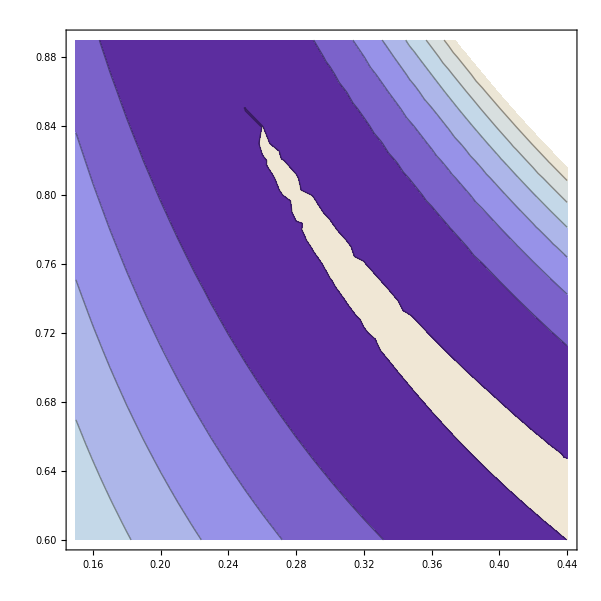

```mathematica
ListContourPlot[chi2tabtt,InterpolationOrder->1]
```